# A. Offspring control (Mike version)

## Recursions (written as in appendix, generic loci order) [Enter]

### Haploid selection

We start with haploid selection, which occurs in sperm/pollen only. We assume male sperm/pollen compete for eggs, and that the allele at the autosomal locus determines their competitive ability (with relative fitnesses wA and wa). After selection on male gametes/pollen the frequencies of gametes in each sex are

```mathematica
(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAMms+XaMms+YAMms+YaMms+XAmms+Xamms+YAmms+Yamms//Factor (*male gametes*)
1==XAMfs+XaMfs+XAmfs+Xamfs+YAMfs+YaMfs+YAmfs+Yamfs//Factor (*eggs*)
```

True

True

### Random mating

After random mating, the frequencies of the diploid genotypes are

```mathematica
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
```

Check that they sum to one

```mathematica
1==XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMXAMmale+XAMXaMmale+XaMXaMmale+
XAMYAMmale+XAMYaMmale+XaMYAMmale+XaMYaMmale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMmale+YAMYaMmale+YaMYaMmale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmXAMmale+XAmXaMmale+XAMXammale+XamXaMmale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAmYAMmale+XAmYaMmale+XamYAMmale+XamYaMmale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
XAMYAmmale+XAMYammale+XaMYAmmale+XaMYammale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
YAmYAMmale+YAmYaMmale+YamYAMmale+YamYaMmale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmXAmmale+XAmXammale+XamXammale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
XAmYAmmale+XAmYammale+XamYAmmale+XamYammale+
YAmYAmfemale+YAmYamfemale+YamYamfemale+
YAmYAmmale+YAmYammale+YamYammale//Factor
```

True

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Frequencies after selection in diploid are indicated by appending an s to the name.

```mathematica
(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;
```

Frequency of males after diplod selection should sum to 1

```mathematica
1==XAMXAMmales+XAMXaMmales+XaMXaMmales+
XAMYAMmales+XAMYaMmales+XaMYAMmales+XaMYaMmales+
YAMYAMmales+YAMYaMmales+YaMYaMmales+
XAmXAMmales+XAmXaMmales+XAMXammales+XamXaMmales+
XAmYAMmales+XAmYaMmales+XamYAMmales+XamYaMmales+
XAMYAmmales+XAMYammales+XaMYAmmales+XaMYammales+
YAmYAMmales+YAmYaMmales+YamYAMmales+YamYaMmales+
XAmXAmmales+XAmXammales+XamXammales+
XAmYAmmales+XAmYammales+XamYAmmales+XamYammales+
YAmYAmmales+YAmYammales+YamYammales//Factor
```

True

```mathematica
(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;
```

Frequency of females after diplod selection should sum to 1

```mathematica
1==XAMXAMfemales+XAMXaMfemales+XaMXaMfemales+
XAMYAMfemales+XAMYaMfemales+XaMYAMfemales+XaMYaMfemales+
YAMYAMfemales+YAMYaMfemales+YaMYaMfemales+
XAmXAMfemales+XAmXaMfemales+XAMXamfemales+XamXaMfemales+
XAmYAMfemales+XAmYaMfemales+XamYAMfemales+XamYaMfemales+
XAMYAmfemales+XAMYamfemales+XaMYAmfemales+XaMYamfemales+
YAmYAMfemales+YAmYaMfemales+YamYAMfemales+YamYaMfemales+
XAmXAmfemales+XAmXamfemales+XamXamfemales+
XAmYAmfemales+XAmYamfemales+XamYAmfemales+XamYamfemales+
YAmYAmfemales+YAmYamfemales+YamYamfemales//Factor
```

True

### Meiosis

Translate into new notation:

first two letters refer to SDR locus genotype, then numbers ij giving A and M locus genotype where 
1-AM
2-aM
3-Am
4-am
then m or f indicating male or female
then s to indicate that these are frequencies after selection
e.g., xy41ms is a male with genotype X-a-m Y-A-M. 
Where i and j are interchangable (in YY and XX individuals) the lowest number is given first.

```mathematica
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;
```

```mathematica
xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
```

First, we consider female gametes

```mathematica
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
```

```mathematica
Factor[nextXAMf+nextXaMf+nextXAmf+nextXamf+nextYAMf+nextYaMf+nextYAmf+nextYamf]
```

1

We can consider male gametes similarly

```mathematica
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;
```

```mathematica
Factor[nextXAMm+nextXaMm+nextXAmm+nextXamm+nextYAMm+nextYaMm+nextYAmm+nextYamm]
```

1

Generally want to at least assume that recombination is not affected by M or sex

```mathematica
SUBSR={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ
};
```

Often also want to assume the following about k:

```mathematica
SUBS={
Rm->R,
Rf->R,
rMMm->r,
rMmm->r,
rmmm->r,
rMMf->r,
rMmf->r,
rmmf->r,
χm->χ,
χf->χ,
kXX->1,
kXY->0,
kYY->0,
kMmXX->k,
kMmXY->k,
kMmYY->k,
kmm->k,
kmm->k,
kmm->k
};
```

## Complete linkage case (r=0)

### Equilibrium [ENTER]

Working in allele frequencies rather than haplotype frequencies:

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

```mathematica
equilA0={pXf->(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm->-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm->0,freqYm->(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))};
```

```mathematica
equilAp0={pXf->(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm->(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm->1,freqYm->(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))};
```

```mathematica
equilB0={pXf->1,pXm->1,pYm->0,freqYm->1-αm};
```

```mathematica
equilBp0={pXf->0,pXm->0,pYm->1,freqYm->αm};
```

```mathematica
equilC0={pXf->(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm->(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm->(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYm->(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))};
```

Factor[differenceEqs /. r -> 0 /. {equilA0, equilAp0, equilB0, equilBp0, equilC0}]

{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

To be relevant, this last equilibrium equilC0 requires that the numerators of the frequency of A and a in females are both positive or both negative (they share the same denominator, which is the sum of the numerators):

```mathematica
{pXf,1-pXf}/.equilC0//Factor
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm),(wAf (-2 MAa wam+MAA wAm+2 MAa wam αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm)}

Hence, either 2(1-αm) MAa wam > MAA wAm and 2 αm MAa wAm > Maa wam (akin to heterozygous advantage without pollen selection) or 2(1-αm) MAa wam < MAA wAm and 2 αm MAa wAm < Maa wam (akin to heterozygous disadvantage) otherwise pXf won’t lie between 0 and 1.

equilC0 will be shown later to not be internally stable when it exists, so this equilibrium can be ignored when examining the evolution of recombination.

The next order terms in the recombination rate, r (used in the weak selection approximations to assess the effect of r):

```mathematica
equilA1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm->(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm->(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2};
```

```mathematica
equilAp1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm->(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm->-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2};
```

```mathematica
equilB1={pXfsm->-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm->(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm->-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm->r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))};
```

```mathematica
equilBp1={pXfsm->-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm->-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm->(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm->r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))};
```

### Equilibrium Derivation

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following four equations are zero

```mathematica
differenceEqs={
nextXAMf-XAMf,
nextXAMm-XAMm,
nextYAMm-YAMm,
nextYAMm+nextYaMm-(YAMm+YaMm)
}/.SUBS/.subequil;
```

```mathematica
sub1=Flatten[Solve[differenceEqs[[3]]==0,pXf]]//Factor
```

{pXf→(2 pYm waf (-freqYm Maa wam+freqYm Maa pYm wam-freqYm MAa pYm wAm+MAa wAm αm-MAa r wAm αm))/(-2 freqYm Maa pYm waf wam+2 freqYm Maa pYm^2 waf wam+2 freqYm MAa pYm wAf wam-2 freqYm MAa pYm^2 wAf wam-2 freqYm MAa pYm^2 waf wAm-MAA pYm wAf wAm+2 freqYm MAA pYm^2 wAf wAm-2 MAa r wAf wam αm+2 MAa pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pYm r waf wAm αm)}

```mathematica
differenceEqs[[2]]/.sub1//Factor
```

(-Maa MAA pXm pYm wam wAm+freqYm Maa MAA pXm pYm wam wAm+freqYm Maa MAA pYm^2 wam wAm+Maa MAA pXm pYm^2 wam wAm-freqYm Maa MAA pXm pYm^2 wam wAm-freqYm Maa MAA pYm^3 wam wAm-MAa MAA pXm pYm^2 wAm^2+freqYm MAa MAA pXm pYm^2 wAm^2+freqYm MAa MAA pYm^3 wAm^2+2 freqYm Maa MAa pYm wam^2 αm-4 freqYm Maa MAa pYm^2 wam^2 αm+2 freqYm Maa MAa pYm^3 wam^2 αm-2 Maa MAa pXm r wam^2 αm+2 freqYm Maa MAa pXm r wam^2 αm-2 freqYm Maa MAa pYm r wam^2 αm+4 Maa MAa pXm pYm r wam^2 αm-4 freqYm Maa MAa pXm pYm r wam^2 αm+4 freqYm Maa MAa pYm^2 r wam^2 αm-2 Maa MAa pXm pYm^2 r wam^2 αm+2 freqYm Maa MAa pXm pYm^2 r wam^2 αm-2 freqYm Maa MAa pYm^3 r wam^2 αm+2 MAa^2 pXm pYm wam wAm αm-2 freqYm MAa^2 pXm pYm wam wAm αm+2 freqYm MAa^2 pYm^2 wam wAm αm-2 MAa^2 pXm pYm^2 wam wAm αm+2 freqYm MAa^2 pXm pYm^2 wam wAm αm-2 freqYm MAa^2 pYm^3 wam wAm αm-4 MAa^2 pXm pYm r wam wAm αm+4 freqYm MAa^2 pXm pYm r wam wAm αm-4 freqYm MAa^2 pYm^2 r wam wAm αm+4 MAa^2 pXm pYm^2 r wam wAm αm-4 freqYm MAa^2 pXm pYm^2 r wam wAm αm+4 freqYm MAa^2 pYm^3 r wam wAm αm-MAa MAA pYm^2 wAm^2 αm+2 MAa MAA pXm pYm^2 wAm^2 αm-2 freqYm MAa MAA pXm pYm^2 wAm^2 αm+2 MAa MAA pYm^2 r wAm^2 αm-2 MAa MAA pXm pYm^2 r wAm^2 αm+2 freqYm MAa MAA pXm pYm^2 r wAm^2 αm-2 freqYm MAa MAA pYm^3 r wAm^2 αm-2 MAa^2 pYm wam wAm αm^2+2 MAa^2 pYm^2 wam wAm αm^2+4 MAa^2 pYm r wam wAm αm^2-4 MAa^2 pYm^2 r wam wAm αm^2)/(Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+MAa MAA pYm^2 wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-2 MAa^2 pYm wam wAm αm+2 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm r wam wAm αm-4 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 wAm^2 αm+2 MAa MAA pYm^2 r wAm^2 αm)

```mathematica
sub2=Flatten[Solve[Factor[differenceEqs[[2]]/.sub1]==0,pXm]]//Factor
```

{pXm→-(pYm (-freqYm Maa MAA pYm wam wAm+freqYm Maa MAA pYm^2 wam wAm-freqYm MAa MAA pYm^2 wAm^2-2 freqYm Maa MAa wam^2 αm+4 freqYm Maa MAa pYm wam^2 αm-2 freqYm Maa MAa pYm^2 wam^2 αm+2 freqYm Maa MAa r wam^2 αm-4 freqYm Maa MAa pYm r wam^2 αm+2 freqYm Maa MAa pYm^2 r wam^2 αm-2 freqYm MAa^2 pYm wam wAm αm+2 freqYm MAa^2 pYm^2 wam wAm αm+4 freqYm MAa^2 pYm r wam wAm αm-4 freqYm MAa^2 pYm^2 r wam wAm αm+MAa MAA pYm wAm^2 αm-2 MAa MAA pYm r wAm^2 αm+2 freqYm MAa MAA pYm^2 r wAm^2 αm+2 MAa^2 wam wAm αm^2-2 MAa^2 pYm wam wAm αm^2-4 MAa^2 r wam wAm αm^2+4 MAa^2 pYm r wam wAm αm^2))/((-1+freqYm) (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-MAa MAA pYm^2 wAm^2-2 Maa MAa r wam^2 αm+4 Maa MAa pYm r wam^2 αm-2 Maa MAa pYm^2 r wam^2 αm+2 MAa^2 pYm wam wAm αm-2 MAa^2 pYm^2 wam wAm αm-4 MAa^2 pYm r wam wAm αm+4 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm))}

```mathematica
differenceEqs[[4]]/.sub1/.sub2//Factor
```

(2 freqYm Maa MAa pYm wam^2-4 freqYm Maa MAa pYm^2 wam^2+2 freqYm Maa MAa pYm^3 wam^2-4 freqYm Maa MAa pYm r wam^2+8 freqYm Maa MAa pYm^2 r wam^2-4 freqYm Maa MAa pYm^3 r wam^2+Maa MAA pYm wam wAm-2 freqYm Maa MAA pYm wam wAm+4 freqYm MAa^2 pYm^2 wam wAm-Maa MAA pYm^2 wam wAm+2 freqYm Maa MAA pYm^2 wam wAm-4 freqYm MAa^2 pYm^3 wam wAm-8 freqYm MAa^2 pYm^2 r wam wAm+8 freqYm MAa^2 pYm^3 r wam wAm-2 freqYm MAa MAA pYm^2 wAm^2+2 freqYm MAa MAA pYm^3 wAm^2+2 MAa MAA pYm^2 r wAm^2-4 freqYm MAa MAA pYm^3 r wAm^2-4 freqYm Maa MAa pYm wam^2 αm+8 freqYm Maa MAa pYm^2 wam^2 αm-4 freqYm Maa MAa pYm^3 wam^2 αm+2 Maa MAa r wam^2 αm-4 freqYm Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+16 freqYm Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-20 freqYm Maa MAa pYm^2 r wam^2 αm+8 freqYm Maa MAa pYm^3 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 freqYm MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm-12 freqYm MAa^2 pYm^2 wam wAm αm+8 freqYm MAa^2 pYm^3 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 freqYm MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+24 freqYm MAa^2 pYm^2 r wam wAm αm-16 freqYm MAa^2 pYm^3 r wam wAm αm+4 freqYm MAa MAA pYm^2 wAm^2 αm-4 freqYm MAa MAA pYm^3 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm-4 freqYm MAa MAA pYm^2 r wAm^2 αm+8 freqYm MAa MAA pYm^3 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2)/(2 (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+MAa MAA pYm^2 wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-2 MAa^2 pYm wam wAm αm+2 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm r wam wAm αm-4 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 wAm^2 αm+2 MAa MAA pYm^2 r wAm^2 αm))

```mathematica
sub3=Flatten[Solve[Factor[differenceEqs[[4]]/.sub1/.sub2]==0,freqYm]]//Factor
```

{freqYm→-(Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2)/(2 (Maa MAa pYm wam^2-2 Maa MAa pYm^2 wam^2+Maa MAa pYm^3 wam^2-2 Maa MAa pYm r wam^2+4 Maa MAa pYm^2 r wam^2-2 Maa MAa pYm^3 r wam^2-Maa MAA pYm wam wAm+2 MAa^2 pYm^2 wam wAm+Maa MAA pYm^2 wam wAm-2 MAa^2 pYm^3 wam wAm-4 MAa^2 pYm^2 r wam wAm+4 MAa^2 pYm^3 r wam wAm-MAa MAA pYm^2 wAm^2+MAa MAA pYm^3 wAm^2-2 MAa MAA pYm^3 r wAm^2-2 Maa MAa pYm wam^2 αm+4 Maa MAa pYm^2 wam^2 αm-2 Maa MAa pYm^3 wam^2 αm-2 Maa MAa r wam^2 αm+8 Maa MAa pYm r wam^2 αm-10 Maa MAa pYm^2 r wam^2 αm+4 Maa MAa pYm^3 r wam^2 αm+2 MAa^2 pYm wam wAm αm-6 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm^3 wam wAm αm-4 MAa^2 pYm r wam wAm αm+12 MAa^2 pYm^2 r wam wAm αm-8 MAa^2 pYm^3 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^3 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa MAA pYm^3 r wAm^2 αm))}

```mathematica
equilsol=Numerator[Factor[differenceEqs[[1]]/.sub1/.sub2/.sub3]]
```

-(-1+pYm) pYm (2 FAa Maa^3 MAa pYm^2 waf wam^5-4 Faa Maa^2 MAa^2 pYm^2 waf wam^5-6 FAa Maa^3 MAa pYm^3 waf wam^5+12 Faa Maa^2 MAa^2 pYm^3 waf wam^5+«1951»+448 FAa MAa^4 pYm^3 r^3 waf wam^2 wAm^3 αf αm^4-512 FAa MAa^4 pYm^4 r^3 waf wam^2 wAm^3 αf αm^4+256 FAa MAa^4 pYm^5 r^3 waf wam^2 wAm^3 αf αm^4)

In the following we assume r=0 to leading order to determine the equilibrium in the case where the A locus resides in the SDR:

```mathematica
equilsol/.r->0//Factor
```

(-1+pYm)^3 pYm^3 (-2 MAa wam+MAA wAm+2 MAa wam αm) (Maa wam-2 MAa wAm αm) (FAa Maa^2 waf wam^3-2 Faa Maa MAa waf wam^3-FAa Maa^2 pYm waf wam^3+2 Faa Maa MAa pYm waf wam^3+Faa Maa MAA waf wam^2 wAm+2 FAa Maa MAa pYm waf wam^2 wAm-4 Faa MAa^2 pYm waf wam^2 wAm-Faa Maa MAA pYm waf wam^2 wAm+FAa Maa MAA pYm waf wam wAm^2+2 Faa MAa MAA pYm waf wam wAm^2-FAA Maa MAA pYm wAf wam wAm^2-FAa Maa^2 waf wam^3 αf+FAa Maa^2 pYm waf wam^3 αf+2 FAa Maa MAa wAf wam^3 αf-2 FAa Maa MAa pYm wAf wam^3 αf-2 FAa Maa MAa pYm waf wam^2 wAm αf-FAa Maa MAA wAf wam^2 wAm αf+4 FAa MAa^2 pYm wAf wam^2 wAm αf+FAa Maa MAA pYm wAf wam^2 wAm αf-FAa Maa MAA pYm waf wam wAm^2 αf-FAa MAA^2 pYm wAf wAm^3 αf+2 Faa Maa MAa waf wam^3 αm-2 Faa Maa MAa pYm waf wam^3 αm-2 FAa Maa MAa pYm waf wam^2 wAm αm+8 Faa MAa^2 pYm waf wam^2 wAm αm-2 FAA Maa MAa wAf wam^2 wAm αm+2 FAA Maa MAa pYm wAf wam^2 wAm αm-4 FAa MAa^2 pYm waf wam wAm^2 αm-2 Faa MAa MAA pYm waf wam wAm^2 αm-2 FAa MAa MAA pYm waf wAm^3 αm+2 FAA MAa MAA pYm wAf wAm^3 αm-2 FAa Maa MAa wAf wam^3 αf αm+2 FAa Maa MAa pYm wAf wam^3 αf αm+2 FAa Maa MAa pYm waf wam^2 wAm αf αm+4 FAa MAa^2 wAf wam^2 wAm αf αm-12 FAa MAa^2 pYm wAf wam^2 wAm αf αm+4 FAa MAa^2 pYm waf wam wAm^2 αf αm-2 FAa MAa MAA wAf wam wAm^2 αf αm+2 FAa MAa MAA pYm wAf wam wAm^2 αf αm+2 FAa MAa MAA pYm waf wAm^3 αf αm-4 Faa MAa^2 pYm waf wam^2 wAm αm^2-4 FAa MAa^2 waf wam wAm^2 αm^2+8 FAa MAa^2 pYm waf wam wAm^2 αm^2+4 FAA MAa^2 wAf wam wAm^2 αm^2-4 FAA MAa^2 pYm wAf wam wAm^2 αm^2-4 FAa MAa^2 wAf wam^2 wAm αf αm^2+8 FAa MAa^2 pYm wAf wam^2 wAm αf αm^2+4 FAa MAa^2 waf wam wAm^2 αf αm^2-8 FAa MAa^2 pYm waf wam wAm^2 αf αm^2)

```mathematica
equilsol2=Solve[%==0,pYm]//Simplify
```

{{pYm→0},{pYm→0},{pYm→0},{pYm→1},{pYm→1},{pYm→1},{pYm→(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))}}

In the following, we assume that pYm is either 0, 1, or the last of the above solutions.  When r=0 and pYm = 0 or 1, its safest to rederive the solution for {pXf, pXm, freqYm} (using the substitutions to define these goes astray because some of the intermediate steps are zero when r = 0 and pYm = 0 or 1).

First, consider cases where pYm=0.

With allele A fixed on Y (pYm=0), then {pXf, pXm, freqYm} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->1//Factor)=={0,0,0,0},{pXf,pXm,freqYm}]//Simplify
```

{{pXf→0,pXm→0,freqYm→αm},{pXf→1,pXm→1,freqYm→1/2},{pXf→(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm→(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),freqYm→(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilA0 (“0” because this is the leading order term in r...we could take additional order terms to get the linear approximation in r, etc.).  

The first of these {pXf→0,pXm→0,freqYm→αm} is also polymorphic (Y fixed on A and X fixed on a), which we’ll call equilB0.

Next, consider cases where pYm=0.

With allele A fixed on Y (pYm=0), then {pXf, pXm, freqYm} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->0//Factor)=={0,0,0,0},{pXf,pXm,freqYm}]//Simplify
```

{{pXf→0,pXm→0,freqYm→1/2},{pXf→1,pXm→1,freqYm→1-αm},{pXf→(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm→-((2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))),freqYm→(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilAp0 (“p” for prime -- the alternate allele is fixed on the Y).  

The second of these {pXf→1,pXm→1,freqYm→1-αm} is also polymorphic (Y fixed on a and X fixed on A), which we’ll call equilBp0.

Finally, we have the equilibrium (which will turn out to not be stable) with freq(A) on Y = (wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))):

```mathematica
Factor[{pXf,pXm,pYm,freqYm}/.sub1/.sub2/.sub3/.r->0]/.Last[equilsol2]//Simplify
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))}

We’ll call this equilC.

Getting the next order in the recombination rate (these are needed during the derivation of the external stability conditions to ensure that all of the small terms not involving the modifier cancel):

(This takes a while...)

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilA0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilA1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm→(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm→(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm→(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2}

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilAp0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilAp1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm→(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm→-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm→(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2}

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilB0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilB1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm→(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm→-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm→r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))}

```mathematica
Factor[Normal[Series[differenceEqs/.pXf->pXf+pXfsm*sm/.pXm->pXm+pXmsm*sm/.pYm->pYm+pYmsm*sm/.freqYm->freqYm+freqYmsm*sm/.r->r*sm/.equilBp0,{sm,0,1}]]]/.sm->1;
```

```mathematica
equilBp1=Flatten[Simplify[Solve[%==0,{pXfsm,pXmsm,pYmsm,freqYmsm}]]]
```

{pXfsm→-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm→-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm→(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm→r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))}

### Validity and stability of polymorphic equilibrium (M fixed) - tight linkage

Assumptions used to simplify the results:

```mathematica
simpcond=Reduce[{0<MAA,0<MAa,0<Maa,0<FAA,0<FAa,0<Faa,0<wAf,0<waf,0<wAm,0<wam,0<αm<1,0<αf<1,0≤Rm≤1/2,0≤Rf≤1/2}];
```

We also consider only equilibria A, B, and C (i.e., with a fixed on Y).  The conditions required for equilibria A’ and B’ can be obtained by interchanging the alleles, A and a.

#### General [ENTER]

The local stability matrix with the M allele fixed:

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs={nextXAMf,nextXAMm/(nextXAMm+nextXaMm),nextYAMm/(nextYAMm+nextYaMm),nextYAMm+nextYaMm}/.SUBS/.subequil;
matIntFull=Transpose[{
D[eqs,pXf],
D[eqs,pXm],
D[eqs,pYm],
D[eqs,freqYm]
}]/.SUBS/.subequil//Factor;
```

The last column of matIntFull is full of zeros, corresponding to an eigenvalue of zero and indicating that the sex ratio in the system equilibrates immediately:

```mathematica
Transpose[matIntFull][[4]]
```

{0,0,0,0}

As a consequence, we drop the last row and column in matIntFull:

```mathematica
matIntFull=Table[matIntFull[[i,j]],{i,1,3},{j,1,3}];
```

From this we can derive the characteristic polynomial with r = 0:

```mathematica
charpolyIntFull=Det[(matIntFull/.r->0)-IdentityMatrix[3]*λ];
```

#### Equilibrium A (r ~ 0)

```mathematica
eq1=Factor[pXf/.equilA0]
```

(waf (Faa Maa waf wam-FAa Maa wAf wam αf-2 FAa MAa wAf wAm αf αm))/(Faa Maa waf^2 wam-FAa Maa waf wAf wam-2 FAa MAa waf wAf wAm αm+2 FAA MAa wAf^2 wAm αm)

```mathematica
eq2=Factor[pXm/.equilA0]
```

(2 MAa αm (-Faa Maa waf wam+FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm))/(FAa Maa^2 waf wam-FAa Maa^2 waf wam αf-2 Faa Maa MAa waf wam αm+2 FAa Maa MAa waf wAm αm-2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm-2 FAa Maa MAa waf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2)

```mathematica
eq3=Factor[pYm/.equilA0]
```

0

We must have each of the following terms be positive for the equilibrium to be valid:

```mathematica
{{eq1,1-eq1},{eq2,1-eq2}}//Simplify
```

{{(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),(wAf (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))},{-((2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))),(Maa (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))}}

```mathematica
Reduce[{0<eq1<1,0<eq2<1,simpcond},{FAA,Faa}]
```

(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&0<FAA<(FAa Maa waf wam-FAa Maa waf wam αf+2 FAa MAa waf wAm αm-2 FAa MAa waf wAm αf αm)/(2 MAa wAf wAm αm)&&0<Faa<(FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm)/(Maa waf wam))||(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&FAA>(FAa Maa waf wam-FAa Maa waf wam αf+2 FAa MAa waf wAm αm-2 FAa MAa waf wAm αf αm)/(2 MAa wAf wAm αm)&&Faa>(FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm)/(Maa waf wam))

Notice that the numerators are common in sign for {eq1,1-eq1} and {eq2,1-eq2}.  Thus, either the numerators and denominators must be both positive or both negative, the equilibrium will not be valid otherwise.  That is, we must have either:

Condition 1:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) > Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)> FAA

or

Condition 2:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) < Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)< FAA

That is, equilA0 is valid if:

```mathematica
validcondA=((FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)));
```

Making a set of substitutions that might help simplify factors below:

```mathematica
subA1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(Maa waf wam (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf))/(2 wAf wAm (FAa pXf waf-FAA pXf wAf-FAa waf αf) αm)}

```mathematica
subA2=Solve[(eq2-pXm/.subA1)==0,FAa]//Flatten
```

{FAa→((-pXf+pXf^2) (-Faa waf wam+Faa pXm waf wam+FAA pXm wAf wAm))/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (pXf-αf))}

```mathematica
subA2b=Solve[(eq2-pXm/.subA1)==0,αf]//Flatten
```

{αf→(pXf (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm))/(FAa (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

The equilibrium A is stable if the three eigenvalues of the stability matrix are all less than one in magnitude:

```mathematica
eigenA=Simplify[Eigenvalues[matIntFull/.r->0/.equilA0]]
```

{(wAm (Faa Maa MAA waf wam+4 FAA MAa^2 wAf wAm αm^2+FAa (Maa wam+2 MAa wAm αm) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(wam (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))),(-Faa FAa Maa^2 waf^2 wam^2+Faa FAa Maa^2 waf^2 wam^2 αf+2 Faa FAA Maa MAa waf wAf wam wAm αm-4 FAa FAA MAa^2 wAf^2 wAm^2 αf αm^2+FAa^2 Maa^2 waf wAf wam^2 αf √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-FAa^2 Maa^2 waf wAf wam^2 αf^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-2 Faa FAA Maa MAa waf wAf wam wAm αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 Maa MAa waf wAf wam wAm αf αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 Maa MAa waf wAf wam wAm αf^2 αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 MAa^2 waf wAf wAm^2 αf αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 MAa^2 waf wAf wAm^2 αf^2 αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2)))/(2 waf wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)),(-Faa FAa Maa^2 waf^2 wam^2+Faa FAa Maa^2 waf^2 wam^2 αf+2 Faa FAA Maa MAa waf wAf wam wAm αm-4 FAa FAA MAa^2 wAf^2 wAm^2 αf αm^2-FAa^2 Maa^2 waf wAf wam^2 αf √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+FAa^2 Maa^2 waf wAf wam^2 αf^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+2 Faa FAA Maa MAa waf wAf wam wAm αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 Maa MAa waf wAf wam wAm αf αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 Maa MAa waf wAf wam wAm αf^2 αm √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))-4 FAa^2 MAa^2 waf wAf wAm^2 αf αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2))+4 FAa^2 MAa^2 waf wAf wAm^2 αf^2 αm^2 √((-8 FAa^2 FAA MAa wAf^3 wAm αf^2 αm (-2 FAA MAa^3 wAf wAm^3 αm^3+FAa Maa waf wam (-1+αf) (Maa wam+2 MAa wAm αm)^2)+Faa^2 Maa^2 waf^2 wam^2 (FAa^2 Maa^2 waf^2 wam^2 (-1+αf)^2+20 FAA^2 MAa^2 wAf^2 wAm^2 αm^2+4 FAa FAA MAa waf wAf wAm (-1+αf) αm (Maa wam+4 MAa wAm αm))+8 Faa FAa Maa MAa waf wAf wam wAm αf αm (-2 FAA^2 MAa wAf^2 wAm αm (Maa wam+MAa wAm αm)+FAa^2 waf^2 (-1+αf)^2 (Maa wam+2 MAa wAm αm)^2+FAa FAA waf wAf (-1+αf) (Maa^2 wam^2+3 Maa MAa wam wAm αm+4 MAa^2 wAm^2 αm^2)))/(waf^2 wAf^2 (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)^2)))/(2 waf wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2))}

We are guaranteed that the eigenvalues are real  and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

This first eigenvalue is consistent with stability if the following is positive:

```mathematica
Collect[1-eigenA[[1]]/.subA1/.subA2,MAA,Factor]
```

(MAA pXf (-1+pXm) wAf wAm αm)/(Maa (-1+pXf) waf wam (-pXm-αm+2 pXm αm))-(pXf pXm wAf wam+pXf wAf wam αm-2 pXf pXm wAf wam αm-pXm waf wAm αm+pXf pXm waf wAm αm)/(pXf wAf wam (-pXm-αm+2 pXm αm))

which we write more clearly as:

```mathematica
-(MAA (1-pXm) pXf wAf wAm αm)/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm)))+(pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm(1-pXf) waf wAm αm)/(pXf wAf wam (pXm(1-αm)+αm(1-pXm)));
```

The first term is never positive, so we require that MAA be sufficiently small, MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm), which itself requires that the second term is positive (i.e., we must have pXf wAf wam ((pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm)>0 for there to be any parameter set in which MAA can be positive and less than this quantity):

```mathematica
Solve[%==0,MAA]//Simplify
```

{{MAA→(Maa (-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))/(pXf^2 (-1+pXm) wAf^2 wAm αm)}}

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
Table[matIntFull[[i,j]],{i,1,2},{j,1,2}]/.r->0/.equilA0//Factor;
charpolyA=Det[%-λ IdentityMatrix[2]]//Factor;
```

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeA=D[charpolyA,λ]/.λ->1/.subA1/.subA2//Factor
```

(-Faa pXf^2 waf wAf wam^2+2 Faa pXf^2 pXm waf wAf wam^2-Faa pXf^2 pXm^2 waf wAf wam^2+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+FAA pXf pXm^2 waf wAf wAm^2-FAA pXf^2 pXm^2 waf wAf wAm^2-Faa pXf waf wAf wam^2 αf+2 Faa pXf^2 waf wAf wam^2 αf+2 Faa pXf pXm waf wAf wam^2 αf-4 Faa pXf^2 pXm waf wAf wam^2 αf-Faa pXf pXm^2 waf wAf wam^2 αf+2 Faa pXf^2 pXm^2 waf wAf wam^2 αf-2 Faa pXm waf^2 wam wAm αf+4 Faa pXf pXm waf^2 wam wAm αf-2 Faa pXf^2 pXm waf^2 wam wAm αf+2 Faa pXm^2 waf^2 wam wAm αf-4 Faa pXf pXm^2 waf^2 wam wAm αf+2 Faa pXf^2 pXm^2 waf^2 wam wAm αf-2 FAA pXf^2 pXm wAf^2 wam wAm αf+2 FAA pXf^2 pXm^2 wAf^2 wam wAm αf+FAA pXm^2 waf wAf wAm^2 αf-3 FAA pXf pXm^2 waf wAf wAm^2 αf+2 FAA pXf^2 pXm^2 waf wAf wAm^2 αf)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf))

```mathematica
slopeA2=D[charpolyA,λ]/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

```mathematica
interceptA=charpolyA/.λ->1/.subA1/.subA2//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-Faa pXf waf wam αf+Faa pXf pXm waf wam αf-FAA pXm wAf wAm αf+FAA pXf pXm wAf wAm αf)/(-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf)

The intercept is easier to interpret using subA2b:

```mathematica
interceptA2=charpolyA/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm)/(-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm)

Using Collect, this can be written as:

```mathematica
(-Faa pXf (1-pXm)waf wam-FAA (1-pXf) pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm))/(Faa (1-pXf) (1-pXm)waf wam+FAA pXf pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm));
Factor[interceptA2/%]
```

1

The denominator is always positive, so we require the numerator to be positive for stability, that is, FAa must be large enough for the intercept at λ=1 to be positive, FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm).

Note that the fraction can be interpretted further in light of the validity conditions:

```mathematica
validcondA
```

(FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))

Under the first of these conditions (equivalent to overdominance), (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be less than

```mathematica
((FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) pXf (1-pXm)waf wam+(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm) (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)/.subA1/.subA2b//Factor
```

FAa

which makes it guaranteed that FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (i.e., the validity conditions in the overdominance-like case ensure intercept condition for stability is satisfied). 

Under the second of these conditions (equivalent to underdominance), however, (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be greater than FAa by the same calculations, making it impossible to satisfy the intercept condition for stability.

We conclude that only under the first validity conditions (equivalent to overdominance) is stability and validity of the equilibrium  possible.  Furthermore, under the first validity conditions, we are guaranteed that the intercept is positive at λ=1.

To complete the proof, we show below that the slope at λ=1 provides no further conditions on stability:

```mathematica
slopeA//Factor
```

(-Faa pXf^2 waf wAf wam^2+2 Faa pXf^2 pXm waf wAf wam^2-Faa pXf^2 pXm^2 waf wAf wam^2+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+FAA pXf pXm^2 waf wAf wAm^2-FAA pXf^2 pXm^2 waf wAf wAm^2-Faa pXf waf wAf wam^2 αf+2 Faa pXf^2 waf wAf wam^2 αf+2 Faa pXf pXm waf wAf wam^2 αf-4 Faa pXf^2 pXm waf wAf wam^2 αf-Faa pXf pXm^2 waf wAf wam^2 αf+2 Faa pXf^2 pXm^2 waf wAf wam^2 αf-2 Faa pXm waf^2 wam wAm αf+4 Faa pXf pXm waf^2 wam wAm αf-2 Faa pXf^2 pXm waf^2 wam wAm αf+2 Faa pXm^2 waf^2 wam wAm αf-4 Faa pXf pXm^2 waf^2 wam wAm αf+2 Faa pXf^2 pXm^2 waf^2 wam wAm αf-2 FAA pXf^2 pXm wAf^2 wam wAm αf+2 FAA pXf^2 pXm^2 wAf^2 wam wAm αf+FAA pXm^2 waf wAf wAm^2 αf-3 FAA pXf pXm^2 waf wAf wAm^2 αf+2 FAA pXf^2 pXm^2 waf wAf wAm^2 αf)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf))

After a few attempts, it turned out to be easier to work with slopeA2 for this proof...

```mathematica
slopeA2//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

The proof we use involves rewriting the above in terms of the intercept, shown above to be positive:

```mathematica
subtry=Solve[int==interceptA2,FAa]//Flatten
```

{FAa→(Faa int waf wam+Faa pXf waf wam-Faa int pXf waf wam-Faa int pXm waf wam-Faa pXf pXm waf wam+Faa int pXf pXm waf wam+FAA pXm wAf wAm-FAA pXf pXm wAf wAm+FAA int pXf pXm wAf wAm)/((-1+int) (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

Multiplying slopeA2 by a positive quantity to get rid of the denominator:

```mathematica
slopeA2*((pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm)))//Factor
```

Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2

```mathematica
Collect[Factor[% (1-int)/.subtry],{int,Faa,FAa,FAA},Factor]
```

-FAA pXm wAf wAm (-2 pXf wAf wam+2 pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm)+Faa (-1+pXm) waf wam (-pXf wAf wam+pXf pXm wAf wam-2 pXm waf wAm+2 pXf pXm waf wAm)+int (Faa pXf (-1+pXm)^2 waf wAf wam^2-FAA (-1+pXf) pXm^2 waf wAf wAm^2)

Below, we show that (1-int) is also positive (that is, the intercept at λ=1 is never greater than +1), the remaining quantity can be written as the following:

```mathematica
Faa waf wam (1-pXm) (pXf(1-pXm)wAf wam+2 pXm(1-pXf)waf wAm)+FAA wAf wAm pXm  (2 pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)+int (Faa pXf (1-pXm)^2 waf wAf wam^2+FAA (1-pXf) pXm^2 waf wAf wAm^2);
%%-%//Factor
```

0

If the intercept is negative, we already know that the system is unstable (above proof).  If the intercept is positive, then the slope will also be positive because all of the terms in the above are positive and so is (1-int), shown next:

```mathematica
Factor[1-interceptA2]
```

-(-Faa waf wam+Faa pXm waf wam-FAA pXm wAf wAm)/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)

Using Collect, this can be written as the strictly positive quantity:

```mathematica
(Faa waf wam(1-pXm)+FAA wAf wAm pXm)/(Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm));
Factor[(1-interceptA2)-%]
```

0

Hence the slope at λ=1 is positive, assuming that the intercept at λ=1 is positive, and adds no further constraint on the stability conditions.

Putting together the constraints on all of the eigenvalues, as well as the validity conditions, the conditions required for validity and stability are:

```mathematica
stabcondA=Simplify[Reduce[{MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm),validcondA[[1]],simpcond,0<pXf<1,0<pXm<1}]]
```

0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<pXm<1&&0<pXf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<-(pXf wAf wam (pXm+αm-2 pXm αm))/((-1+pXf) pXm wAm αm)&&MAA>0&&Maa>(MAA pXf^2 (-1+pXm) wAf^2 wAm αm)/((-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))&&0<αf<1&&MAa>0&&FAA>0&&FAa>-(2 FAA MAa wAf wAm αm)/(waf (-1+αf) (Maa wam+2 MAa wAm αm))&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)

We can regain the validity and stability conditions from Otto (2014):
	Condition for validity and stability:	(1+Maa)/(2Maa) > Faa and (1+Maa)/2> FAA and 1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa))>MAA.
 by reducing the model to that one (wAf=waf=wAm=wam=1, αm=αf=1/2, FAa=MAa=1):

```mathematica
validcondA[[1]]/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}
```

FAA<(1+Maa)/2&&Faa<(1+Maa)/(2 Maa)

```mathematica
(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}//Simplify
```

(Maa (-1+pXf) (pXf-pXm+pXf pXm))/(pXf^2 (-1+pXm))

Note that this last condition is the same as 1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa))>MAA:

```mathematica
(Maa (1-pXf)  (pXf -pXm (1-pXf)))/((1-pXm) pXf^2)-(1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa)))/.equilA0/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}//Factor
```

0

We cannot have underdominance in marginal fitness in females (including ovule selection):

```mathematica
Reduce[{stabcondA,FAA wAf>FAa waf,Faa waf>FAa wAf}]
```

False

#### Equilibrium B (r ~ 0)

```mathematica
matIntFull/.r->0/.equilB0//Factor;
%//MatrixForm
```

(-(FAa waf (-1+αf))/(FAA wAf) | -(FAa wam (-1+αf))/(FAA wAm) | 0
(Maa waf)/(2 MAa wAf αm) | 0 | 0
0 | 0 | -(MAA wAm)/(2 MAa wam (-1+αm)))

One eigenvalue is (MAA wAm)/(2 MAa wam (1-αm)).  And the last two are the roots of a 2x2.

```mathematica
eigenB=Simplify[Eigenvalues[matIntFull/.r->0/.equilB0]]
```

{(MAA wAm)/(2 MAa wam-2 MAa wam αm),-(FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm),(-FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm)}

Equilibrium B is locally stable when all eigenvalues are less than one in magnitude.  We are guaranteed that the eigenvalues are real and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
charpolyB=Collect[Det[Table[matIntFull[[i,j]]/.r->0/.equilB0,{i,1,2},{j,1,2}]-λ*IdentityMatrix[2]],λ,Factor]
```

(FAa Maa waf wam (-1+αf))/(2 FAA MAa wAf wAm αm)+(FAa waf (-1+αf) λ)/(FAA wAf)+λ^2

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeB=D[charpolyB,λ]/.λ->1//Factor
```

(-FAa waf+2 FAA wAf+FAa waf αf)/(FAA wAf)

```mathematica
interceptB=charpolyB/.λ->1//Factor
```

(-FAa Maa waf wam+FAa Maa waf wam αf-2 FAa MAa waf wAm αm+2 FAA MAa wAf wAm αm+2 FAa MAa waf wAm αf αm)/(2 FAA MAa wAf wAm αm)

SlopeB is strictly greater than interceptB, so both will be positive if interceptB is positive:

```mathematica
slopeB-interceptB//Factor
```

(FAa Maa waf wam-FAa Maa waf wam αf+2 FAA MAa wAf wAm αm)/(2 FAA MAa wAf wAm αm)

Thus, for equilibrium B to be stable, we must have (MAA wAm)/(2 MAa wam (1-αm))<1 and FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm):

```mathematica
stabcondB=Reduce[{(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&waf>0&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&Maa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

```mathematica
Solve[interceptB==0,FAA]//Simplify
```

{{FAA→-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)}}

#### Equilibrium C (r ~ 0): Never stable when it exists

```mathematica
eq1=pXf/.equilC0//Simplify
```

(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))

```mathematica
eq2=pXm/.equilC0//Simplify
```

(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm))))

```mathematica
eq3=pYm/.equilC0//Simplify
```

(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))

For pXf to lie between 0 and 1 requires that:

	pXf = (waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0
	
	1-pXf = (wAf (MAA wAm+2 MAa wam (-1+αm)))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0

so that either the numerators and denominators are both positive (without haploid selection, requires overdominance in males) or both negative (without haploid selection, requires underdominance in males).  The equilibrium will not be valid if (MAA wAm)/(2 wam (1-αm)) > MAa > (Maa wam)/(2 wAm αm) or if (MAA wAm)/(2 wam (1-αm)) < MAa < (Maa wam)/(2 wAm αm).

Evaluating the characteristic polynomial at λ = 1 (if this is negative, we know the leading eigenvalue is greater than one because the leading term of the characteristic polynomial is λ^3 and so it must eventually cross the horizontal axis at some λ>1):

```mathematica
stab=Factor[Det[IdentityMatrix[3]-matIntFull]/.r->0/.equilC0]
```

-((-2 MAa wam+MAA wAm+2 MAa wam αm) (Maa wam-2 MAa wAm αm) (-2 FAa Maa MAa waf wam^2+4 Faa MAa^2 waf wam^2-FAa Maa MAA waf wam wAm-2 Faa MAa MAA waf wam wAm+FAA Maa MAA wAf wam wAm+2 FAa Maa MAa waf wam^2 αf-4 FAa MAa^2 wAf wam^2 αf+FAa Maa MAA waf wam wAm αf+FAa MAA^2 wAf wAm^2 αf+2 FAa Maa MAa waf wam^2 αm-8 Faa MAa^2 waf wam^2 αm+4 FAa MAa^2 waf wam wAm αm+2 Faa MAa MAA waf wam wAm αm+2 FAa MAa MAA waf wAm^2 αm-2 FAA MAa MAA wAf wAm^2 αm-2 FAa Maa MAa waf wam^2 αf αm+8 FAa MAa^2 wAf wam^2 αf αm-4 FAa MAa^2 waf wam wAm αf αm-2 FAa MAa MAA waf wAm^2 αf αm+4 Faa MAa^2 waf wam^2 αm^2-4 FAa MAa^2 waf wam wAm αm^2-4 FAa MAa^2 wAf wam^2 αf αm^2+4 FAa MAa^2 waf wam wAm αf αm^2) (FAa Maa^2 waf wam^2-2 Faa Maa MAa waf wam^2+Faa Maa MAA waf wam wAm-FAa Maa^2 waf wam^2 αf+2 FAa Maa MAa wAf wam^2 αf-FAa Maa MAA wAf wam wAm αf+2 Faa Maa MAa waf wam^2 αm-2 FAA Maa MAa wAf wam wAm αm-2 FAa Maa MAa wAf wam^2 αf αm+4 FAa MAa^2 wAf wam wAm αf αm-2 FAa MAa MAA wAf wAm^2 αf αm-4 FAa MAa^2 waf wAm^2 αm^2+4 FAA MAa^2 wAf wAm^2 αm^2-4 FAa MAa^2 wAf wam wAm αf αm^2+4 FAa MAa^2 waf wAm^2 αf αm^2))/(waf wAf wam^2 wAm^2 (Maa MAA-4 MAa^2 αm+4 MAa^2 αm^2)^2 (FAa FAA Maa^2 wam^2-2 Faa FAA Maa MAa wam^2+Faa FAA Maa MAA wam wAm-FAa FAA Maa^2 wam^2 αf+4 Faa FAa MAa^2 wam^2 αf-4 Faa FAa MAa MAA wam wAm αf+Faa FAa MAA^2 wAm^2 αf+2 Faa FAA Maa MAa wam^2 αm-4 FAa FAA Maa MAa wam wAm αm+4 Faa FAA MAa^2 wam wAm αm-2 Faa FAA MAa MAA wAm^2 αm-8 Faa FAa MAa^2 wam^2 αf αm+4 FAa FAA Maa MAa wam wAm αf αm+4 Faa FAa MAa MAA wam wAm αf αm-4 Faa FAA MAa^2 wam wAm αm^2+4 FAa FAA MAa^2 wAm^2 αm^2+4 Faa FAa MAa^2 wam^2 αf αm^2-4 FAa FAA MAa^2 wAm^2 αf αm^2))

Making a set of substitutions that might help simplify factors below:

```mathematica
subC1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(-Maa waf wam+Maa pXf waf wam+MAA pXf wAf wAm)/(2 (pXf wAf wam-pXf wAf wam αm-waf wAm αm+pXf waf wAm αm))}

```mathematica
subC2=Solve[(eq2-pXm/.subC1)==0,FAA]//Flatten
```

{FAA→1/((-pXf+pXf^2) pXm wAf wAm)(-Faa pXf waf wam+Faa pXf^2 waf wam+Faa pXf pXm waf wam-Faa pXf^2 pXm waf wam-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)}

```mathematica
subC3=Solve[(eq3-pYm/.subC1/.subC2//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

With these substitutions, the sign of stab reduces to:

```mathematica
stab/.subC1/.subC2/.subC3//Factor;
Collect[Factor[%/((1-pYm) pYm wam (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /(pXm (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (Faa (1-pXf) (1-pXm) waf wam+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )(1-αf))))],{Faa,FAa,FAA},Factor]
```

Faa (-1+pXf) waf-FAa wAf (pXf-αf)

If (pXf-αf) is positive, the fraction is strictly positive, implying that stab is negative and the leading eigenvalue must be greater than one.

The case where (pXf-αf) is negative is better handled by repeating the above but with a different subC2 (replacing for Faa instead):

```mathematica
subC2b=Solve[(eq2-pXm/.subC1)==0,Faa]//Flatten
```

{Faa→1/((-pXf+pXf^2) (-1+pXm) waf wam)(-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAA pXf pXm wAf wAm-FAA pXf^2 pXm wAf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)}

```mathematica
subC3b=Solve[(eq3-pYm/.subC1/.subC2b//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

```mathematica
stab/.subC1/.subC2b/.subC3b//Factor;
Collect[Factor[%/((1-pYm) pYm wAm (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /((1-pXm) (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (FAA pXf pXm wAf wAm+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )αf)))],{Faa,FAa,FAA},Factor]
```

-FAA pXf wAf+FAa waf (pXf-αf)

Hence, if (pXf-αf) is negative, stab is also negative, and the leading eigenvalue must be greater than one.

We conclude that in no case can equilC0 represent a stable equilibrium.

```mathematica
(-((o1-pX1)^2 (1-pY1) pY1 (1-o1)(FAA o1(Oa+OA)-FAa (o1 Oa-OA(1-o1))))/((1-o1)(o1-pY1)^2(1-pX1)(FAA o1 (Oa+OA) pX1+FAa OA (o1(1-pX1)+pX1(1-o1)))));
%/stab/.subC1/.subC2/.subC3//Factor
```

((-o1+pX1)^2 pXm (-1+pY1) pY1 (pXf wAf wam-pXf pYm wAf wam-pYm waf wAm+pXf pYm waf wAm)^2 (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm-FAa pXf wAf wam αf+FAa pXf pXm wAf wam αf-FAa pXm waf wAm αf+FAa pXf pXm waf wAm αf) (Faa o1 Oa pXf waf wam+Faa o1 OA pXf waf wam-Faa o1 Oa pXf^2 waf wam-Faa o1 OA pXf^2 waf wam-Faa o1 Oa pXf pXm waf wam-Faa o1 OA pXf pXm waf wam+Faa o1 Oa pXf^2 pXm waf wam+Faa o1 OA pXf^2 pXm waf wam+FAa o1 Oa pXf^2 wAf wam+FAa o1 OA pXf^2 wAf wam-FAa o1 Oa pXf^2 pXm wAf wam-FAa o1 OA pXf^2 pXm wAf wam+FAa o1 Oa pXf pXm waf wAm+FAa o1 OA pXf pXm waf wAm-FAa o1 Oa pXf^2 pXm waf wAm-FAa o1 OA pXf^2 pXm waf wAm-FAa o1 Oa pXf pXm wAf wAm+FAa OA pXf pXm wAf wAm-FAa o1 OA pXf pXm wAf wAm+FAa o1 Oa pXf^2 pXm wAf wAm-FAa OA pXf^2 pXm wAf wAm+FAa o1 OA pXf^2 pXm wAf wAm-FAa o1 Oa pXf wAf wam αf-FAa o1 OA pXf wAf wam αf+FAa o1 Oa pXf pXm wAf wam αf+FAa o1 OA pXf pXm wAf wam αf-FAa o1 Oa pXm waf wAm αf-FAa o1 OA pXm waf wAm αf+FAa o1 Oa pXf pXm waf wAm αf+FAa o1 OA pXf pXm waf wAm αf))/((-1+pX1) (o1-pY1)^2 (-1+pYm) pYm wam (pXf wAf wam-pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm)^2 (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf) (Faa o1 Oa pX1 pXf waf wam+Faa o1 OA pX1 pXf waf wam-Faa o1 Oa pX1 pXf^2 waf wam-Faa o1 OA pX1 pXf^2 waf wam-Faa o1 Oa pX1 pXf pXm waf wam-Faa o1 OA pX1 pXf pXm waf wam+Faa o1 Oa pX1 pXf^2 pXm waf wam+Faa o1 OA pX1 pXf^2 pXm waf wam+FAa o1 Oa pX1 pXf^2 wAf wam+FAa o1 OA pX1 pXf^2 wAf wam-FAa o1 Oa pX1 pXf^2 pXm wAf wam-FAa o1 OA pX1 pXf^2 pXm wAf wam+FAa o1 Oa pX1 pXf pXm waf wAm+FAa o1 OA pX1 pXf pXm waf wAm-FAa o1 Oa pX1 pXf^2 pXm waf wAm-FAa o1 OA pX1 pXf^2 pXm waf wAm+FAa o1 OA pXf pXm wAf wAm+FAa OA pX1 pXf pXm wAf wAm-2 FAa o1 OA pX1 pXf pXm wAf wAm-FAa o1 OA pXf^2 pXm wAf wAm-FAa OA pX1 pXf^2 pXm wAf wAm+2 FAa o1 OA pX1 pXf^2 pXm wAf wAm-FAa o1 Oa pX1 pXf wAf wam αf-FAa o1 OA pX1 pXf wAf wam αf+FAa o1 Oa pX1 pXf pXm wAf wam αf+FAa o1 OA pX1 pXf pXm wAf wam αf-FAa o1 Oa pX1 pXm waf wAm αf-FAa o1 OA pX1 pXm waf wAm αf+FAa o1 Oa pX1 pXf pXm waf wAm αf+FAa o1 OA pX1 pXf pXm waf wAm αf))

Thus, if (o1 Oa-OA(1-o1)) is negative, the fraction is again strictly positive, implying that stab is negative and the leading eigenvalue must be greater than one.

We conclude that in no case can equilC0 represent a stable equilibrium.

### External stability to a new sex determining allele m [NEW]

#### General [ENTER]

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

Assumptions used to simplify the results:

```mathematica
simpcond=Reduce[{0<MAA,0<MAa,0<Maa,0<FAA,0<FAa,0<Faa,0<wAf,0<waf,0<wAm,0<wam,0<αm<1,0<αf<1,0≤Rm≤1/2,0≤Rf≤1/2}];
```

```mathematica
subequil
```

{XAMf→pXf,XaMf→1-pXf,YAMf→0,YaMf→0,XAMm→(1-freqYm) pXm,XaMm→(1-freqYm) (1-pXm),YAMm→freqYm pYm,YaMm→freqYm (1-pYm),XAmf→0,Xamf→0,XAmm→0,Xamm→0,YAmm→0,Yamm→0,YAmf→0,Yamf→0}

```mathematica
interceptB=1/(2 FAA MAa wAf wAm αm)(-FAa Maa waf wam+FAa Maa waf wam αf-2 FAa MAa waf wAm αm+2 FAA MAa wAf wAm αm+2 FAa MAa waf wAm αf αm);
```

```mathematica
stabcondA=Reduce[{0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<pXm<1&&0<pXf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<-(pXf wAf wam (pXm+αm-2 pXm αm))/((-1+pXf) pXm wAm αm)&&MAA>0&&Maa>(MAA pXf^2 (-1+pXm) wAf^2 wAm αm)/((-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))&&0<αf<1&&MAa>0&&FAA>0&&FAa>-(2 FAA MAa wAf wAm αm)/(waf (-1+αf) (Maa wam+2 MAa wAm αm))&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)}];
```

```mathematica
stabcondB=Reduce[{0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&waf>0&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&Maa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)}];
```

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

The Jacobian for the mutants is (this takes a couple minutes)

```mathematica
eqsmut={nextXAmf,nextXamf,nextYAmf,nextYamf,nextXAmm,nextXamm,nextYAmm,nextYamm}/.SUBS;
matExtFull=Transpose[{D[eqsmut,XAmf],D[eqsmut,Xamf],D[eqsmut,YAmf],D[eqsmut,Yamf],D[eqsmut,XAmm],D[eqsmut,Xamm],D[eqsmut,YAmm],D[eqsmut,Yamm]}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial with r = R = 0:

```mathematica
charpolyExtFull=Numerator[Factor[Det[(matExtFull/.r->0/.R->0/.χ->0)-IdentityMatrix[8]*λ]]]
```

(«649»+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2)^2 (-FAa k MAA pXf wAf^2 wam wAm αf+FAa k^2 MAA pXf wAf^2 wam wAm αf+«504»+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2)^2

This involves two quadratic components:

```mathematica
Length[%]
```

2

```mathematica
charpolyExtFull[[1]]
part1=%[[1]];
```

((FAa k Maa pXf waf wAf wam^2-FAa k^2 Maa pXf waf wAf wam^2-Faa k MAa pXf waf wAf wam^2+Faa k^2 MAa pXf waf wAf wam^2-FAa k Maa pXf pXm waf wAf wam^2+FAa freqYm k Maa pXf pXm waf wAf wam^2+FAa k^2 Maa pXf pXm waf wAf wam^2-FAa freqYm k^2 Maa pXf pXm waf wAf wam^2+Faa k MAa pXf pXm waf wAf wam^2-Faa freqYm k MAa pXf pXm waf wAf wam^2-Faa k^2 MAa pXf pXm waf wAf wam^2+Faa freqYm k^2 MAa pXf pXm waf wAf wam^2-FAa freqYm k Maa pXf pYm waf wAf wam^2+FAa freqYm k^2 Maa pXf pYm waf wAf wam^2+Faa freqYm k MAa pXf pYm waf wAf wam^2-Faa freqYm k^2 MAa pXf pYm waf wAf wam^2-FAa k Maa pXm waf^2 wam wAm+FAa freqYm k Maa pXm waf^2 wam wAm+FAa k^2 Maa pXm waf^2 wam wAm-FAa freqYm k^2 Maa pXm waf^2 wam wAm+Faa k MAa pXm waf^2 wam wAm-Faa freqYm k MAa pXm waf^2 wam wAm-Faa k^2 MAa pXm waf^2 wam wAm+Faa freqYm k^2 MAa pXm waf^2 wam wAm+FAa k Maa pXf pXm waf^2 wam wAm-FAa freqYm k Maa pXf pXm waf^2 wam wAm-FAa k^2 Maa pXf pXm waf^2 wam wAm+FAa freqYm k^2 Maa pXf pXm waf^2 wam wAm-Faa k MAa pXf pXm waf^2 wam wAm+Faa freqYm k MAa pXf pXm waf^2 wam wAm+Faa k^2 MAa pXf pXm waf^2 wam wAm-Faa freqYm k^2 MAa pXf pXm waf^2 wam wAm-FAa freqYm k Maa pYm waf^2 wam wAm+FAa freqYm k^2 Maa pYm waf^2 wam wAm+Faa freqYm k MAa pYm waf^2 wam wAm-Faa freqYm k^2 MAa pYm waf^2 wam wAm+FAa freqYm k Maa pXf pYm waf^2 wam wAm-FAa freqYm k^2 Maa pXf pYm waf^2 wam wAm-Faa freqYm k MAa pXf pYm waf^2 wam wAm+Faa freqYm k^2 MAa pXf pYm waf^2 wam wAm-FAa k Maa pXf waf wAf wam^2 αf+FAa k^2 Maa pXf waf wAf wam^2 αf+FAa k Maa pXf pXm waf wAf wam^2 αf-FAa freqYm k Maa pXf pXm waf wAf wam^2 αf-FAa k^2 Maa pXf pXm waf wAf wam^2 αf+FAa freqYm k^2 Maa pXf pXm waf wAf wam^2 αf+FAa freqYm k Maa pXf pYm waf wAf wam^2 αf-FAa freqYm k^2 Maa pXf pYm waf wAf wam^2 αf+FAa k Maa pXm waf^2 wam wAm αf-FAa freqYm k Maa pXm waf^2 wam wAm αf-FAa k^2 Maa pXm waf^2 wam wAm αf+FAa freqYm k^2 Maa pXm waf^2 wam wAm αf-FAa k Maa pXf pXm waf^2 wam wAm αf+FAa freqYm k Maa pXf pXm waf^2 wam wAm αf+FAa k^2 Maa pXf pXm waf^2 wam wAm αf-FAa freqYm k^2 Maa pXf pXm waf^2 wam wAm αf+FAa freqYm k Maa pYm waf^2 wam wAm αf-FAa freqYm k^2 Maa pYm waf^2 wam wAm αf-FAa freqYm k Maa pXf pYm waf^2 wam wAm αf+FAa freqYm k^2 Maa pXf pYm waf^2 wam wAm αf+Faa k MAa pXf waf wAf wam^2 αm-Faa k^2 MAa pXf waf wAf wam^2 αm-Faa k MAa pXf pXm waf wAf wam^2 αm+Faa freqYm k MAa pXf pXm waf wAf wam^2 αm+Faa k^2 MAa pXf pXm waf wAf wam^2 αm-Faa freqYm k^2 MAa pXf pXm waf wAf wam^2 αm-Faa freqYm k MAa pXf pYm waf wAf wam^2 αm+Faa freqYm k^2 MAa pXf pYm waf wAf wam^2 αm-Faa k MAa pXm waf^2 wam wAm αm+Faa freqYm k MAa pXm waf^2 wam wAm αm+Faa k^2 MAa pXm waf^2 wam wAm αm-Faa freqYm k^2 MAa pXm waf^2 wam wAm αm+Faa k MAa pXf pXm waf^2 wam wAm αm-Faa freqYm k MAa pXf pXm waf^2 wam wAm αm-Faa k^2 MAa pXf pXm waf^2 wam wAm αm+Faa freqYm k^2 MAa pXf pXm waf^2 wam wAm αm-Faa freqYm k MAa pYm waf^2 wam wAm αm+Faa freqYm k^2 MAa pYm waf^2 wam wAm αm+Faa freqYm k MAa pXf pYm waf^2 wam wAm αm-Faa freqYm k^2 MAa pXf pYm waf^2 wam wAm αm+Faa Maa waf^2 wam^2 λ-Faa freqYm Maa waf^2 wam^2 λ-Faa k Maa waf^2 wam^2 λ+2 Faa freqYm k Maa waf^2 wam^2 λ-2 Faa Maa pXf waf^2 wam^2 λ+2 Faa freqYm Maa pXf waf^2 wam^2 λ+2 Faa k Maa pXf waf^2 wam^2 λ-3 Faa freqYm k Maa pXf waf^2 wam^2 λ+Faa Maa pXf^2 waf^2 wam^2 λ-Faa freqYm Maa pXf^2 waf^2 wam^2 λ-Faa k Maa pXf^2 waf^2 wam^2 λ+Faa freqYm k Maa pXf^2 waf^2 wam^2 λ-Faa Maa pXm waf^2 wam^2 λ+Faa freqYm Maa pXm waf^2 wam^2 λ+Faa k Maa pXm waf^2 wam^2 λ-2 Faa freqYm k Maa pXm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXm waf^2 wam^2 λ+2 Faa Maa pXf pXm waf^2 wam^2 λ-2 Faa freqYm Maa pXf pXm waf^2 wam^2 λ-2 Faa k Maa pXf pXm waf^2 wam^2 λ+3 Faa freqYm k Maa pXf pXm waf^2 wam^2 λ-Faa freqYm^2 k Maa pXf pXm waf^2 wam^2 λ-Faa Maa pXf^2 pXm waf^2 wam^2 λ+Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ+Faa k Maa pXf^2 pXm waf^2 wam^2 λ-Faa freqYm k Maa pXf^2 pXm waf^2 wam^2 λ-Faa freqYm k Maa pYm waf^2 wam^2 λ-Faa freqYm^2 k Maa pYm waf^2 wam^2 λ+Faa freqYm k Maa pXf pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXf pYm waf^2 wam^2 λ+Faa freqYm k Maa pXm pYm waf^2 wam^2 λ-Faa freqYm^2 k Maa pXm pYm waf^2 wam^2 λ-Faa freqYm k Maa pXf pXm pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pXf pXm pYm waf^2 wam^2 λ+Faa freqYm^2 k Maa pYm^2 waf^2 wam^2 λ-Faa freqYm^2 k Maa pXf pYm^2 waf^2 wam^2 λ+FAa Maa pXf waf wAf wam^2 λ-FAa freqYm Maa pXf waf wAf wam^2 λ-FAa k Maa pXf waf wAf wam^2 λ+FAa freqYm k Maa pXf waf wAf wam^2 λ+2 Faa MAa pXf waf wAf wam^2 λ-2 Faa freqYm MAa pXf waf wAf wam^2 λ-2 Faa k MAa pXf waf wAf wam^2 λ+3 Faa freqYm k MAa pXf waf wAf wam^2 λ-FAa Maa pXf^2 waf wAf wam^2 λ+FAa freqYm Maa pXf^2 waf wAf wam^2 λ+FAa k Maa pXf^2 waf wAf wam^2 λ-FAa freqYm k Maa pXf^2 waf wAf wam^2 λ-2 Faa MAa pXf^2 waf wAf wam^2 λ+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ+2 Faa k MAa pXf^2 waf wAf wam^2 λ-2 Faa freqYm k MAa pXf^2 waf wAf wam^2 λ-FAa Maa pXf pXm waf wAf wam^2 λ+FAa freqYm Maa pXf pXm waf wAf wam^2 λ+FAa k Maa pXf pXm waf wAf wam^2 λ-FAa freqYm k Maa pXf pXm waf wAf wam^2 λ-2 Faa MAa pXf pXm waf wAf wam^2 λ+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ+2 Faa k MAa pXf pXm waf wAf wam^2 λ-3 Faa freqYm k MAa pXf pXm waf wAf wam^2 λ+Faa freqYm^2 k MAa pXf pXm waf wAf wam^2 λ+FAa Maa pXf^2 pXm waf wAf wam^2 λ-FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ-FAa k Maa pXf^2 pXm waf wAf wam^2 λ+FAa freqYm k Maa pXf^2 pXm waf wAf wam^2 λ+2 Faa MAa pXf^2 pXm waf wAf wam^2 λ-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ-2 Faa k MAa pXf^2 pXm waf wAf wam^2 λ+2 Faa freqYm k MAa pXf^2 pXm waf wAf wam^2 λ-Faa freqYm k MAa pXf pYm waf wAf wam^2 λ-Faa freqYm^2 k MAa pXf pYm waf wAf wam^2 λ+Faa freqYm k MAa pXf pXm pYm waf wAf wam^2 λ-Faa freqYm^2 k MAa pXf pXm pYm waf wAf wam^2 λ+Faa freqYm^2 k MAa pXf pYm^2 waf wAf wam^2 λ+2 FAa MAa pXf^2 wAf^2 wam^2 λ-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ-2 FAa k MAa pXf^2 wAf^2 wam^2 λ+2 FAa freqYm k MAa pXf^2 wAf^2 wam^2 λ-2 FAa MAa pXf^2 pXm wAf^2 wam^2 λ+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ+2 FAa k MAa pXf^2 pXm wAf^2 wam^2 λ-2 FAa freqYm k MAa pXf^2 pXm wAf^2 wam^2 λ+FAa Maa pXm waf^2 wam wAm λ-FAa freqYm Maa pXm waf^2 wam wAm λ-FAa k Maa pXm waf^2 wam wAm λ+3 FAa freqYm k Maa pXm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXm waf^2 wam wAm λ-2 FAa Maa pXf pXm waf^2 wam wAm λ+2 FAa freqYm Maa pXf pXm waf^2 wam wAm λ+2 FAa k Maa pXf pXm waf^2 wam wAm λ-4 FAa freqYm k Maa pXf pXm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXf pXm waf^2 wam wAm λ+FAa Maa pXf^2 pXm waf^2 wam wAm λ-FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ-FAa k Maa pXf^2 pXm waf^2 wam wAm λ+FAa freqYm k Maa pXf^2 pXm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pYm waf^2 wam wAm λ+Faa freqYm k MAa pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXf pYm waf^2 wam wAm λ-Faa freqYm k MAa pXf pYm waf^2 wam wAm λ-2 FAa freqYm k Maa pXm pYm waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXm pYm waf^2 wam wAm λ-Faa freqYm k MAa pXm pYm waf^2 wam wAm λ+Faa freqYm^2 k MAa pXm pYm waf^2 wam wAm λ+2 FAa freqYm k Maa pXf pXm pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pXf pXm pYm waf^2 wam wAm λ+Faa freqYm k MAa pXf pXm pYm waf^2 wam wAm λ-Faa freqYm^2 k MAa pXf pXm pYm waf^2 wam wAm λ-2 FAa freqYm^2 k Maa pYm^2 waf^2 wam wAm λ-Faa freqYm^2 k MAa pYm^2 waf^2 wam wAm λ+2 FAa freqYm^2 k Maa pXf pYm^2 waf^2 wam wAm λ+Faa freqYm^2 k MAa pXf pYm^2 waf^2 wam wAm λ+FAA Maa pXf pXm waf wAf wam wAm λ-FAA freqYm Maa pXf pXm waf wAf wam wAm λ-FAA k Maa pXf pXm waf wAf wam wAm λ+FAA freqYm k Maa pXf pXm waf wAf wam wAm λ+2 FAa MAa pXf pXm waf wAf wam wAm λ-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ-2 FAa k MAa pXf pXm waf wAf wam wAm λ+4 FAa freqYm k MAa pXf pXm waf wAf wam wAm λ-2 FAa freqYm^2 k MAa pXf pXm waf wAf wam wAm λ-FAA Maa pXf^2 pXm waf wAf wam wAm λ+FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ+FAA k Maa pXf^2 pXm waf wAf wam wAm λ-FAA freqYm k Maa pXf^2 pXm waf wAf wam wAm λ-2 FAa MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa k MAa pXf^2 pXm waf wAf wam wAm λ-2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm λ+2 FAa freqYm^2 k MAa pXf pYm waf wAf wam wAm λ+Faa freqYm k MAA pXf pYm waf wAf wam wAm λ-2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm λ+2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm λ-Faa freqYm k MAA pXf pXm pYm waf wAf wam wAm λ+Faa freqYm^2 k MAA pXf pXm pYm waf wAf wam wAm λ-2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm λ-Faa freqYm^2 k MAA pXf pYm^2 waf wAf wam wAm λ+2 FAA MAa pXf^2 pXm wAf^2 wam wAm λ-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ-2 FAA k MAa pXf^2 pXm wAf^2 wam wAm λ+2 FAA freqYm k MAa pXf^2 pXm wAf^2 wam wAm λ+2 FAa freqYm k MAa pXm pYm waf^2 wAm^2 λ-2 FAa freqYm^2 k MAa pXm pYm waf^2 wAm^2 λ-2 FAa freqYm k MAa pXf pXm pYm waf^2 wAm^2 λ+2 FAa freqYm^2 k MAa pXf pXm pYm waf^2 wAm^2 λ+2 FAa freqYm^2 k MAa pYm^2 waf^2 wAm^2 λ-2 FAa freqYm^2 k MAa pXf pYm^2 waf^2 wAm^2 λ+2 FAa freqYm k MAA pXf pXm pYm waf wAf wAm^2 λ-2 FAa freqYm^2 k MAA pXf pXm pYm waf wAf wAm^2 λ+2 FAa freqYm^2 k MAA pXf pYm^2 waf wAf wAm^2 λ-2 FAa freqYm k Maa pXm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXm waf^2 wam wAm αf λ+2 FAa freqYm k Maa pXf pXm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXf pXm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXf pYm waf^2 wam wAm αf λ+2 FAa freqYm k Maa pXm pYm waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXm pYm waf^2 wam wAm αf λ-2 FAa freqYm k Maa pXf pXm pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pXf pXm pYm waf^2 wam wAm αf λ+2 FAa freqYm^2 k Maa pYm^2 waf^2 wam wAm αf λ-2 FAa freqYm^2 k Maa pXf pYm^2 waf^2 wam wAm αf λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pXm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pYm waf wAf wam wAm αf λ+2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXm pYm waf^2 wAm^2 αf λ+2 FAa freqYm^2 k MAa pXm pYm waf^2 wAm^2 αf λ+2 FAa freqYm k MAa pXf pXm pYm waf^2 wAm^2 αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf^2 wAm^2 αf λ-2 FAa freqYm^2 k MAa pYm^2 waf^2 wAm^2 αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf^2 wAm^2 αf λ-2 FAa freqYm k MAA pXf pXm pYm waf wAf wAm^2 αf λ+2 FAa freqYm^2 k MAA pXf pXm pYm waf wAf wAm^2 αf λ-2 FAa freqYm^2 k MAA pXf pYm^2 waf wAf wAm^2 αf λ-2 Faa MAa pXf waf wAf wam^2 αm λ+2 Faa freqYm MAa pXf waf wAf wam^2 αm λ+2 Faa k MAa pXf waf wAf wam^2 αm λ-2 Faa freqYm k MAa pXf waf wAf wam^2 αm λ+2 Faa MAa pXf^2 waf wAf wam^2 αm λ-2 Faa freqYm MAa pXf^2 waf wAf wam^2 αm λ-2 Faa k MAa pXf^2 waf wAf wam^2 αm λ+2 Faa freqYm k MAa pXf^2 waf wAf wam^2 αm λ+2 Faa MAa pXf pXm waf wAf wam^2 αm λ-2 Faa freqYm MAa pXf pXm waf wAf wam^2 αm λ-2 Faa k MAa pXf pXm waf wAf wam^2 αm λ+2 Faa freqYm k MAa pXf pXm waf wAf wam^2 αm λ-2 Faa MAa pXf^2 pXm waf wAf wam^2 αm λ+2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 αm λ+2 Faa k MAa pXf^2 pXm waf wAf wam^2 αm λ-2 Faa freqYm k MAa pXf^2 pXm waf wAf wam^2 αm λ-2 FAa MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa freqYm MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa k MAa pXf^2 wAf^2 wam^2 αm λ-2 FAa freqYm k MAa pXf^2 wAf^2 wam^2 αm λ+2 FAa MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa k MAa pXf^2 pXm wAf^2 wam^2 αm λ+2 FAa freqYm k MAa pXf^2 pXm wAf^2 wam^2 αm λ-2 FAa MAa pXf pXm waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf pXm waf wAf wam wAm αm λ+2 FAa k MAa pXf pXm waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αm λ+2 FAa MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAA MAa pXf^2 pXm wAf^2 wam wAm αm λ+2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm αm λ+2 FAA k MAa pXf^2 pXm wAf^2 wam wAm αm λ-2 FAA freqYm k MAa pXf^2 pXm wAf^2 wam wAm αm λ-2 Faa freqYm Maa waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm Maa pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pXm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pYm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pYm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pYm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXm pYm waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf pXm pYm waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf pXm pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam^2 λ^2-2 FAa freqYm Maa pXf waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pXm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pXm wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2-2 FAa freqYm Maa pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXm waf^2 wam wAm λ^2+4 FAa freqYm Maa pXf pXm waf^2 wam wAm λ^2-4 FAa freqYm^2 Maa pXf pXm waf^2 wam wAm λ^2-2 FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf^2 wam wAm λ^2-2 Faa freqYm MAa pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pYm waf^2 wam wAm λ^2+4 Faa freqYm MAa pXf pYm waf^2 wam wAm λ^2-4 Faa freqYm^2 MAa pXf pYm waf^2 wam wAm λ^2-2 Faa freqYm MAa pXf^2 pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXm pYm waf^2 wam wAm λ^2-4 FAa freqYm Maa pXf pXm pYm waf^2 wam wAm λ^2+4 FAa freqYm^2 Maa pXf pXm pYm waf^2 wam wAm λ^2-4 Faa freqYm MAa pXf pXm pYm waf^2 wam wAm λ^2+4 Faa freqYm^2 MAa pXf pXm pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAA freqYm Maa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf^2 pXm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pYm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf^2 pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf^2 pYm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm MAa pXf pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm Maa pXf^2 pXm pYm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf^2 pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm MAa pXf^2 pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf^2 pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf^2 pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ^2+2 FAA freqYm^2 MAa pXf^2 pXm wAf^2 wam wAm λ^2-2 FAa freqYm MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAa freqYm^2 MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAA freqYm MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2+2 FAa freqYm MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm MAa pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXm pYm waf^2 wAm^2 λ^2+4 FAa freqYm MAa pXf pXm pYm waf^2 wAm^2 λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf^2 wAm^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2-2 FAA freqYm MAa pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm^2 MAa pXf pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm^2 MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2))^2

```mathematica
charpolyExtFull[[2]]
part2=%[[1]];
```

((-FAa k MAA pXf wAf^2 wam wAm αf+FAa k^2 MAA pXf wAf^2 wam wAm αf+FAa k MAA pXf pXm wAf^2 wam wAm αf-FAa freqYm k MAA pXf pXm wAf^2 wam wAm αf-FAa k^2 MAA pXf pXm wAf^2 wam wAm αf+FAa freqYm k^2 MAA pXf pXm wAf^2 wam wAm αf+FAa freqYm k MAA pXf pYm wAf^2 wam wAm αf-FAa freqYm k^2 MAA pXf pYm wAf^2 wam wAm αf+FAa k MAA pXm waf wAf wAm^2 αf-FAa freqYm k MAA pXm waf wAf wAm^2 αf-FAa k^2 MAA pXm waf wAf wAm^2 αf+FAa freqYm k^2 MAA pXm waf wAf wAm^2 αf-FAa k MAA pXf pXm waf wAf wAm^2 αf+FAa freqYm k MAA pXf pXm waf wAf wAm^2 αf+FAa k^2 MAA pXf pXm waf wAf wAm^2 αf-FAa freqYm k^2 MAA pXf pXm waf wAf wAm^2 αf+FAa freqYm k MAA pYm waf wAf wAm^2 αf-FAa freqYm k^2 MAA pYm waf wAf wAm^2 αf-FAa freqYm k MAA pXf pYm waf wAf wAm^2 αf+FAa freqYm k^2 MAA pXf pYm waf wAf wAm^2 αf+FAA k MAa pXf wAf^2 wam wAm αm-FAA k^2 MAa pXf wAf^2 wam wAm αm-FAA k MAa pXf pXm wAf^2 wam wAm αm+FAA freqYm k MAa pXf pXm wAf^2 wam wAm αm+FAA k^2 MAa pXf pXm wAf^2 wam wAm αm-FAA freqYm k^2 MAa pXf pXm wAf^2 wam wAm αm-FAA freqYm k MAa pXf pYm wAf^2 wam wAm αm+FAA freqYm k^2 MAa pXf pYm wAf^2 wam wAm αm-FAA k MAa pXm waf wAf wAm^2 αm+FAA freqYm k MAa pXm waf wAf wAm^2 αm+FAA k^2 MAa pXm waf wAf wAm^2 αm-FAA freqYm k^2 MAa pXm waf wAf wAm^2 αm+FAA k MAa pXf pXm waf wAf wAm^2 αm-FAA freqYm k MAa pXf pXm waf wAf wAm^2 αm-FAA k^2 MAa pXf pXm waf wAf wAm^2 αm+FAA freqYm k^2 MAa pXf pXm waf wAf wAm^2 αm-FAA freqYm k MAa pYm waf wAf wAm^2 αm+FAA freqYm k^2 MAa pYm waf wAf wAm^2 αm+FAA freqYm k MAa pXf pYm waf wAf wAm^2 αm-FAA freqYm k^2 MAa pXf pYm waf wAf wAm^2 αm+Faa MAA pXf waf wAf wam wAm λ-Faa freqYm MAA pXf waf wAf wam wAm λ-Faa k MAA pXf waf wAf wam wAm λ+Faa freqYm k MAA pXf waf wAf wam wAm λ-Faa MAA pXf^2 waf wAf wam wAm λ+Faa freqYm MAA pXf^2 waf wAf wam wAm λ+Faa k MAA pXf^2 waf wAf wam wAm λ-Faa freqYm k MAA pXf^2 waf wAf wam wAm λ+FAA freqYm k Maa pXm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXm waf wAf wam wAm λ-FAA freqYm k Maa pXf pXm waf wAf wam wAm λ+FAA freqYm^2 k Maa pXf pXm waf wAf wam wAm λ-Faa MAA pXf pXm waf wAf wam wAm λ+Faa freqYm MAA pXf pXm waf wAf wam wAm λ+Faa k MAA pXf pXm waf wAf wam wAm λ-Faa freqYm k MAA pXf pXm waf wAf wam wAm λ+Faa MAA pXf^2 pXm waf wAf wam wAm λ-Faa freqYm MAA pXf^2 pXm waf wAf wam wAm λ-Faa k MAA pXf^2 pXm waf wAf wam wAm λ+Faa freqYm k MAA pXf^2 pXm waf wAf wam wAm λ+FAA freqYm^2 k Maa pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXf pYm waf wAf wam wAm λ-FAA freqYm k Maa pXm pYm waf wAf wam wAm λ+FAA freqYm^2 k Maa pXm pYm waf wAf wam wAm λ+FAA freqYm k Maa pXf pXm pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pXf pXm pYm waf wAf wam wAm λ-FAA freqYm^2 k Maa pYm^2 waf wAf wam wAm λ+FAA freqYm^2 k Maa pXf pYm^2 waf wAf wam wAm λ+FAa MAA pXf^2 wAf^2 wam wAm λ-FAa freqYm MAA pXf^2 wAf^2 wam wAm λ-FAa k MAA pXf^2 wAf^2 wam wAm λ+FAa freqYm k MAA pXf^2 wAf^2 wam wAm λ+FAA freqYm k MAa pXf pXm wAf^2 wam wAm λ-FAA freqYm^2 k MAa pXf pXm wAf^2 wam wAm λ-FAa MAA pXf^2 pXm wAf^2 wam wAm λ+FAa freqYm MAA pXf^2 pXm wAf^2 wam wAm λ+FAa k MAA pXf^2 pXm wAf^2 wam wAm λ-FAa freqYm k MAA pXf^2 pXm wAf^2 wam wAm λ+FAA freqYm^2 k MAa pXf pYm wAf^2 wam wAm λ-FAA freqYm k MAa pXf pXm pYm wAf^2 wam wAm λ+FAA freqYm^2 k MAa pXf pXm pYm wAf^2 wam wAm λ-FAA freqYm^2 k MAa pXf pYm^2 wAf^2 wam wAm λ+FAa MAA pXf pXm waf wAf wAm^2 λ-FAa freqYm MAA pXf pXm waf wAf wAm^2 λ-FAa k MAA pXf pXm waf wAf wAm^2 λ+FAa freqYm k MAA pXf pXm waf wAf wAm^2 λ-FAa MAA pXf^2 pXm waf wAf wAm^2 λ+FAa freqYm MAA pXf^2 pXm waf wAf wAm^2 λ+FAa k MAA pXf^2 pXm waf wAf wAm^2 λ-FAa freqYm k MAA pXf^2 pXm waf wAf wAm^2 λ+FAA freqYm k MAa pXm pYm waf wAf wAm^2 λ-FAA freqYm^2 k MAa pXm pYm waf wAf wAm^2 λ-FAA freqYm k MAa pXf pXm pYm waf wAf wAm^2 λ+FAA freqYm^2 k MAa pXf pXm pYm waf wAf wAm^2 λ+FAA freqYm^2 k MAa pYm^2 waf wAf wAm^2 λ-FAA freqYm^2 k MAa pXf pYm^2 waf wAf wAm^2 λ+FAA MAA pXf^2 pXm wAf^2 wAm^2 λ-FAA freqYm MAA pXf^2 pXm wAf^2 wAm^2 λ-FAA k MAA pXf^2 pXm wAf^2 wAm^2 λ+FAA freqYm k MAA pXf^2 pXm wAf^2 wAm^2 λ+FAA freqYm k MAA pXf pXm pYm wAf^2 wAm^2 λ-FAA freqYm^2 k MAA pXf pXm pYm wAf^2 wAm^2 λ+FAA freqYm^2 k MAA pXf pYm^2 wAf^2 wAm^2 λ+2 FAa freqYm k Maa waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXf waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXf pXm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXf pXm waf wAf wam^2 αf λ-2 FAa freqYm k Maa pYm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pYm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXf pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXf pYm waf wAf wam^2 αf λ+2 FAa freqYm k Maa pXm pYm waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXm pYm waf wAf wam^2 αf λ-2 FAa freqYm k Maa pXf pXm pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pXf pXm pYm waf wAf wam^2 αf λ+2 FAa freqYm^2 k Maa pYm^2 waf wAf wam^2 αf λ-2 FAa freqYm^2 k Maa pXf pYm^2 waf wAf wam^2 αf λ+2 FAa freqYm k MAa pXf wAf^2 wam^2 αf λ-2 FAa freqYm k MAa pXf pXm wAf^2 wam^2 αf λ+2 FAa freqYm^2 k MAa pXf pXm wAf^2 wam^2 αf λ-2 FAa freqYm k MAa pXf pYm wAf^2 wam^2 αf λ-2 FAa freqYm^2 k MAa pXf pYm wAf^2 wam^2 αf λ+2 FAa freqYm k MAa pXf pXm pYm wAf^2 wam^2 αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm wAf^2 wam^2 αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 wAf^2 wam^2 αf λ+2 FAa freqYm k MAa pYm waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXf pYm waf wAf wam wAm αf λ-2 FAa freqYm k MAa pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXm pYm waf wAf wam wAm αf λ+2 FAa freqYm k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pXf pXm pYm waf wAf wam wAm αf λ-2 FAa freqYm^2 k MAa pYm^2 waf wAf wam wAm αf λ+2 FAa freqYm^2 k MAa pXf pYm^2 waf wAf wam wAm αf λ+2 FAa freqYm k MAA pXf pYm wAf^2 wam wAm αf λ-2 FAa freqYm k MAA pXf pXm pYm wAf^2 wam wAm αf λ+2 FAa freqYm^2 k MAA pXf pXm pYm wAf^2 wam wAm αf λ-2 FAa freqYm^2 k MAA pXf pYm^2 wAf^2 wam wAm αf λ+2 Faa MAa waf^2 wam wAm αm λ-2 Faa freqYm MAa waf^2 wam wAm αm λ-2 Faa k MAa waf^2 wam wAm αm λ+2 Faa freqYm k MAa waf^2 wam wAm αm λ-4 Faa MAa pXf waf^2 wam wAm αm λ+4 Faa freqYm MAa pXf waf^2 wam wAm αm λ+4 Faa k MAa pXf waf^2 wam wAm αm λ-4 Faa freqYm k MAa pXf waf^2 wam wAm αm λ+2 Faa MAa pXf^2 waf^2 wam wAm αm λ-2 Faa freqYm MAa pXf^2 waf^2 wam wAm αm λ-2 Faa k MAa pXf^2 waf^2 wam wAm αm λ+2 Faa freqYm k MAa pXf^2 waf^2 wam wAm αm λ-2 Faa MAa pXm waf^2 wam wAm αm λ+2 Faa freqYm MAa pXm waf^2 wam wAm αm λ+2 Faa k MAa pXm waf^2 wam wAm αm λ-2 Faa freqYm k MAa pXm waf^2 wam wAm αm λ+4 Faa MAa pXf pXm waf^2 wam wAm αm λ-4 Faa freqYm MAa pXf pXm waf^2 wam wAm αm λ-4 Faa k MAa pXf pXm waf^2 wam wAm αm λ+4 Faa freqYm k MAa pXf pXm waf^2 wam wAm αm λ-2 Faa MAa pXf^2 pXm waf^2 wam wAm αm λ+2 Faa freqYm MAa pXf^2 pXm waf^2 wam wAm αm λ+2 Faa k MAa pXf^2 pXm waf^2 wam wAm αm λ-2 Faa freqYm k MAa pXf^2 pXm waf^2 wam wAm αm λ+2 FAa MAa pXf waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf waf wAf wam wAm αm λ-2 FAa k MAa pXf waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf waf wAf wam wAm αm λ-2 FAa MAa pXf^2 waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf^2 waf wAf wam wAm αm λ+2 FAa k MAa pXf^2 waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf^2 waf wAf wam wAm αm λ-2 FAa MAa pXf pXm waf wAf wam wAm αm λ+2 FAa freqYm MAa pXf pXm waf wAf wam wAm αm λ+2 FAa k MAa pXf pXm waf wAf wam wAm αm λ-2 FAa freqYm k MAa pXf pXm waf wAf wam wAm αm λ+2 FAa MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm αm λ-2 FAa k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa freqYm k MAa pXf^2 pXm waf wAf wam wAm αm λ+2 FAa MAa pXm waf^2 wAm^2 αm λ-2 FAa freqYm MAa pXm waf^2 wAm^2 αm λ-2 FAa k MAa pXm waf^2 wAm^2 αm λ+2 FAa freqYm k MAa pXm waf^2 wAm^2 αm λ-4 FAa MAa pXf pXm waf^2 wAm^2 αm λ+4 FAa freqYm MAa pXf pXm waf^2 wAm^2 αm λ+4 FAa k MAa pXf pXm waf^2 wAm^2 αm λ-4 FAa freqYm k MAa pXf pXm waf^2 wAm^2 αm λ+2 FAa MAa pXf^2 pXm waf^2 wAm^2 αm λ-2 FAa freqYm MAa pXf^2 pXm waf^2 wAm^2 αm λ-2 FAa k MAa pXf^2 pXm waf^2 wAm^2 αm λ+2 FAa freqYm k MAa pXf^2 pXm waf^2 wAm^2 αm λ+2 FAA MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA freqYm MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA k MAa pXf pXm waf wAf wAm^2 αm λ+2 FAA freqYm k MAa pXf pXm waf wAf wAm^2 αm λ-2 FAA MAa pXf^2 pXm waf wAf wAm^2 αm λ+2 FAA freqYm MAa pXf^2 pXm waf wAf wAm^2 αm λ+2 FAA k MAa pXf^2 pXm waf wAf wAm^2 αm λ-2 FAA freqYm k MAa pXf^2 pXm waf wAf wAm^2 αm λ-2 Faa freqYm Maa waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 waf^2 wam^2 λ^2+2 Faa freqYm Maa pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pXm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pXm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pXm waf^2 wam^2 λ^2+2 Faa freqYm Maa pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pYm waf^2 wam^2 λ^2-4 Faa freqYm Maa pXf pYm waf^2 wam^2 λ^2+4 Faa freqYm^2 Maa pXf pYm waf^2 wam^2 λ^2+2 Faa freqYm Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm^2 Maa pXf^2 pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXm pYm waf^2 wam^2 λ^2+4 Faa freqYm Maa pXf pXm pYm waf^2 wam^2 λ^2-4 Faa freqYm^2 Maa pXf pXm pYm waf^2 wam^2 λ^2-2 Faa freqYm Maa pXf^2 pXm pYm waf^2 wam^2 λ^2+2 Faa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam^2 λ^2-2 FAa freqYm Maa pXf waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pXm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pXm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pXm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pXm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pXm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf^2 pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf^2 pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf^2 pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf wAf wam^2 λ^2-2 FAa freqYm Maa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm^2 Maa pXf pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm MAa pXf pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm^2 MAa pXf pXm pYm waf wAf wam^2 λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf wAf wam^2 λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam^2 λ^2-2 FAa freqYm MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pXm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pXm wAf^2 wam^2 λ^2+2 FAa freqYm MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm^2 MAa pXf^2 pYm wAf^2 wam^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam^2 λ^2-2 FAa freqYm Maa pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXm waf^2 wam wAm λ^2+4 FAa freqYm Maa pXf pXm waf^2 wam wAm λ^2-4 FAa freqYm^2 Maa pXf pXm waf^2 wam wAm λ^2-2 FAa freqYm Maa pXf^2 pXm waf^2 wam wAm λ^2+2 FAa freqYm^2 Maa pXf^2 pXm waf^2 wam wAm λ^2-2 Faa freqYm MAa pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pYm waf^2 wam wAm λ^2+4 Faa freqYm MAa pXf pYm waf^2 wam wAm λ^2-4 Faa freqYm^2 MAa pXf pYm waf^2 wam wAm λ^2-2 Faa freqYm MAa pXf^2 pYm waf^2 wam wAm λ^2+2 Faa freqYm^2 MAa pXf^2 pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXm pYm waf^2 wam wAm λ^2-4 FAa freqYm Maa pXf pXm pYm waf^2 wam wAm λ^2+4 FAa freqYm^2 Maa pXf pXm pYm waf^2 wam wAm λ^2-4 Faa freqYm MAa pXf pXm pYm waf^2 wam wAm λ^2+4 Faa freqYm^2 MAa pXf pXm pYm waf^2 wam wAm λ^2+2 FAa freqYm Maa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAa freqYm^2 Maa pXf^2 pXm pYm waf^2 wam wAm λ^2+2 Faa freqYm MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 Faa freqYm^2 MAa pXf^2 pXm pYm waf^2 wam wAm λ^2-2 FAA freqYm Maa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pXm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pXm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf^2 pXm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf^2 pXm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pXm waf wAf wam wAm λ^2-2 FAa freqYm MAa pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm^2 MAa pXf pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf pYm waf wAf wam wAm λ^2+2 FAa freqYm MAa pXf^2 pYm waf wAf wam wAm λ^2-2 FAa freqYm^2 MAa pXf^2 pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf^2 pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf^2 pYm waf wAf wam wAm λ^2+2 FAA freqYm Maa pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm^2 Maa pXf pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm MAa pXf pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm MAA pXf pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm^2 MAA pXf pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm Maa pXf^2 pXm pYm waf wAf wam wAm λ^2+2 FAA freqYm^2 Maa pXf^2 pXm pYm waf wAf wam wAm λ^2-4 FAa freqYm MAa pXf^2 pXm pYm waf wAf wam wAm λ^2+4 FAa freqYm^2 MAa pXf^2 pXm pYm waf wAf wam wAm λ^2-2 Faa freqYm MAA pXf^2 pXm pYm waf wAf wam wAm λ^2+2 Faa freqYm^2 MAA pXf^2 pXm pYm waf wAf wam wAm λ^2-2 FAA freqYm MAa pXf^2 pXm wAf^2 wam wAm λ^2+2 FAA freqYm^2 MAa pXf^2 pXm wAf^2 wam wAm λ^2-2 FAa freqYm MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAa freqYm^2 MAA pXf^2 pYm wAf^2 wam wAm λ^2+2 FAA freqYm MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm wAf^2 wam wAm λ^2+2 FAa freqYm MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm wAf^2 wam wAm λ^2-2 FAa freqYm MAa pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXm pYm waf^2 wAm^2 λ^2+4 FAa freqYm MAa pXf pXm pYm waf^2 wAm^2 λ^2-4 FAa freqYm^2 MAa pXf pXm pYm waf^2 wAm^2 λ^2-2 FAa freqYm MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2+2 FAa freqYm^2 MAa pXf^2 pXm pYm waf^2 wAm^2 λ^2-2 FAA freqYm MAa pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm^2 MAa pXf pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm^2 MAA pXf pXm pYm waf wAf wAm^2 λ^2+2 FAA freqYm MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm^2 MAa pXf^2 pXm pYm waf wAf wAm^2 λ^2+2 FAa freqYm MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAa freqYm^2 MAA pXf^2 pXm pYm waf wAf wAm^2 λ^2-2 FAA freqYm MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2+2 FAA freqYm^2 MAA pXf^2 pXm pYm wAf^2 wAm^2 λ^2))^2

Just in case the following aren’t yet entered (these are used below for analysing equilA0 and were defined in the section on internal stability of this equilibrium above):

```mathematica
subA1={MAa->(Maa waf wam (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf))/(2 wAf wAm (FAa pXf waf-FAA pXf wAf-FAa waf αf) αm)};
```

```mathematica
subA2={FAa->((-pXf+pXf^2) (-Faa waf wam+Faa pXm waf wam+FAA pXm wAf wAm))/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (pXf-αf))};
```

```mathematica
subA2b={αf->(pXf (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm))/(FAa (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))};
```

#### Equilibrium A (r ~ 0)

Analysing eigenvalues from part1

A neo-Y arriving into the system is neutral when r = R = 0 (effectively the same as the current SDR):

```mathematica
Factor[part1/.k->0/.pYm->0]
```

-(-1+freqYm) wam (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm) λ (Maa waf-Maa pXf waf+2 MAa pXf wAf-2 MAa pXf wAf αm-2 freqYm Maa waf λ+2 freqYm Maa pXf waf λ-2 freqYm MAa pXf wAf λ)

```mathematica
Solve[%==0,λ]/.equilA0//Factor
```

{{λ→0},{λ→1}}

A neo-W arriving into the system can invade:

```mathematica
Factor[part1/.k->1/.pYm->0]
```

-freqYm (-Maa waf+Maa pXf waf-MAa pXf wAf) wam λ (Faa waf wam-Faa pXm waf wam+Faa freqYm pXm waf wam+2 FAa pXm waf wAm-2 FAa freqYm pXm waf wAm-2 FAa pXm waf wAm αf+2 FAa freqYm pXm waf wAm αf-2 Faa waf wam λ+2 Faa freqYm waf wam λ+2 Faa pXf waf wam λ-2 Faa freqYm pXf waf wam λ+2 Faa pXm waf wam λ-2 Faa freqYm pXm waf wam λ-2 Faa pXf pXm waf wam λ+2 Faa freqYm pXf pXm waf wam λ-2 FAa pXf wAf wam λ+2 FAa freqYm pXf wAf wam λ+2 FAa pXf pXm wAf wam λ-2 FAa freqYm pXf pXm wAf wam λ-2 FAa pXm waf wAm λ+2 FAa freqYm pXm waf wAm λ+2 FAa pXf pXm waf wAm λ-2 FAa freqYm pXf pXm waf wAm λ-2 FAA pXf pXm wAf wAm λ+2 FAA freqYm pXf pXm wAf wAm λ)

```mathematica
Solve[%==0,λ]//Factor
```

{{λ→0},{λ→-(waf (Faa wam-Faa pXm wam+Faa freqYm pXm wam+2 FAa pXm wAm-2 FAa freqYm pXm wAm-2 FAa pXm wAm αf+2 FAa freqYm pXm wAm αf))/(2 (-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm))}}

```mathematica
lamA1=λ/.%[[2]];
```

With A/a polymorphic in females and a fixed in males (equilA0), the mean fitness in haploids is:

```mathematica
wbarHapFemale/.SUBS/.subequil//Factor
```

waf-pXf waf+pXf wAf

```mathematica
wbarHapMale/.SUBS/.subequil//Factor
```

wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm

The mean fitness in females times the frequency of females (i.e., the normalizing term in the recursions) is:

```mathematica
wbarF/.SUBS/.subequil//Factor
```

((-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm))/((-waf+pXf waf-pXf wAf) (wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm))

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

This mean fitness, meanF, is equivalent to wbarF/freqfemale:

```mathematica
meanF-wbarF/freqfemale/.SUBS/.subequil//Factor
```

0

A neo-W carrying the a allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females; the frequency of different haplotypes donated by males is given in large parentheses.]

```mathematica
((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-freqYm) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-freqYm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm freqYm wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)freqYm wam/wbarHapMale))/.SUBS/.subequil//Factor
```

-(waf (Faa wam-Faa pXm wam+Faa freqYm pXm wam-Faa freqYm pYm wam+2 FAa pXm wAm-2 FAa freqYm pXm wAm+2 FAa freqYm pYm wAm-2 FAa pXm wAm αf+2 FAa freqYm pXm wAm αf-2 FAa freqYm pYm wAm αf))/((-waf+pXf waf-pXf wAf) (wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm))

This divided by the mean fitness of the wildtype M bearing females (meanF) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)//Factor;

%-lamA1/.SUBS/.subequil/.equilA0//Factor
```

0

Analysing eigenvalues from part2

A neo-Y has eigenvalues less than one from part2 (so that the leading eigenvalue is one from part2):

```mathematica
Factor[part2/.k->0/.pYm->0]
```

-(-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm) λ (MAA pXf wAf wAm+2 MAa waf wAm αm-2 MAa pXf waf wAm αm-2 freqYm Maa waf wam λ+2 freqYm Maa pXf waf wam λ-2 freqYm MAa pXf wAf wam λ)

```mathematica
Solve[%==0,λ]/.equilA0//Factor
```

{{λ→0},{λ→(wAm (Faa Maa MAA waf wam-FAa Maa MAA wAf wam αf-2 FAa Maa MAa waf wam αm+2 FAa Maa MAa waf wam αf αm-2 FAa MAa MAA wAf wAm αf αm-4 FAa MAa^2 waf wAm αm^2+4 FAA MAa^2 wAf wAm αm^2+4 FAa MAa^2 waf wAm αf αm^2))/(wam (-FAa Maa^2 waf wam+2 Faa Maa MAa waf wam+FAa Maa^2 waf wam αf-2 FAa Maa MAa wAf wam αf-2 Faa Maa MAa waf wam αm-2 FAa Maa MAa waf wAm αm+2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm+2 FAa Maa MAa waf wAm αf αm-4 FAa MAa^2 wAf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2))}}

which can be written as (1-factor) where factor is positive under the stability condition:

```mathematica
(1-(((Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)-MAA) wAm wAf αm pXf(1-pXm))/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm))));
(λ/.%%[[2]])-%/.subA1/.subA2//Factor
```

0

A neo-W arriving into the system can invade if:

```mathematica
Factor[part2/.k->1]
```

freqYm (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm) λ (FAA pXm wAf wAm-FAA freqYm pXm wAf wAm+FAA freqYm pYm wAf wAm+2 FAa wAf wam αf-2 FAa pXm wAf wam αf+2 FAa freqYm pXm wAf wam αf-2 FAa freqYm pYm wAf wam αf-2 Faa waf wam λ+2 Faa freqYm waf wam λ+2 Faa pXf waf wam λ-2 Faa freqYm pXf waf wam λ+2 Faa pXm waf wam λ-2 Faa freqYm pXm waf wam λ-2 Faa pXf pXm waf wam λ+2 Faa freqYm pXf pXm waf wam λ-2 FAa pXf wAf wam λ+2 FAa freqYm pXf wAf wam λ+2 FAa pXf pXm wAf wam λ-2 FAa freqYm pXf pXm wAf wam λ-2 FAa pXm waf wAm λ+2 FAa freqYm pXm waf wAm λ+2 FAa pXf pXm waf wAm λ-2 FAa freqYm pXf pXm waf wAm λ-2 FAA pXf pXm wAf wAm λ+2 FAA freqYm pXf pXm wAf wAm λ)

```mathematica
Solve[%==0,λ]//Factor
```

{{λ→0},{λ→-(wAf (FAA pXm wAm-FAA freqYm pXm wAm+FAA freqYm pYm wAm+2 FAa wam αf-2 FAa pXm wam αf+2 FAa freqYm pXm wam αf-2 FAa freqYm pYm wam αf))/(2 (-1+freqYm) (Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm))}}

```mathematica
lamA2=λ/.%[[2]];
```

A neo-W carrying the A allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/.SUBS/.subequil//Factor
```

(wAf (-FAA pXm wAm+FAA freqYm pXm wAm-FAA freqYm pYm wAm-2 FAa wam αf+2 FAa pXm wam αf-2 FAa freqYm pXm wam αf+2 FAa freqYm pYm wam αf))/((waf-pXf waf+pXf wAf) (-wam+pXm wam-freqYm pXm wam+freqYm pYm wam-pXm wAm+freqYm pXm wAm-freqYm pYm wAm))

This divided by the mean fitness of the wildtype M bearing females (meanF) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)/.SUBS/.subequil//Factor;

%-lamA2/.equilA0//Factor
```

0

Again, the 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.

In the absence of haploid selection, the neo-W gets in whenever it is fitter on average than the standard X:

```mathematica
{lamA1,lamA2}/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}//Factor
```

{(-2 Faa FAa Maa^2+2 Faa^2 Maa MAa-Faa FAa Maa MAa-FAa^2 Maa MAa+4 Faa FAA Maa MAa-Faa FAa MAa^2-FAa^2 MAa^2)/(-FAa^2 Maa^2-2 FAa^2 Maa MAa+4 Faa FAA Maa MAa-FAa^2 MAa^2),(2 FAa^2 Maa^2-2 Faa FAa Maa MAa+3 FAa^2 Maa MAa-2 Faa FAA Maa MAa-3 FAa FAA Maa MAa+FAa^2 MAa^2+FAa FAA MAa^2)/(FAa^2 Maa^2+2 FAa^2 Maa MAa-4 Faa FAA Maa MAa+FAa^2 MAa^2)}

Note that, without haploid selection, these two terms are just:

```mathematica
term1=(FAa  (pXm(1-freqYm) )+Faa  ((1-pXm)(1-freqYm) )+FAa  (pYm freqYm )+Faa  ((1-pYm)freqYm ))/meanF/.SUBS/.subequil/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2};
%-lamA1/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}//Factor
```

0

```mathematica
term2=(FAA  (pXm(1-freqYm) )+FAa  ((1-pXm)(1-freqYm) )+FAA  (pYm freqYm )+FAa  ((1-pYm)freqYm ))/meanF/.SUBS/.subequil/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2};
%-lamA2/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}//Factor
```

0

It is difficult for the neo-W to spread with only sexually antagonistic selection because the neo-W often makes daughters with the Y-a haplotype, increasing the flow of “a” alleles (that are fixed on the Y and in that sense male-beneficial) into the daughters.  But if (fitness[W-a]/meanF)/(2 freqfemale) or if (fitness[W-A]/meanF)/(2 freqfemale)>1  then invasion is possible.

Invasion can occur when increased recombination is favored in the modifier model of Otto (2014), for example in the blue region in Figure 1:

```mathematica
Simplify[Reduce[{(lamA1>1||lamA2>1),stabcondA}/.equilA0/.{Faa->75/100,FAa->1,FAA->75/100}/.{Maa->6/10,MAa->1,MAA->9/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}],{0≤Rm≤1/2&&0≤Rf≤1/2}]
```

True

and in Figure 2:

```mathematica
Simplify[Reduce[{(lamA1>1||lamA2>1),stabcondA}/.equilA0/.{Faa->105/100,FAa->1,FAA->6/10}/.{Maa->5/10,MAa->1,MAA->5/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}],{0≤Rm≤1/2&&0≤Rf≤1/2}]
```

True

These examples involve cases where “a” is fixed on the Y and yet “a” is also favored in females (but X-a is selected against in males).  But this is not a necessary condition for the spread of the neo-W.  [CONJECTURE:  When this condition holds true, then it should be the case that one of fitness[W-a]/meanF or  fitness[W-A]/meanF will be greater than one, although that does not mean that the eigenvalues will be greater than one, (fitness[W-a]/meanF)/(2 freqfemale) or if (fitness[W-A]/meanF)/(2 freqfemale), because of the additional effects of the sex ratio. Without haploid selection, though, it should be the case that invasion always occurs when the X witnesses selection in opposite directions in males (A favored despite Y being fixed for a) and females (a favored).  TO DO:  Graphs like those in Otto (2014). THIS CONJECTURE IS FALSE, SEE MATT’S EMAIL FROM March 15, 2017]

For example, consider the following example with directional selection in both males and females, which maintains a polymorphism as long as FAA<11/10 but does not obey the conditions set out in Otto (2014):

```mathematica
Reduce[{stabcondA}/.equilA0/.{Faa->8/10,FAa->1}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}]//Factor
```

0≤Rm≤1/2&&0<FAA<11/10&&0≤Rf≤1/2

The neo-W can invade as long as FAA<18/17:

```mathematica
Reduce[{(lamA1>1||lamA2>1),stabcondA}/.equilA0/.{Faa->8/10,FAa->1}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}]//Factor
```

0≤Rm≤1/2&&0<FAA<18/17&&0≤Rf≤1/2

And in particular the neo-W with allele A invades in this example of directional selection:

```mathematica
{lamA1,lamA2}/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

{0.87374,1.02255}

The spread of neo-W with allele A in this case can be thought of as specialization for the female benefit allele, because the W-A haplotype avoids producing really unfit aa daughters, even though the neo-W does receive a lot of a-bearing alleles from the father (those associated with the Y).

```mathematica
equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

{pXf→0.664804,pXm→0.623037,pYm→0,freqYm→1/2}

```mathematica
(FAA (pXm(1-freqYm) )+FAa  ((1-pXm)(1-freqYm) )+FAA  (pYm freqYm (*Not made at this equilibrium*))+FAa  ((1-pYm)freqYm ))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

1.00916

The mean fitness in females is lower:

```mathematica
(FAA  pXf pXm+FAa pXf(1-pXm)+FAa(1-pXf)pXm+Faa(1-pXf)(1-pXm))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify

meanF/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}/.{Faa->8/10,FAa->1,FAA->17.5/17}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify
```

0.986911

0.986911

With gametophytic selection:

```mathematica
{((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-freqYm) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-freqYm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm freqYm wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)freqYm wam/wbarHapMale))/meanF,(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/meanF}/(freqfemale/(1/2));

%-{lamA1,lamA2}/.SUBS/.subequil/.equilA0//Factor
```

{0,0}

Thus, gametophytic selection can facilitate the spread of the neo-W if it helps improve the mean fitness of females bearing the W (including female gametophytic selection) when averaged over the gametes received from males and/or if it generates a male-skewed sex ratio bias (freqfemale<1/2).

For example, consider meiotic drive in males (αm≠1/2) with directional selection in both males and females, but now we choose FAA=37/34, which is outside of the range that would favor the spread of the neo-W if the sex ratio were equal (above):

```mathematica
Reduce[{stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2}]//Factor//N
```

0.≤Rm≤0.5&&0.36<αm<0.51&&0.≤Rf≤0.5

```mathematica
Reduce[{(lamA1>1||lamA2>1),stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2}]//Factor//N
```

0.≤Rm≤0.5&&0.36<αm<0.489032&&0.≤Rf≤0.5

Nevertheless, as long as the sex ratio is male biased enough, the neo-W can invade (here with A) because of the sex ratio advantage, e.g.,

```mathematica
{lamA1,lamA2}/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N
```

{0.86494,1.02418}

The spread of neo-W with allele A in this case occurs despite the fact that the W-A haplotype actually is less fit than the average female at this equilibrium (nevertheless, it spreadsbecause of the sex ratio advantage):

```mathematica
(FAA (pXm(1-freqYm) )+FAa  ((1-pXm)(1-freqYm) )+FAA  (pYm freqYm (*Not made at this equilibrium*))+FAa  ((1-pYm)freqYm ))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N
```

1.0313

The mean fitness in females is higher:

```mathematica
(FAA  pXf pXm+FAa pXf(1-pXm)+FAa(1-pXf)pXm +Faa(1-pXf)(1-pXm))/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N

meanF/.equilA0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->48/100}/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}//Simplify//N
```

1.03763

1.03763

A similar scenario arises if the sex ratio skew is due to gametophytic selection (wam≠1):

```mathematica
Reduce[{stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,αf->1/2,αm->1/2}]//Factor//N
```

0.≤Rm≤0.5&&0.980392<wam<1.38889&&0.≤Rf≤0.5

```mathematica
Reduce[{(lamA1>1||lamA2>1),stabcondA}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,αf->1/2,αm->1/2}]//Factor//N
```

0.≤Rm≤0.5&&1.03152<wam<1.38889&&0.≤Rf≤0.5

Thus, as long as the sex ratio is male biased enough, the neo-W can invade (here with A) because of the sex ratio advantage:

```mathematica
{lamA1,lamA2}/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N
```

{0.852304,1.00795}

The spread of neo-W with allele A in this case occurs despite the fact that the W-A haplotype actually is less fit than the average female at this equilibrium (nevertheless, it spreads because of the sex ratio advantage):

```mathematica
(FAA (pXm(1-freqYm) wAm/wbarHapMale)+FAa  ((1-pXm)(1-freqYm)wam/wbarHapMale )+FAA  (pYm freqYm wAm/wbarHapMale(*Not made at this equilibrium*))+FAa  ((1-pYm)freqYm wam/wbarHapMale))/.SUBS/.subequil/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N
```

1.03208

The mean fitness in females is again higher:

```mathematica
(FAA  pXf (pXm 1/2 wAm/wbarHapMale)/freqfemale+FAa pXf((1-pXm)1/2 wam/wbarHapMale)/freqfemale+FAa(1-pXf)(pXm 1/2 wAm/wbarHapMale)/freqfemale+Faa(1-pXf)((1-pXm)1/2 wam/wbarHapMale)/freqfemale)/.SUBS/.subequil/.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N

meanF//.equilA0/.{Faa->8/10,FAa->1,FAA->37/34}/.{Maa->12/10,MAa->1,MAA->8/10}/.{wAf->1,waf->1,wAm->1,wam->1.04,αf->1/2,αm->1/2}//Factor//N
```

1.03905

1.03905

#### Equilibrium B (r ~ 0)

Analysing eigenvalues from part1

```mathematica
Factor[part1/.equilB0]
```

-wAf wam (-1+αm) (FAa k Maa waf wam-FAa k^2 Maa waf wam-Faa k MAa waf wam+Faa k^2 MAa waf wam-FAa k Maa waf wam αf+FAa k^2 Maa waf wam αf+Faa k MAa waf wam αm-Faa k^2 MAa waf wam αm+Faa k MAa waf wam λ-Faa k MAa waf wam αm λ+2 FAa k MAa waf wAm αm λ+2 FAA MAa wAf wAm αm λ-2 FAA k MAa wAf wAm αm λ-2 FAa k MAa waf wAm αf αm λ-2 FAA MAa wAf wAm αm λ^2)

A neo-Y arriving into the system is neutral when r = R = 0 (effectively the same as the current SDR):

```mathematica
Solve[(part1/.equilB0/.k->0)==0,λ]
```

{{λ→0},{λ→1}}

A neo-W arriving into the system can invade under some conditions (in the eigenvalues given by both part1 and part2):

```mathematica
Solve[(part1/.equilB0/.k->1)==0,λ]
```

{{λ→0},{λ→(Faa waf wam-Faa waf wam αm+2 FAa waf wAm αm-2 FAa waf wAm αf αm)/(2 FAA wAf wAm αm)}}

```mathematica
lamB1=(Faa waf wam-Faa waf wam αm+2 FAa waf wAm αm-2 FAa waf wAm αf αm)/(2 FAA wAf wAm αm);
```

DEFINING A FEW TERMS TO INTERPRET THE ABOVE:

With A fixed in females and a in males (equilB0), the mean fitness in haploids is:

```mathematica
wbarHapFemale/.SUBS/.subequil/.equilB0//Factor
```

wAf

```mathematica
wbarHapMale/.SUBS/.subequil/.equilB0//Factor
```

wam-wam αm+wAm αm

The mean fitness in females times the frequency of females (i.e., the normalizing term in the recursions) is:

```mathematica
wbarF/.SUBS/.subequil/.equilB0//Factor
```

(FAA wAm αm)/(wam-wam αm+wAm αm)

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil//Factor;
```

At equilB0 this is:

```mathematica
%/.equilB0//Factor
```

FAA

This mean fitness, meanF, is equivalent to wbarF/freqfemale:

```mathematica
meanF-wbarF/freqfemale/.SUBS/.subequil/.equilB0//Factor
```

0

A neo-W carrying the a allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
((1-αf)/(1/2)FAa waf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+Faa waf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+(1-αf)/(1/2)FAa waf/wbarHapFemale pYm freqYm wAm/wbarHapMale+Faa waf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/.SUBS/.subequil/.equilB0//Factor
```

(waf (-Faa wam+Faa wam αm-2 FAa wAm αm+2 FAa wAm αf αm))/(wAf (-wam+wam αm-wAm αm))

This divided by the mean fitness of the wildtype M bearing females (meanF=FAA) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)/.SUBS/.subequil/.equilB0//Factor;

%-lamB1/.equilB0//Factor
```

0

The 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.  If the combination of meiotic drive and pollen selection in males causes females to be rare, then the neo-W will gain an advantage.

```mathematica
Reduce[{(Faa waf wam-Faa waf wam αm+2 FAa waf wAm αm-2 FAa waf wAm αf αm)/(2 FAA wAf wAm αm)>1,(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Faa>0&&FAa>0&&wAf>0&&waf>0&&MAA>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&0<Maa<(Faa MAa (-1+αm))/(FAa (-1+αf))&&-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)<FAA<-(waf (-Faa wam+Faa wam αm-2 FAa wAm αm+2 FAa wAm αf αm))/(2 wAf wAm αm)

Analysing eigenvalues from part2

```mathematica
Factor[part2/.equilB0]
```

-wAf^2 (FAa k MAA wam wAm αf-FAa k^2 MAA wam wAm αf-FAA k MAa wam wAm αm+FAA k^2 MAa wam wAm αm-FAa k MAA wam wAm αf αm+FAa k^2 MAA wam wAm αf αm+FAA k MAa wam wAm αm^2-FAA k^2 MAa wam wAm αm^2-2 FAa k MAa wam^2 αf λ-FAA k MAa wam wAm αm λ-FAA MAA wAm^2 αm λ+FAA k MAA wAm^2 αm λ+4 FAa k MAa wam^2 αf αm λ+FAA k MAa wam wAm αm^2 λ-2 FAa k MAa wam^2 αf αm^2 λ+2 FAA MAa wam wAm αm λ^2-2 FAA MAa wam wAm αm^2 λ^2)

A neo-Y has eigenvalues less than one from part2 (so that the leading eigenvalue is one from part1):

```mathematica
Solve[(part2/.equilB0/.k->0)==0,λ]
```

{{λ→0},{λ→-(MAA wAm)/(2 MAa wam (-1+αm))}}

A neo-W arriving into the system can invade if:

```mathematica
Solve[(part2/.equilB0/.k->1)==0,λ]
```

{{λ→0},{λ→(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm)}}

```mathematica
lamB2=(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm);
```

A neo-W carrying the A allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)/.SUBS/.subequil/.equilB0//Factor
```

(-2 FAa wam αf-FAA wAm αm+2 FAa wam αf αm)/(-wam+wam αm-wAm αm)

This divided by the mean fitness of the wildtype M bearing females (meanF=FAA) divided by 2*freqfemale gives the leading eigenvalue in this case:

```mathematica
(%/meanF)/(2 freqfemale)/.SUBS/.subequil/.equilB0//Factor;

%-lamB2/.equilB0//Factor
```

0

Again, the 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.

In the absence of haploid selection, the neo-W gets in whenever it is fitter on average than the standard X:

```mathematica
{lamB1,lamB2}/.equilB0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}
```

{(Faa/2+FAa/2)/FAA,(FAa/2+FAA/2)/FAA}

This is impossible with purely sexually antagonistic selection, where “a” is directionally favored in males (Y-a is fixed) and “A” is directionally favored in females.  Essentially, the X is already as specialized as possible for the female beneficial allele (X-A is fixed), and the neo-W often makes daughters with the Y-a haplotype, increasing the flow of “a” alleles into the daughters, which reduces fitness of those daughters.  

If selection doesn’t uniformly favor “A” in females, however, the neo-W can spread at this equilibium if FAa>FAA or if Faa/2+FAa/2>FAA.  If FAa>FAA, the implication is that “a” is favored in females despite “A” being fixed on the X, which must require that “X-A” is sufficiently favored in males to drive the frequency of “X-A” to one (specifically, from the stability conditions, we must have MAa/((Maa+MAa)/2)>FAa/FAA).

Even if FAa<FAA, the neo-W can spread alongside the “a” allele if there is sufficiently strong underdominance in females with Faa>FAa, such that Faa/2+FAa/2>FAA.  In this case, “a” is not favored in females near the equilibrium where females are AA (comparing Aa to AA genotypes) and yet the neo-W with “a” can spread because it produces female aa individuals at a high rate by capturing Y-a haplotypes and Faa is high enough.

```mathematica
stabcondB/.equilB0/.{wAf->1,waf->1,wAm->1,wam->1,αf->1/2,αm->1/2}
```

0≤Rf≤1/2&&0≤Rm≤1/2&&MAA>0&&MAa>MAA&&Maa>0&&FAa>0&&FAA>((FAa Maa)/2+(FAa MAa)/2)/MAa&&Faa>0

Incorporating just gametophytic selection, the representation from W-a and W-A haplotypes, accounting for the sex ratio in the population (wAm/(wam+wAm)) is:

```mathematica
{(Faa waf/wbarHapFemale (1/2 wam/wbarHapMale)+FAa waf/wbarHapFemale(1/2 wAm/wbarHapMale))/(FAA wAf/wbarHapFemale),(FAa wAf/wbarHapFemale(1/2 wam/wbarHapMale)+FAA wAf/wbarHapFemale (1/2 wAm/wbarHapMale))/(FAA wAf/wbarHapFemale)}/((wAm/(wam+wAm))/(1/2));

%- {lamB1,lamB2}/.subequil/.equilB0/.{αf->1/2,αm->1/2}//Factor
```

{0,0}

Thus, gametophytic selection can facilitate the spread of the neo-W if it helps improve the mean fitness of females (including female gametophytic selection) when averaged over the gametes received from males and/or it generates a male-skewed sex ratio bias (wAm/(wam+wAm)<1/2).

Altogether, the representation from W-a and W-A haplotypes, accounting for the sex ratio in the population ((wAm αm)/(wam(1-αm)+wAm αm)) is:

```mathematica
{(Faa waf/wbarHapFemale( (1-αm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (αm wAm/wbarHapMale))/(FAA wAf/wbarHapFemale),(αf/(1/2)FAa wAf/wbarHapFemale ( (1-αm)wam/wbarHapMale)+FAA wAf/wbarHapFemale(αm wAm/wbarHapMale))/(FAA wAf/wbarHapFemale)}/(((wAm αm)/(wam(1-αm)+wAm αm))/(1/2));

%-{lamB1,lamB2}/.subequil/.equilB0//Factor
```

{0,0}

```mathematica
Reduce[{(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm)>1,(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<(2 wAf wam αf (-1+αm))/(wAm (-1+αf) αm)&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&0<Maa<-(2 MAa (2 wAf wam αf-waf wAm αm-2 wAf wam αf αm+waf wAm αf αm))/(waf wam (-1+αf))&&-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)<FAA<-(2 FAa wam αf (-1+αm))/(wAm αm)

#### Weak selection calculations

For either equilibrium, the external stability condition is the largest of the following two eigenvalues:

```mathematica
extstab={((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-freqYm) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-freqYm) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm freqYm wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)freqYm wam/wbarHapMale)),(FAA wAf/wbarHapFemale pXm(1-freqYm) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-freqYm) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm freqYm wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)freqYm wam/wbarHapMale)}/meanF 1/(2 freqfemale);
```

```mathematica
weaksel={MAA->1+sAm ϵ,MAa->1+hAm sAm ϵ,Maa->1,FAA->1+sAf ϵ,FAa->1+hAf sAf ϵ,Faa->1,wAf->1+tf ϵ,waf->1,wAm->1+tm ϵ,wam->1,αm->1/2+α1m ϵ,αf->1/2+α1f ϵ};
```

The following give the weak selection approximations to the selection coefficients (λ-1) driving in the neo-W at these two equilibria:

```mathematica
weakA=Factor[Normal[Series[extstab-1/.subequil/.equilA0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-((hAf sAf-hAm sAm-2 α1f+2 α1m) (2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m))/(4 (-1+2 hAf) sAf),1/(4 (-1+2 hAf) sAf)(-2 hAf sAf^2+2 hAf^2 sAf^2+hAm sAf sAm-hAf hAm sAf sAm+hAm^2 sAm^2-2 sAf tf+2 hAf sAf tf+2 hAm sAm tf+sAf tm-3 hAf sAf tm+hAm sAm tm-4 sAf α1f+8 hAf sAf α1f+6 hAm sAm α1f+4 tf α1f+2 tm α1f+8 α1f^2+2 sAf α1m-10 hAf sAf α1m-4 tf α1m-2 tm α1m-4 α1f α1m-4 α1m^2)}

```mathematica
weakB=Simplify[Normal[Series[extstab-1/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{1/2 ((-2+hAf) sAf-2 tf-tm-2 α1f-4 α1m),1/2 ((-1+hAf) sAf-tm+2 α1f-4 α1m)}

The equilibrium sex ratio provides a selective advantage to the neo-W of:

```mathematica
Factor[Normal[Series[1/(freqfemale/(1/2))-1/.equilA0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

-((2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m) (tm+4 α1m))/(4 (-1+2 hAf) sAf)

```mathematica
Expand[Normal[Series[1/(freqfemale/(1/2))-1/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

-tm/2-2 α1m

The fitness advantage of the neo-W in females accounts for the rest of the selective advantage:

```mathematica
Factor[Normal[Series[extstab(freqfemale/(1/2))-1/.subequil/.equilA0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-((hAf sAf-hAm sAm-tm-2 α1f-2 α1m) (2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m))/(4 (-1+2 hAf) sAf),1/(4 (-1+2 hAf) sAf)(-2 hAf sAf^2+2 hAf^2 sAf^2+hAm sAf sAm-hAf hAm sAf sAm+hAm^2 sAm^2-2 sAf tf+2 hAf sAf tf+2 hAm sAm tf+sAf tm-hAf sAf tm+2 hAm sAm tm+2 tf tm+tm^2-4 sAf α1f+8 hAf sAf α1f+6 hAm sAm α1f+4 tf α1f+6 tm α1f+8 α1f^2+2 sAf α1m-2 hAf sAf α1m+4 hAm sAm α1m+4 tf α1m+4 tm α1m+12 α1f α1m+4 α1m^2)}

```mathematica
Expand[Normal[Series[extstab(freqfemale/(1/2))-1/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-sAf+(hAf sAf)/2-tf-α1f,-sAf/2+(hAf sAf)/2+α1f}

This is complicated to interpret for equilA0 (other than by understanding the components of extstab), but for equilB0 this amounts to

```mathematica
Expand[Normal[Series[{((1-αf)/(1/2)FAa+Faa)waf/wAf,(FAA+αf/(1/2)FAa)wAf/wAf}/FAA/2-1/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]/.ϵ->1]
```

{-sAf+(hAf sAf)/2-tf-α1f,-sAf/2+(hAf sAf)/2+α1f}

Solving the characteristic polynomial from turnoverSOM.nb allows us to consider any value of R at these equilibria (the stability analysis in the above assumes R = 0, but the equilibrium calculations only assume r = 0):

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

```mathematica
charpolyk1=λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma);
```

```mathematica
weakgenRA=oλ1/.Flatten[Solve[Normal[Series[charpolyk1/.λ->1+oλ1 ϵ/.subequil/.equilA0/.weaksel,{ϵ,0,1}]]==0,oλ1]]//Factor
```

-1/(16 (-1+2 hAf) sAf)(2 hAf sAf+hAm sAm+2 tf+tm+4 α1f+2 α1m) (2 hAf sAf-3 hAm sAm-2 tf+tm-12 α1f+10 α1m)

```mathematica
weakgenRB=oλ1/.Flatten[Solve[Normal[Series[charpolyk1/.λ->1+oλ1 ϵ/.subequil/.equilB0/.weaksel,{ϵ,0,1}]]==0,oλ1]]//Expand
```

-(3 sAf)/4+(hAf sAf)/2-tf/2-tm/2-2 α1m

This general R result is equal to the average eigenvalue from the R=0 analyses weighting the λ for the a-bearing neo-W by (1-pXm)/2+1/2 (the frequency of a in males) and the A-bearing neo-W by pXm/2 (the frequency of A in males):

```mathematica
weakgenRA-weakA.Factor[Normal[Series[{(1-pXm)/2+1/2,pXm/2}/.subequil/.equilA0/.weaksel,{ϵ,0,0}]]/.ϵ->1]/.equilA0//Factor
```

0

```mathematica
weakB
```

{1/2 ((-2+hAf) sAf-2 tf-tm-2 α1f-4 α1m),1/2 ((-1+hAf) sAf-tm+2 α1f-4 α1m)}

which amounts to an equal weighting of the two eigenvalues when pXm = 1:

```mathematica
weakgenRB-weakB.{1/2,1/2}//Factor
```

0

Note that the large R, weak selection result does not involve α1f and therefore will not be symmetrical for a neo-W invading XY and a neo-Y invading ZW, which was a main result seen in the weak selection high recombination approximation.  This is because the two eigenvalues are averaged for large R, so that the drive advantage with A and disadvantage with a exactly cancel.

Incorporating the next order in r terms into the equilibria and plugging these into the characteristic polynomial:

```mathematica
Collect[(oλ1/.Flatten[Solve[Normal[Series[λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.λ->1+oλ1 ϵ/.subequil/.pXf->pXf+pXfsm/.pXm->pXm+pXmsm/.pYm->pYm+pYmsm/.freqYm->freqYm+freqYmsm/.equilB0/.equilB1/.weaksel/.r->r*ϵ,{ϵ,0,1}]]==0,oλ1]]/.ϵ->1),r,Factor]
```

1/4 (-3 sAf+2 hAf sAf-2 tf-2 tm-8 α1m)-((-1+2 hAf) r^2 sAf (-2 sAf+2 hAf sAf+sAm-2 hAm sAm-2 tf-4 α1f) (-2 sAf+2 hAf sAf-3 sAm+2 hAm sAm-2 tf-4 tm-4 α1f-8 α1m))/(4 (-sAm+hAm sAm-tm-2 α1m)^2 (-2 sAf+2 hAf sAf-hAm sAm-2 tf-tm-4 α1f-2 α1m)^2)+(r (-2 sAf^2+2 hAf sAf^2+3 sAf sAm-4 hAf sAf sAm-4 hAm sAf sAm+4 hAf hAm sAf sAm-4 sAf tf+2 hAf sAf tf+sAm tf-2 hAm sAm tf-2 tf^2-2 hAf sAf tm+sAm tm-2 hAm sAm tm-2 tf tm-4 sAf α1f-4 tf α1f-4 tm α1f-4 sAf α1m+4 sAm α1m-8 hAm sAm α1m-8 tf α1m-16 α1f α1m))/(2 (-sAm+hAm sAm-tm-2 α1m) (-2 sAf+2 hAf sAf-hAm sAm-2 tf-tm-4 α1f-2 α1m))

Just focusing on the meiotic drive terms, we see that increasing the recombination rate between the original SDR and the A-locus is bringing in a drive benefit

```mathematica
Collect[%/.sAf->0/.sAm->0/.tf->0/.tm->0,r,Factor]
```

-2 α1m-(2 r α1f)/(2 α1f+α1m)

This does not prove that as r increases further that the sex ratio selection and drive components will counterbalance and explain why neo-W in XY and neo-Y in ZW have similar eigenvalues (because r is still assumed small in the above), but it at least confirms the conjecture.

#### Loosely linked neo-W invading XY (k=1, arbitrary R) [QUESTION FOR MIKE]

Here we assume that the initial SDR and A are completely linked (r=0), so that R (recombination between A and M) and χ (recombination between SDR and M) are both R, which we will allow to be large.

We also focus here on a neo-W invading an XY system:

```mathematica
eqsmut={nextXAmf,nextXamf,nextYAmf,nextYamf,nextXAmm,nextXamm,nextYAmm,nextYamm}/.SUBS/.k->1;
matExtFull=Transpose[{D[eqsmut,XAmf],D[eqsmut,Xamf],D[eqsmut,YAmf],D[eqsmut,Yamf],D[eqsmut,XAmm],D[eqsmut,Xamm],D[eqsmut,YAmm],D[eqsmut,Yamm]}]/.subequil//Factor;
```

```mathematica
charpolyExtFullR=Numerator[Factor[Det[matExtFull-IdentityMatrix[8]*λ]]]
```

λ^4 («837»+4 FAA^2 freqYm^2 pXf^2 pXm^2 wAf^2 wAm^2 λ^2) (Faa FAA pXm waf wAf wam wAm-Faa FAA freqYm pXm waf wAf wam wAm-Faa FAA pXm^2 waf wAf wam wAm+«1648»+2 FAa FAA freqYm^2 pXm pYm waf wAf wAm^2 αf χ^2-FAa FAA freqYm^2 pYm^2 waf wAf wAm^2 αf χ^2)

One of the quadratic terms in the above can be rewritten as the characteristic polynomial in Table 2:

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

```mathematica
charpolyk1=Numerator[Factor[λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil]];
```

```mathematica
Factor[charpolyk1/charpolyExtFullR[[2]]]
```

1

The other quadratic term is:

```mathematica
Collect[charpolyExtFullR[[3]],λ,Simplify]
```

4 (-1+freqYm)^2 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2 λ^2-2 (-1+freqYm) (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm))) λ (Faa (1+(-1+freqYm) pXm-freqYm pYm) waf wam (-1+χ)-FAA ((-1+freqYm) pXm-freqYm pYm) wAf wAm (-1+χ)+FAa (wAf wam αf+(-1+freqYm) pXm (waf wAm (-1+αf)+wAf wam αf)-freqYm pYm (waf wAm (-1+αf)+wAf wam αf)) (-2+r+R+χ))-waf wAf (-1+χ) (-FAa ((-1+freqYm) pXm-freqYm pYm) wAm (-1+αf) (4 FAa (1+(-1+freqYm) pXm-freqYm pYm) (-1+r+R) wam αf-FAA ((-1+freqYm) pXm-freqYm pYm) wAm (-2+r+R+χ))+Faa (1+(-1+freqYm) pXm-freqYm pYm) wam (FAA ((-1+freqYm) pXm-freqYm pYm) wAm (-1+χ)-FAa (1+(-1+freqYm) pXm-freqYm pYm) wam αf (-2+r+R+χ)))

HAS IT BEEN SHOWN THAT THIS SECOND QUADRATIC NEVER DETERMINES STABILITY?

Because the neo-W exists only in females, the eigenvalues are those of the following 4x4 external stability matrix:

```mathematica
eqsmutf={nextXAmf,nextXamf,nextYAmf,nextYamf}/.SUBS/.k->1;
matExtf=Transpose[{D[eqsmutf,XAmf],D[eqsmutf,Xamf],D[eqsmutf,YAmf],D[eqsmutf,Yamf]}]/.subequil//Factor;
```

```mathematica
Numerator[Factor[Det[matExtf-IdentityMatrix[4]*λ]]]
```

(Faa FAA pXm waf wAf wam wAm-Faa FAA freqYm pXm waf wAf wam wAm-Faa FAA pXm^2 waf wAf wam wAm+«829»+4 FAA^2 pXf^2 pXm^2 wAf^2 wAm^2 λ^2-8 FAA^2 freqYm pXf^2 pXm^2 wAf^2 wAm^2 λ^2+4 FAA^2 freqYm^2 pXf^2 pXm^2 wAf^2 wAm^2 λ^2) («1653»+2 «10»-FAa FAA freqYm^2 pYm^2 waf wAf wAm^2 αf χ^2)

```mathematica
charpolyExtFullR/%//Factor
```

λ^4

#### Invasion of unlinked neo-W into a completely linked XY system (at equilibrium B): Not possible with only sexual antagonism

The slope and intercept at λ=1 determines invasion of the neo-W, requiring either that the interceptB or the slope is negative.  [We’re guaranteed that the leading eigenvalue will be real and positive by the Perron-Frobenius theorem.]

```mathematica
interceptB=λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.χ->1/2/.R->1/2/.λ->1/.equilB0//Factor
```

1/(4 FAA^2 wAf wAm^2 αm^2)(Faa FAa waf wam^2 αf-Faa FAA waf wam wAm αm-2 Faa FAa waf wam^2 αf αm-2 FAa FAA wAf wam wAm αf αm+Faa FAA waf wam wAm αm^2-FAa FAA waf wAm^2 αm^2+2 FAA^2 wAf wAm^2 αm^2+Faa FAa waf wam^2 αf αm^2+2 FAa FAA wAf wam wAm αf αm^2+FAa FAA waf wAm^2 αf αm^2)

```mathematica
slopeB=D[λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λ]/.SUBS/.subequil/.χ->1/2/.R->1/2/.λ->1/.equilB0//Factor
```

(-Faa waf wam-FAa wAf wam αf+Faa waf wam αm-FAa waf wAm αm+3 FAA wAf wAm αm+FAa wAf wam αf αm+FAa waf wAm αf αm)/(2 FAA wAf wAm αm)

```mathematica
nohap={αm->1/2,αf->1/2,wam->1,wAm->1,waf->1,wAf->1};
```

The above intercept and slope will never be negative in the presence of pure sexually antagonistic selection without haploid selection:

```mathematica
interceptB/.nohap//Factor
```

(Faa FAa-2 Faa FAA-3 FAa FAA+4 FAA^2)/(8 FAA^2)

```mathematica
Reduce[{stabcondB,interceptB<0,simpcond,αm==1/2,αf==1/2,wam==1,wAm==1,waf==1,wAf==1,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}]
```

False

Proof:  Without haploid selection, the stability conditions for equilibrium B require MAA<MAa (see internal stability section, which finds that (MAA wAm)/(2 MAa wam (1-αm))<1, which is MAA/MAa<1 without haploid selection).  Thus, the only form of pure sexually antagonistic selection consistent with this equilibrium has directional selection in males favoring “a” (MAA<MAa<Maa) and in females favoring “A” (FAA>FAa>Faa). interceptB reduces to (Faa FAa-2 Faa FAA-3 FAa FAA+4 FAA^2)/(8 FAA^2), which can be written as (2(FAA-Faa)(FAA-FAa)+FAA(FAA-FAa)+(FAA^2-Faa FAa))/(8 FAA^2)>0, which is clearly positive (each of the parenthetical terms is positive( with directional selection in females favoring “A” (FAA>FAa>Faa).

```mathematica
slopeB/.nohap//Factor
```

(-Faa-FAa+3 FAA)/(2 FAA)

```mathematica
Reduce[{stabcondB,slopeB<0,simpcond,αm==1/2,αf==1/2,wam==1,wAm==1,waf==1,wAf==1,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}]
```

False

Proof:  Without haploid selection, slopeB reduces to (3 FAA-Faa-FAa)/(2 FAA).  Because there must be directional selection in females favoring “A” (FAA>FAa>Faa) for equilibrium B to be stable with pure sexual antagonism, slopeB is necessarily positive ((FAA +(FAA-Faa)+(FAA-FAa))/(2 FAA)>0).

Furthermore, if there is haploid selection in males as well as diploid sexual antagonism, we cannot have haploid selection favoring the “A” allele, which is absent on the Y:

```mathematica
Reduce[{stabcondB,interceptB<0,simpcond,αm>1/2,αf==1/2,wam==1,wAm==1,waf==1,wAf==1,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}]
Reduce[{stabcondB,interceptB<0,simpcond,αm==1/2,αf==1/2,wAm>wam,waf==1,wAf==1,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}]
Reduce[{stabcondB,interceptB<0,simpcond,αm>1/2,αf==1/2,wAm>wam,waf==1,wAf==1,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}]
```

False

False

False

Similarly, if there is haploid selection in females, we cannot have haploid selection favoring the “A” allele, which is absent on the Y:

```mathematica
Reduce[{stabcondB,interceptB<0,simpcond,αm==1/2,αf>1/2,wam==1,wAm==1,waf==1,wAf==1,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}]
Reduce[{stabcondB,interceptB<0,simpcond,αm==1/2,αf==1/2,wam==1,wAm==1,wAf>waf,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}]
Reduce[{stabcondB,interceptB<0,simpcond,αm==1/2,αf>1/2,wam==1,wAm==1,wAf>waf,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}]
```

False

False

False

It does not seem to matter whether “A” is favored in males or females in the diploid phase:

```mathematica
Reduce[{stabcondB,interceptB<0,simpcond,αm==1/2,αf==1/2,wAm<wam,wAf==1,waf==1,(MAA<MAa<Maa&&FAA>FAa>Faa)}]//Simplify
```

0≤Rf≤1/2&&0≤Rm≤1/2&&FAA>0&&0<FAa<FAA&&wAm>0&&wam+√((FAA wAm^2)/FAa)>(2 FAA wAm)/FAa&&(2 FAA wAm)/FAa>wam+wAm&&MAA>0&&MAa>MAA&&MAa<Maa<-((FAa-2 FAA) MAa wAm)/(FAa wam)&&(FAA wAm (-4 FAA wAm+FAa (2 wam+wAm)))/(wam (FAa wam-2 FAA wAm))<Faa<FAa&&2 αm==1&&2 αf==1&&wAf==1&&waf==1

```mathematica
Reduce[{stabcondB,interceptB<0,simpcond,αm==1/2,αf==1/2,wAm<wam,wAf==1,waf==1,(MAA>MAa>Maa&&FAA<FAa<Faa)}]//Simplify
```

0≤Rf≤1/2&&0≤Rm≤1/2&&FAA>0&&FAA<FAa<2 FAA&&wAm>0&&2 αm==1&&2 αf==1&&wAf==1&&waf==1&&MAA>0&&0<Maa<-((FAa-2 FAA) MAa wAm)/(FAa wam)&&(MAA wAm)/wam<MAa<MAA&&((FAa<Faa<(FAA wAm (-4 FAA wAm+FAa (2 wam+wAm)))/(wam (FAa wam-2 FAA wAm))&&(2 FAA wAm)/FAa<wam<(2 FAA wAm)/FAa+√((FAA wAm^2)/FAa))||(Faa>FAa&&wAm<wam≤(2 FAA wAm)/FAa))

If there is ploidally antagonistic selection (diploid selection in the same direction in males and females), haploid selection may either favor the “a” allele or the “A” allele:

```mathematica
Reduce[{stabcondB,interceptB<0,simpcond,αm==1/2,αf==1/2,wAm<wam,waf==1,wAf==1,((MAA<MAa<Maa&&FAA<FAa<Faa)||(MAA>MAa>Maa&&FAA>FAa>Faa))}]//Simplify
```

FAA>0&&0<FAa<FAA&&wAm>0&&MAA>0&&0<Maa&&MAa<MAA&&(MAA wAm)/wam<MAa&&0≤Rf&&0≤Rm&&2 Rf≤1&&2 Rm≤1&&((FAa wam (FAa Maa wam+FAa MAa wAm-2 FAA MAa wAm)<0&&((0<Faa&&(((2 FAA wAm)/FAa+√((FAA wAm^2)/FAa)≥wam&&Faa<FAa&&(4 FAA wAm)/FAa≤2 wam+wAm)||(wam>(2 FAA wAm)/FAa+√((FAA wAm^2)/FAa)&&Faa<(FAA wAm (-4 FAA wAm+FAa (2 wam+wAm)))/(wam (FAa wam-2 FAA wAm)))))||((4 FAA wAm)/FAa>2 wam+wAm&&Faa<FAa&&(2 FAA wAm)/FAa<wam+wAm&&(FAA wAm (-4 FAA wAm+FAa (2 wam+wAm)))/(wam (FAa wam-2 FAA wAm))<Faa)))||(Faa<FAa&&Maa<MAa&&(2 FAA wAm)/FAa≥wam+wAm&&(FAA wAm (-4 FAA wAm+FAa (2 wam+wAm)))/(wam (FAa wam-2 FAA wAm))<Faa&&wam+√((FAA wAm^2)/FAa)>(2 FAA wAm)/FAa))&&2 αm==1&&2 αf==1&&wAf==1&&waf==1

```mathematica
Reduce[{stabcondB,interceptB<0,simpcond,αm==1/2,αf==1/2,wAm>wam,waf==1,wAf==1,((MAA<MAa<Maa&&FAA<FAa<Faa)||(MAA>MAa>Maa&&FAA>FAa>Faa))}]//Simplify
```

FAA>0&&FAA<FAa<2 FAA&&wAm>0&&wam>0&&(2 FAA wAm)/FAa>wam+wAm&&MAA>0&&MAa>(MAA wAm)/wam&&MAa<Maa<-((FAa-2 FAA) MAa wAm)/(FAa wam)&&Faa>(FAA wAm (-4 FAA wAm+FAa (2 wam+wAm)))/(wam (FAa wam-2 FAA wAm))&&0≤Rm≤1/2&&0≤Rf≤1/2&&2 αm==1&&2 αf==1&&wAf==1&&waf==1

An example where a tightly linked XY can be invaded by an unlinked neo-W with ploidally antagonistic selection:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.9;
tryMAA=1.1;
tryMAa=1;
tryMaa=0.9;
trywAf=1;
trywaf=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.05;
tryR=0;
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wam->trywam,αf->tryαf,αm->tryαm};
Reduce[{stabcondB,interceptB<0,simpcond}/.subpar]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0≤Rm≤0.5&&0.75<wAm<0.826484&&0≤Rf≤0.5

An example where a tightly linked XY can be invaded by an unlinked neo-W with overdominant selection:

```mathematica
tryFAa=1;
tryFaa=1.1;
tryMAA=0.8;
tryMAa=1;
tryMaa=0.8;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.05;
tryR=0;
subpar={FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
Reduce[{stabcondB,interceptB<0,simpcond,FAA<1,Faa>1}/.subpar]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0≤Rf≤0.5&&0≤Rm≤0.5&&0.9<FAA<1.

An example where a tightly linked XY can be invaded by an unlinked neo-W with sexually antagonistic selection and haploid selection:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.98;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.01;
trywAf=1;
trywaf=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wam->trywam,αf->tryαf,αm->tryαm};
Reduce[{stabcondB,interceptB<0,simpcond}/.subpar]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0≤Rm≤0.5&&0.841667<wAm<0.860027&&0≤Rf≤0.5

#### Invasion of unlinked neo-W into a completely linked XY system (at equilibrium A): Not possible with only sexual antagonism

The slope and intercept at λ=1 determines invasion of the neo-W, requiring either that the interceptA or the slope is negative.  [We’re guarantteed that the leading eigenvalue will be real and positive by the Perron-Frobenius theorem.]

```mathematica
interceptA=λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.χ->1/2/.R->1/2/.λ->1/.equilA0//Factor
```

(MAa (-Faa Maa waf wam+FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm) (Faa FAa^2 Maa^2 waf wam^3 αf-Faa^2 FAa Maa MAa waf wam^3 αf-Faa FAa^2 Maa^2 waf wam^3 αf^2-FAa^3 Maa^2 wAf wam^3 αf^2+Faa FAa^2 Maa MAa wAf wam^3 αf^2+FAa^3 Maa^2 wAf wam^3 αf^3-Faa FAa FAA Maa^2 waf wam^2 wAm αm+Faa^2 FAA Maa MAa waf wam^2 wAm αm-Faa FAa^2 Maa^2 waf wam^3 αf αm+2 Faa^2 FAa Maa MAa waf wam^3 αf αm+FAa^3 Maa^2 waf wam^2 wAm αf αm+Faa FAa FAA Maa^2 waf wam^2 wAm αf αm+FAa^2 FAA Maa^2 wAf wam^2 wAm αf αm-Faa FAa FAA Maa MAa wAf wam^2 wAm αf αm+Faa FAa^2 Maa^2 waf wam^3 αf^2 αm+FAa^3 Maa^2 wAf wam^3 αf^2 αm-2 Faa FAa^2 Maa MAa wAf wam^3 αf^2 αm-2 FAa^3 Maa^2 waf wam^2 wAm αf^2 αm-FAa^2 FAA Maa^2 wAf wam^2 wAm αf^2 αm-4 FAa^3 Maa MAa wAf wam^2 wAm αf^2 αm+2 Faa FAa^2 MAa^2 wAf wam^2 wAm αf^2 αm-FAa^3 Maa^2 wAf wam^3 αf^3 αm+FAa^3 Maa^2 waf wam^2 wAm αf^3 αm+4 FAa^3 Maa MAa wAf wam^2 wAm αf^3 αm-Faa^2 FAA Maa MAa waf wam^2 wAm αm^2-Faa FAa FAA Maa MAa waf wam wAm^2 αm^2-Faa^2 FAa Maa MAa waf wam^3 αf αm^2+Faa FAa FAA Maa MAa wAf wam^2 wAm αf αm^2+4 FAa^3 Maa MAa waf wam wAm^2 αf αm^2+Faa FAa FAA Maa MAa waf wam wAm^2 αf αm^2-4 Faa FAa^2 MAa^2 waf wam wAm^2 αf αm^2+FAa^2 FAA Maa MAa wAf wam wAm^2 αf αm^2+2 Faa FAa FAA MAa^2 wAf wam wAm^2 αf αm^2+Faa FAa^2 Maa MAa wAf wam^3 αf^2 αm^2+4 FAa^3 Maa MAa wAf wam^2 wAm αf^2 αm^2-4 Faa FAa^2 MAa^2 wAf wam^2 wAm αf^2 αm^2-8 FAa^3 Maa MAa waf wam wAm^2 αf^2 αm^2+4 Faa FAa^2 MAa^2 waf wam wAm^2 αf^2 αm^2-FAa^2 FAA Maa MAa wAf wam wAm^2 αf^2 αm^2-4 FAa^3 MAa^2 wAf wam wAm^2 αf^2 αm^2-4 FAa^3 Maa MAa wAf wam^2 wAm αf^3 αm^2+4 FAa^3 Maa MAa waf wam wAm^2 αf^3 αm^2+4 FAa^3 MAa^2 wAf wam wAm^2 αf^3 αm^2+4 Faa FAa^2 MAa^2 waf wam wAm^2 αf αm^3-2 Faa FAa FAA MAa^2 wAf wam wAm^2 αf αm^3+4 FAa^3 MAa^2 waf wAm^3 αf αm^3-2 FAa^2 FAA MAa^2 wAf wAm^3 αf αm^3+2 Faa FAa^2 MAa^2 wAf wam^2 wAm αf^2 αm^3-4 Faa FAa^2 MAa^2 waf wam wAm^2 αf^2 αm^3+4 FAa^3 MAa^2 wAf wam wAm^2 αf^2 αm^3-8 FAa^3 MAa^2 waf wAm^3 αf^2 αm^3+2 FAa^2 FAA MAa^2 wAf wAm^3 αf^2 αm^3-4 FAa^3 MAa^2 wAf wam wAm^2 αf^3 αm^3+4 FAa^3 MAa^2 waf wAm^3 αf^3 αm^3))/(waf wAf (-FAa^2 Maa^2 wam^2 αf+FAa^2 Maa^2 wam^2 αf^2+2 Faa FAA Maa MAa wam wAm αm-4 FAa^2 Maa MAa wam wAm αf αm+4 FAa^2 Maa MAa wam wAm αf^2 αm-4 FAa^2 MAa^2 wAm^2 αf αm^2+4 FAa^2 MAa^2 wAm^2 αf^2 αm^2)^2)

```mathematica
slopeA=D[λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λ]/.SUBS/.subequil/.χ->1/2/.R->1/2/.λ->1/.equilA0//Factor
```

(Faa FAa Maa^2 waf^2 wam^2-Faa^2 Maa MAa waf^2 wam^2-Faa FAa Maa^2 waf^2 wam^2 αf-FAa^2 Maa^2 waf wAf wam^2 αf+FAa^2 Maa^2 waf wAf wam^2 αf^2+FAa^2 Maa MAa wAf^2 wam^2 αf^2+Faa^2 Maa MAa waf^2 wam^2 αm+Faa FAa Maa MAa waf^2 wam wAm αm+Faa FAA Maa MAa waf wAf wam wAm αm-Faa FAa Maa MAa waf^2 wam wAm αf αm-5 FAa^2 Maa MAa waf wAf wam wAm αf αm+2 Faa FAa MAa^2 waf wAf wam wAm αf αm-FAa FAA Maa MAa wAf^2 wam wAm αf αm-FAa^2 Maa MAa wAf^2 wam^2 αf^2 αm+5 FAa^2 Maa MAa waf wAf wam wAm αf^2 αm+2 FAa^2 MAa^2 wAf^2 wam wAm αf^2 αm-2 Faa FAa MAa^2 waf wAf wam wAm αf αm^2-6 FAa^2 MAa^2 waf wAf wAm^2 αf αm^2+2 FAa FAA MAa^2 wAf^2 wAm^2 αf αm^2-2 FAa^2 MAa^2 wAf^2 wam wAm αf^2 αm^2+6 FAa^2 MAa^2 waf wAf wAm^2 αf^2 αm^2)/(waf wAf (-FAa^2 Maa^2 wam^2 αf+FAa^2 Maa^2 wam^2 αf^2+2 Faa FAA Maa MAa wam wAm αm-4 FAa^2 Maa MAa wam wAm αf αm+4 FAa^2 Maa MAa wam wAm αf^2 αm-4 FAa^2 MAa^2 wAm^2 αf αm^2+4 FAa^2 MAa^2 wAm^2 αf^2 αm^2))

Without haploid selection:

```mathematica
nohap={αm->1/2,αf->1/2,wam->1,wAm->1,waf->1,wAf->1};
```

We also have the following internal stability conditions for equilibrium A (see previous section about equilibrium A).  

From validcondA[[1]] for validity:

```mathematica
(FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))/.nohap
```

FAA<(FAa (Maa+MAa))/(2 MAa)&&Faa<(FAa (Maa+MAa))/(2 Maa)

In the following, we will use validcondA[[1]] to define the following two positive terms:

```mathematica
pos1=(FAa (Maa+MAa))/(2 MAa)-FAA;
pos2=(FAa (Maa+MAa))/(2 Maa)-Faa;
```

We also have the additional condition on internal stability:

```mathematica
MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)/.equilA0/.nohap//Factor
```

MAA<-(FAa Maa^2-2 Faa Maa MAa+FAa Maa MAa-2 FAA Maa MAa+2 FAA MAa^2)/(2 Faa Maa-FAa Maa-FAa MAa)

which can also be written as:

```mathematica
MAA< MAa(1-((1-Maa/MAa) pos1/FAa)/(Maa/MAa pos2/FAa));

%-%%//Simplify
```

0

Note that the above parenthetical term will be less than one if Maa<MAa (all the terms in the fraction are positive), implying that MAA must be less than MAa.  Thus, equilibrium A cannot be valid and internally stable if there is pure directional selection in favor of “A” in males (as shown by Otto 2004).

Thus, the validity and stability conditions for the initial equilibrium A are never consistent with pure sexually antagonistic selection where “A” is favored in males and “a” in females in the absence of haploid selection.  Confirmed here:

```mathematica
Reduce[{FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm),Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam),MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm),simpcond,αm==1/2,αf==1/2,wam==1,wAm==1,waf==1,wAf==1,((MAA>MAa>Maa&&FAA<FAa<Faa))}/.equilA0]
```

False

We thus assume that “a” is favored in males and “A”  in females to show that a unlinked neo-W (R=1/2) cannot invade an initially tightly linked XY system (r=0) if there is no haploid selection and there is pure sexually antagonistic selection in the diploid phase (i.e., MAA<MAa<Maa&&FAA>FAa>Faa)

For this to be true, the intercept and slope of the external stability matrix cannot be negative in the presence of pure sexually antagonistic selection without haploid selection:

```mathematica
interceptA/.nohap//Factor
```

-((Faa FAa-2 Faa FAA+FAa FAA) MAa (-2 Faa Maa+FAa Maa+FAa MAa) (-2 FAa Maa^2+2 Faa Maa MAa-FAa Maa MAa+FAa MAa^2))/(2 (FAa^2 Maa^2+2 FAa^2 Maa MAa-4 Faa FAA Maa MAa+FAa^2 MAa^2)^2)

```mathematica
Reduce[{stabcondA,interceptA<0,simpcond,αm==1/2,αf==1/2,wam==1,wAm==1,waf==1,wAf==1,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}/.equilA0]
```

False

Proof:  Without haploid selection, interceptA can be written as the following:

```mathematica
((2Maa MAa pos2(2 Maa (FAa Maa-Faa MAa)+FAa (Maa-MAa) MAa)(2 MAa/(Maa+MAa) Faa pos1+ 2 Maa/(Maa+MAa) FAA pos2))/(2 (FAa^2 Maa^2+2 FAa^2 Maa MAa-4 Faa FAA Maa MAa+FAa^2 MAa^2)^2));

interceptA/%/.nohap//Factor
```

1

Each of the terms in the above must be positive (we get pos1 and pos2 from validcondA[[1]] and (2 Maa (FAa Maa-Faa MAa)+FAa (Maa-MAa) MAa) must be positive given that the stability and validity of the equilibrium with pure sexually antagonistic selection requires that “a” is favored in males and “A”  in females).

Next, considering the slope:

```mathematica
slopeA/.nohap//Factor
```

(-2 Faa FAa Maa^2+FAa^2 Maa^2+2 Faa^2 Maa MAa-Faa FAa Maa MAa+2 FAa^2 Maa MAa-2 Faa FAA Maa MAa+FAa FAA Maa MAa-Faa FAa MAa^2+FAa^2 MAa^2-FAa FAA MAa^2)/(FAa^2 Maa^2+2 FAa^2 Maa MAa-4 Faa FAA Maa MAa+FAa^2 MAa^2)

```mathematica
Reduce[{stabcondA,slopeA<0,simpcond,αm==1/2,αf==1/2,wam==1,wAm==1,waf==1,wAf==1,((MAA<MAa<Maa&&FAA>FAa>Faa)||(MAA>MAa>Maa&&FAA<FAa<Faa))}/.equilA0]
```

False

Proof:  The denominator can be written as

```mathematica
(4Faa Maa MAa pos1+2FAa (Maa+MAa) Maa pos2);
Denominator[Factor[slopeA/.nohap]]/%//Factor
```

1

which is positive from validcondA[[1]].  The numerator can also be written as a positive term:

```mathematica
Numerator[Factor[slopeA/.nohap]]/whatami//Factor
```

1

```mathematica
2 MAa(2 Maa pos1 pos2+FAa  MAa pos1+Maa pos2(3FAA-FAa-Faa));
Numerator[Factor[slopeA/.nohap]]/%//Factor
```

1

which is positive from validcondA[[1]] and using the fact that “A” is favored in females to ensure that the equilibrium A is valid and stable.

## Numerical calculations

#### Equilibrium [ENTER]

Working in allele frequencies rather than haplotype frequencies:

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-freqYm),
XaMm->(1-pXm)(1-freqYm),
YAMm->pYm*freqYm,
YaMm->(1-pYm)*freqYm,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

```mathematica
equilA0={pXf->(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm->-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm->0,freqYm->(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))};
```

```mathematica
equilAp0={pXf->(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm->(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm->1,freqYm->(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))};
```

```mathematica
equilB0={pXf->1,pXm->1,pYm->0,freqYm->1-αm};
```

```mathematica
equilBp0={pXf->0,pXm->0,pYm->1,freqYm->αm};
```

```mathematica
equilC0={pXf->(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm->(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm->(wam (-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (-Maa wam+2 MAa wAm αm)+FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYm->(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))};
```

Factor[differenceEqs /. r -> 0 /. {equilA0, equilAp0, equilB0, equilBp0, equilC0}]

{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}

To be relevant, this last equilibrium equilC0 requires that the numerators of the frequency of A and a in females are both positive or both negative (they share the same denominator, which is the sum of the numerators):

```mathematica
{pXf,1-pXf}/.equilC0//Factor
```

{(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm),(wAf (-2 MAa wam+MAA wAm+2 MAa wam αm))/(Maa waf wam-2 MAa wAf wam+MAA wAf wAm+2 MAa wAf wam αm-2 MAa waf wAm αm)}

Hence, either 2(1-αm) MAa wam > MAA wAm and 2 αm MAa wAm > Maa wam (akin to heterozygous advantage without pollen selection) or 2(1-αm) MAa wam < MAA wAm and 2 αm MAa wAm < Maa wam (akin to heterozygous disadvantage) otherwise pXf won’t lie between 0 and 1.

equilC0 will be shown later to not be internally stable when it exists, so this equilibrium can be ignored when examining the evolution of recombination.

The next order terms in the recombination rate, r (used in the weak selection approximations to assess the effect of r):

```mathematica
equilA1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))^2,pXmsm->(2 FAa MAa r αm (-Faa Maa^2 waf^2 wam^2 (-1+αf)+wAf αf (4 FAA MAa^2 wAf wAm^2 αm^2+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)^2)) ((FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(wAm (Maa MAA+4 MAa^2 (-1+αm) αm) (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(-Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (Maa wam-2 MAa wAm αm)+FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))^2,pYmsm->(2 MAa r wam αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r (-1+2 αm) (-(Maa MAa wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) αm (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))+(Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))+(MAa wam wAm αm (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)) (-Maa wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (Maa MAA+4 MAa^2 (-1+αm) αm)-1/wam(FAa^2 (Maa waf^2 (-1+αf)^2+wAf αf (-2 MAa waf (-1+αf)+MAA wAf αf)) (Maa wam+2 MAa wAm αm)^2+2 FAa (Maa wam+2 MAa wAm αm) (Faa Maa waf wam (MAa waf (-1+αf)-MAA wAf αf)-2 FAA MAa wAf wAm (MAa wAf αf+Maa (waf-waf αf)) αm)+Maa (Faa^2 Maa MAA waf^2 wam^2+4 Faa FAA MAa^2 waf wAf wam wAm αm+4 FAA^2 MAa^2 wAf^2 wAm^2 αm^2))))/(Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))))/(FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm))^2};
```

```mathematica
equilAp1={pXfsm->(2 MAa r waf wAf wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm))^2 (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pXmsm->(2 FAa MAa r (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (wAf αf (FAA MAA^2 wAf wAm^2+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))^2)-4 Faa MAa^2 waf^2 wam^2 (-1+αf) (-1+αm)^2) (-1+αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))),pYmsm->-(2 MAa r wAm (-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (-1+αm))/(-2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (-Maa wam+2 MAa wAm αm)+FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),freqYmsm->(MAa r ((FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) αm+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAA MAA wAf wAm (-Maa wam+MAa wAm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf-MAa (waf wAm (-1+αf)+wAf wam αf)) (-MAA wAm+2 MAa wam (-1+αm))+2 Faa MAa waf wam (MAa wam-MAA wAm) (-1+αm)) (-1+αm) (2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))-(MAa MAA wam wAm (Faa waf (FAA wAf+FAa waf (-1+αf))-FAa FAA wAf^2 αf) (FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2-2 Faa FAA MAa MAA wam wAm (-1+αm)) (FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))-2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (-1+αm) (-1+2 αm) (-2 MAa (FAA MAA wAf wAm+FAa waf (-1+αf) (MAA wAm-2 MAa wam (-1+αm)))^2 αm (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))+((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))) (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (2 Maa MAA waf wam (-1+αf)+MAA^2 wAf wAm αf+4 MAa^2 waf wam (-1+αf) (-1+αm) αm+2 MAa MAA (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))+2 MAA (Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA wAf wAm (Maa MAA wam+MAa (-MAA wAm+2 MAa wam (-1+αm)) αm))))/(-FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (FAA wAf wAm-2 Faa waf wam (-1+αm)))))/((-FAA MAA wAf wAm+FAa waf (-1+αf) (-MAA wAm+2 MAa wam (-1+αm))) (FAa wAf αf (-MAA wAm+2 MAa wam (-1+αm))-2 Faa MAa waf wam (-1+αm)) (-FAa^2 (-1+αf) αf (MAA wAm-2 MAa wam (-1+αm))^2+2 Faa FAA MAa MAA wam wAm (-1+αm)) (-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)) (2 Faa MAa waf wam (MAA wAm+2 MAa wam (-1+αm)) (-1+αm)+FAA MAA wAf wAm (Maa wam-2 MAa wAm αm)-FAa (-MAA wAm+2 MAa wam (-1+αm)) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))))/(FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm)))^2};
```

```mathematica
equilB1={pXfsm->-(2 FAa MAa r wAf wam (-1+αf) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pXmsm->(2 MAa r wAm (FAA wAf+FAa waf (-1+αf)) (-1+αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)),pYmsm->-(2 MAa r wam αm)/(MAA wAm+2 MAa wam (-1+αm)),freqYmsm->r (-1+2 αm-(MAA wAm αm (-1+2 αm))/(MAA wAm+2 MAa wam (-1+αm))+(FAa Maa waf wam (-1+αf) (-1+αm) (-1+2 αm))/(2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))};
```

```mathematica
equilBp1={pXfsm->-(2 FAa MAa r waf wAm αf αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pXmsm->-(2 MAa r wam (Faa waf-FAa wAf αf) αm)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)),pYmsm->(2 MAa r wAm (-1+αm))/(-Maa wam+2 MAa wAm αm),freqYmsm->r αm (-1+2 αm) ((FAa MAA wAf wAm αf)/(FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm))+(-Maa wam+2 MAa wAm)/(Maa wam-2 MAa wAm αm))};
```

#### Definitions [ENTER]

```mathematica
Clear[numequil];
numequil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=
{pXf,pXm,pYm,freqYm}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))==0,(2 (-1+freqYm) Maa (-1+pXf) pXm (-1+pYm) waf wam+MAA pXf (1+2 (-1+freqYm) pXm) pYm wAf wAm-2 MAa (pYm waf wAm (pXm-freqYm pXm-r αm)+pXf ((-1+freqYm) pXm ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(MAA pXf pYm wAf wAm-2 freqYm pYm (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))+2 MAa (-pYm (-1+r) waf wAm+pXf (-pYm waf wAm+r (wAf wam-pYm wAf wam+pYm waf wAm))) αm)/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(-(-1+2 freqYm) Maa (-1+pXf) (-1+pYm) waf wam+(1-2 freqYm) MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (-freqYm+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+freqYm+r+αm-2 r αm)+pYm waf wAm (freqYm-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0},{pXf,pXm,pYm,freqYm}]
```

Eigenvalues of internal stability matrix:

```mathematica
Clear[internstab];
internstab[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,freqYm_]:=internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,freqYm]=Eigenvalues[{{-(waf wAf (-Faa FAA pXm wam wAm+Faa FAA pXm^2 wam wAm-FAa FAA pXm^2 wAm^2-Faa FAa wam^2 αf+2 Faa FAa pXm wam^2 αf-Faa FAa pXm^2 wam^2 αf+FAa FAA pXm^2 wAm^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,-(wam wAm (-Faa FAA pXf waf wAf+Faa FAA pXf^2 waf wAf-FAa FAA pXf^2 wAf^2-Faa FAa waf^2 αf+2 Faa FAa pXf waf^2 αf-Faa FAa pXf^2 waf^2 αf+FAa FAA pXf^2 wAf^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,0,0},{-(waf wAf (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-2 MAa MAA pYm^2 wAm^2+2 MAa MAA pYm^2 r wAm^2-2 Maa MAa wam^2 αm+4 Maa MAa pYm wam^2 αm-2 Maa MAa pYm^2 wam^2 αm+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0,(wam wAm (Maa MAA pXf waf wAf-Maa MAA pXf^2 waf wAf+2 MAa MAA pXf^2 r wAf^2+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0},{(waf wAf (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0,-(wam wAm (-Maa MAA pXf waf wAf+Maa MAA pXf^2 waf wAf-2 MAa MAA pXf^2 wAf^2+2 MAa MAA pXf^2 r wAf^2-2 Maa MAa waf^2 αm+4 Maa MAa pXf waf^2 αm-2 Maa MAa pXf^2 waf^2 αm+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm+2 MAa MAA pXf^2 wAf^2 αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0},{(MAa (-1+2 r) waf wAf (Maa wam^2-2 Maa pYm wam^2+Maa pYm^2 wam^2+2 MAa pYm wam wAm-2 MAa pYm^2 wam wAm+MAA pYm^2 wAm^2) (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0,-(MAa (-1+2 r) (Maa waf^2-2 Maa pXf waf^2+Maa pXf^2 waf^2+2 MAa pXf waf wAf-2 MAa pXf^2 waf wAf+MAA pXf^2 wAf^2) wam wAm (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0}}]
```

The following uses this cutoff to avoid numerical problems:

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieve[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,1/2})&&(Chop[eq[[i]]-{1,1,1,1/2}]≠{0,0,0,0})&&
(Max[Abs[internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

#### Simulation code [ENTER]

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,freqYm_},pm_]:=startgen[{pXf,pXm,pYm,freqYm},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{XAMf->pXf(1-pm),XaMf->(1-pXf)(1-pm),YAMf->0(1-pm),YaMf->0(1-pm),
XAMm->(1-freqYm) pXm(1-pm),XaMm->(1-freqYm) (1-pXm)(1-pm),YAMm->freqYm pYm(1-pm),YaMm->freqYm (1-pYm)(1-pm),
XAmf->pXf(pm),Xamf->(1-pXf)(pm),YAmf->0(pm),Yamf->0(pm),
XAmm->(1-freqYm) pXm(pm),Xamm->(1-freqYm) (1-pXm)(pm),YAmm->freqYm pYm(pm),Yamm->freqYm (1-pYm)(pm)}
```

Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec=Flatten[Table[{0,0,1/2,1/2},{i,1,4}]]
```

{0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2}

When tracking the spread of the neo-W, we are interested in whether the males become fixed for a Y chromosome (so that the initial XY system has converted to a ZW system, where the Z is the old Y), so we calculate the total frequency of Y’s in males:

```mathematica
modvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}

```mathematica
Clear[sexratio](*Frac males among zygotes*)
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
1-(k waf wam Xamf Xamm+k waf wam XaMf Xamm+k wAf wam XAmf Xamm+k wAf wam XAMf Xamm+k waf wam Xamf XaMm+waf wam XaMf XaMm+k wAf wam XAmf XaMm+wAf wam XAMf XaMm+k waf wAm Xamf XAmm+k waf wAm XaMf XAmm+k wAf wAm XAmf XAmm+k wAf wAm XAMf XAmm+k waf wAm Xamf XAMm+waf wAm XaMf XAMm+k wAf wAm XAmf XAMm+wAf wAm XAMf XAMm+k waf wam Xamm Yamf+k waf wam XaMm Yamf+k waf wAm XAmm Yamf+k waf wAm XAMm Yamf+k waf wam Xamm YaMf+k waf wAm XAmm YaMf+k wAf wam Xamm YAmf+k wAf wam XaMm YAmf+k wAf wAm XAmm YAmf+k wAf wAm XAMm YAmf+k wAf wam Xamm YAMf+k wAf wAm XAmm YAMf+k waf wam Xamf Yamm+k waf wam XaMf Yamm+k wAf wam XAmf Yamm+k wAf wam XAMf Yamm+k waf wam Yamf Yamm+k waf wam YaMf Yamm+k wAf wam YAmf Yamm+k wAf wam YAMf Yamm+k waf wam Xamf YaMm+k wAf wam XAmf YaMm+k waf wam Yamf YaMm+k wAf wam YAmf YaMm+k waf wAm Xamf YAmm+k waf wAm XaMf YAmm+k wAf wAm XAmf YAmm+k wAf wAm XAMf YAmm+k waf wAm Yamf YAmm+k waf wAm YaMf YAmm+k wAf wAm YAmf YAmm+k wAf wAm YAMf YAmm+k waf wAm Xamf YAMm+k wAf wAm XAmf YAMm+k waf wAm Yamf YAMm+k wAf wAm YAmf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{Rm=R,
Rf=R,
rMMm=r,
rMmm=r,
rmmm=r,
rMMf=r,
rMmf=r,
rmmf=r,
χm=χ,
χf=χ,
kXX=1,
kXY=0,
kYY=0,
kMmXX=k,
kMmXY=k,
kMmYY=k,
kmm=k
},
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);
(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;
(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;
(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;
(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);

(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;

(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;

(*Meiosis*)
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

### Examples with overdominance where the same allele is favored on both the Y and in females

#### Overdominance in males where the a allele is favored on both the Y and in females [No haploid selection] -> neo-W invades even though R>r

Invasion can occur when increased recombination is favored in the modifier model of Otto (2014), for example in the blue region in Figure 2:

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.5;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 and equilBp0 are stable (we’ll take the second one):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0,0,1.,0.5},{0.6,0.75,0,0.5}}

{1.21212 (1.0625-1.16761 R-1.88125 λ+1. R λ+0.825 λ^2),1.0303,1.25}

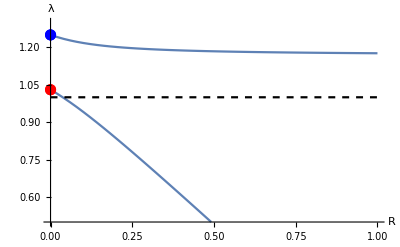

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
Factor[{λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}]

plot1=Show[
Plot[λ/.Solve[%[[1]]==0,λ],{R,0,1},PlotRange->{Automatic,{0.5,1.3}}],
ListPlot[{{0,%[[2]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,%[[3]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele a (blue) drives invasion and that invasion is possible regardless of linkage, despite the fact that the neo-W will then be further from the selected locus.

#### Increasing recombination with r = R [No haploid selection] EXAMPLE STARTING NEAR EQUIL A

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.5;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.,0.,1.,0.5},{0.6,0.75,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.0037]
```

{{0.00615531,0.00679615,0.992554,0.5},{0.547933,0.692835,0.0408107,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[2]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.0303,1.25}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.0037,0.0001}]
```

{{1.0303,1.25},{1.02965,1.24916},{1.02899,1.24832},{1.02833,1.24747},{1.02766,1.24661},{1.02699,1.24575},{1.02631,1.24488},{1.02563,1.24401},{1.02494,1.24312},{1.02424,1.24223},{1.02353,1.24133},{1.02282,1.24042},{1.0221,1.2395},{1.02138,1.23857},{1.02064,1.23763},{1.01989,1.23667},{1.01914,1.2357},{1.01837,1.23472},{1.01759,1.23372},{1.01679,1.23271},{1.01599,1.23168},{1.01516,1.23063},{1.01432,1.22955},{1.01346,1.22846},{1.01258,1.22733},{1.01168,1.22618},{1.01075,1.22499},{1.00979,1.22376},{1.00879,1.22249},{1.00776,1.22116},{1.00667,1.21977},{1.00553,1.21831},{1.00431,1.21675},{1.003,1.21507},{1.00156,1.21322},{0.999922,1.21112},{0.997947,1.20858},{0.99511,1.20492}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.0037,0.0001}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.0037,0.0001}]},{Transpose[tab][[2]]}]];
```

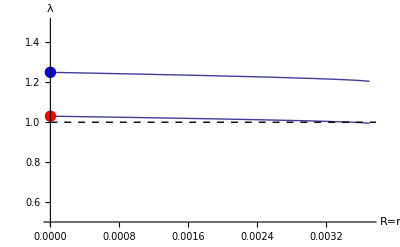

```mathematica
plot4=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.5,1.5}}],
ListPlot[eigen2,Joined->True,PlotStyle->Thick],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele a (blue) drives invasion.  But the system switches to the other equilibrium at R=r=0.0038.

At R=r=0.0037, there are two equilibria (see ordering of equilibrium values):  
	* allele a is favored in females and A is favored in males 
	* allele a is favored in females and a is favored in males

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.0037]
```

{{0.00615531,0.00679615,0.992554,0.5},{0.547933,0.692835,0.0408107,0.5}}

This shows that the eigenvalue associated with the neo-W and allele a (blue) drives invasion.  But the system switches to the other equilibrium at R=r=0.0038.

At R=r=0.0038, only the first remains:
	* allele a is favored in females and A is favored in males

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.0038]
```

{{0.00632135,0.00698018,0.992352,0.5}}

At the first equilibrium, recombination is selected against in this example:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.761905,0.97619}

### Adding haploid selection to cases with pure sexually antagonistic selection

#### Pure sexually antagonistic selection [No haploid selection] -> neo-W invades even though R>r

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable

```mathematica
sieve[tryFAA,tryFAa,0.5,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.876289,0.855131,0.,0.5}}

{0.89344-0.932299 R-1.89629 λ+1.01326 R λ+1. λ^2,1.02255,0.87374}

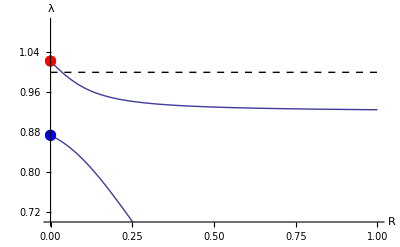

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
Factor[{λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}]

plot2=Show[
Plot[λ/.Solve[%[[1]]==0,λ],{R,0,1},PlotRange->{Automatic,{0.7,1.1}}],
ListPlot[{{0,%[[2]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,%[[3]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible only for a modest range of R values (still, R>r so this runs counter to the expectations in van Doorn and Kirkpatrick).

#### Pure sexually antagonistic selection with meiotic drive -> neo-W invades even though R>r

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.48;
tryαm=0.48;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.362667,0.312823,0.,0.506433}}

{0.994367-1.02231 R-1.99983 λ+1.07566 R λ+1. λ^2,1.07385,0.925985}

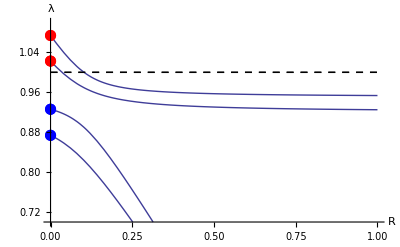

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
Factor[{λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma),λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}]

plot3=Show[
plot2,
Plot[λ/.Solve[%[[1]]==0,λ],{R,0,1},PlotRange->{Automatic,{0.7,1.1}},PlotStyle->Thick],
ListPlot[{{0,%[[2]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,%[[3]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R","λ"}
]
```

With a male biased sex ratio (thick), the eigenvalues are slightly larger than with no haploid selection (thin), but the pattern is similar.

#### Increasing recombination with r = R [No haploid selection] EXAMPLE STARTING NEAR EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.664804,0.623037,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.269049,0.204077,0.204077,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.02255,0.87374}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.87374,1.02255},{0.877268,1.02686},{0.879947,1.02901},{0.881772,1.02987},{0.882766,1.02986},{0.882963,1.02923},{0.882398,1.02816},{0.881108,1.02679},{0.879126,1.02523},{0.876489,1.02357},{0.87323,1.02187},{0.869383,1.02017},{0.864984,1.01853},{0.860067,1.01695},{0.854667,1.01546},{0.848819,1.01407},{0.842557,1.01279},{0.835912,1.0116},{0.828917,1.01052},{0.821601,1.00952},{0.813991,1.00862},{0.806112,1.0078},{0.797989,1.00706},{0.789641,1.00638},{0.781089,1.00577},{0.77235,1.00521},{0.76344,1.00471},{0.754373,1.00425},{0.745162,1.00384},{0.735819,1.00346},{0.726354,1.00312},{0.716778,1.0028},{0.707098,1.00252},{0.697322,1.00225},{0.687457,1.00202},{0.67751,1.0018},{0.667486,1.0016},{0.657391,1.00141},{0.647229,1.00124},{0.637006,1.00109},{0.626724,1.00095},{0.616387,1.00082},{0.606,1.00069},{0.595564,1.00058},{0.585083,1.00048},{0.57456,1.00038},{0.563997,1.00029},{0.553395,1.00021},{0.542758,1.00014},{0.532087,1.00007},{0.521383,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

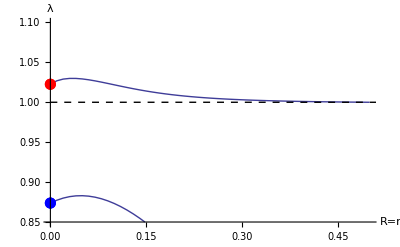

```mathematica
plot4=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.85,1.1}}],
ListPlot[eigen2,Joined->True,PlotStyle->Thick],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is now possible for all R=r<1/2.

#### Increasing recombination with r = R with meiotic drive in the heterogametic sex (causes a sex ratio distortion) EQUIL A

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.48;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.566667,0.511278,0.,0.510429}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.155911,0.108125,0.108125,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.06485,0.898573}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.898573,1.06485},{0.900415,1.06514},{0.901889,1.06428},{0.902922,1.06264},{0.903481,1.06044},{0.903554,1.05783},{0.903135,1.05492},{0.902222,1.05182},{0.900813,1.0486},{0.898908,1.04533},{0.896508,1.04206},{0.893613,1.03885},{0.890228,1.03574},{0.886359,1.03275},{0.882016,1.02992},{0.877211,1.02726},{0.871962,1.02478},{0.866287,1.02248},{0.860208,1.02036},{0.853747,1.01842},{0.84693,1.01664},{0.83978,1.01503},{0.832321,1.01356},{0.824576,1.01224},{0.816567,1.01103},{0.808314,1.00994},{0.799837,1.00896},{0.791154,1.00806},{0.782281,1.00725},{0.773233,1.00652},{0.764023,1.00586},{0.754663,1.00525},{0.745165,1.0047},{0.735539,1.0042},{0.725795,1.00375},{0.715939,1.00333},{0.705981,1.00295},{0.695927,1.00261},{0.685783,1.00229},{0.675554,1.002},{0.665247,1.00174},{0.654866,1.00149},{0.644415,1.00127},{0.633899,1.00106},{0.62332,1.00087},{0.612683,1.00069},{0.60199,1.00053},{0.591245,1.00038},{0.58045,1.00025},{0.569608,1.00012},{0.55872,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

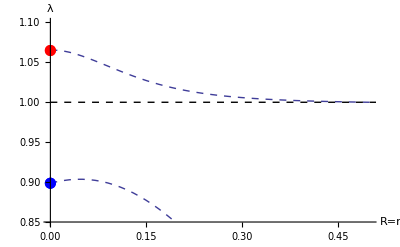

```mathematica
plot5=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Dashed,PlotRange->{Automatic,{0.85,1.1}}],
ListPlot[eigen2,Joined->True,PlotStyle->Dashed],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is now possible for all R=r<1/2.

#### Increasing recombination with r = R with meiotic drive in the homogametic sex (causes a drive) EQUIL A

The neo-W with allele A can invade in this example of directional selection (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=17.5/17;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.52;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{0.873743,0.852223,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.421524,0.332718,0.332718,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.01701,0.852685}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.852685,1.01701},{0.853802,1.02448},{0.854965,1.02736},{0.855586,1.02862},{0.855552,1.02895},{0.854834,1.02865},{0.853437,1.02792},{0.851379,1.0269},{0.848689,1.02568},{0.8454,1.02435},{0.841545,1.02295},{0.83716,1.02153},{0.832281,1.02012},{0.826942,1.01875},{0.821178,1.01743},{0.815021,1.01617},{0.808502,1.01498},{0.801651,1.01386},{0.794494,1.01281},{0.787058,1.01183},{0.779366,1.01092},{0.771439,1.01007},{0.763298,1.00928},{0.754961,1.00855},{0.746445,1.00787},{0.737764,1.00724},{0.728932,1.00666},{0.719961,1.00611},{0.710863,1.00561},{0.701649,1.00514},{0.692326,1.00471},{0.682904,1.0043},{0.673391,1.00392},{0.663792,1.00357},{0.654115,1.00324},{0.644366,1.00293},{0.634548,1.00264},{0.624667,1.00237},{0.614728,1.00212},{0.604735,1.00188},{0.59469,1.00166},{0.584598,1.00144},{0.574461,1.00125},{0.564282,1.00106},{0.554064,1.00088},{0.54381,1.00071},{0.53352,1.00055},{0.523198,1.0004},{0.512845,1.00026},{0.502464,1.00013},{0.492055,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

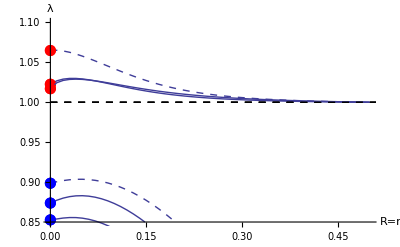

```mathematica
plot6=Show[
plot5,plot4,
ListPlot[eigen1,Joined->True],
ListPlot[eigen2,Joined->True],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

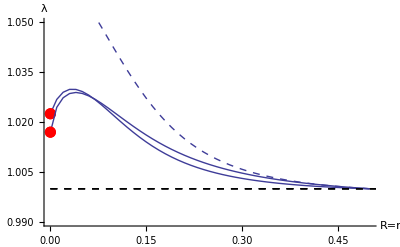

```mathematica
Show[%,PlotRange->{{0,0.5},{0.99,1.05}}]
```

The two thin curves converge with increasing recombination rate (consistent with α<1/2 in the heterogametic sex being equivalent to α>1/2 in the homogametic sex).  Setting tryαf=0.48 and reentering this section shows a much worse fit.

#### Increasing recombination with r = R [No haploid selection] EXAMPLE STARTING NEAR EQUIL B

The neo-W with allele A cannot invade in this example of sexually antagonistic selection:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.7;
tryMAA=0.9;
tryMAa=1;
tryMaa=1.1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.919462,0.901742,0.901742,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.954545,0.772727}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.772727,0.954545},{0.780853,0.964808},{0.787704,0.97175},{0.792794,0.976982},{0.796054,0.981064},{0.797558,0.984308},{0.79745,0.986921},{0.795908,0.989048},{0.793121,0.990795},{0.789275,0.992239},{0.784541,0.993439},{0.779068,0.99444},{0.772985,0.995277},{0.766402,0.995978},{0.759409,0.996567},{0.752079,0.997063},{0.744474,0.99748},{0.73664,0.997833},{0.728619,0.998131},{0.720441,0.998384},{0.712134,0.9986},{0.703718,0.998784},{0.69521,0.998942},{0.686624,0.999077},{0.677972,0.999194},{0.669264,0.999295},{0.660507,0.999382},{0.651709,0.999458},{0.642874,0.999524},{0.634007,0.999582},{0.625112,0.999633},{0.616193,0.999678},{0.607253,0.999717},{0.598293,0.999752},{0.589317,0.999783},{0.580325,0.99981},{0.57132,0.999834},{0.562303,0.999856},{0.553275,0.999875},{0.544236,0.999893},{0.535189,0.999908},{0.526134,0.999922},{0.517072,0.999935},{0.508002,0.999946},{0.498927,0.999956},{0.489846,0.999966},{0.48076,0.999974},{0.471669,0.999981},{0.462573,0.999988},{0.453474,0.999994},{0.44437,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

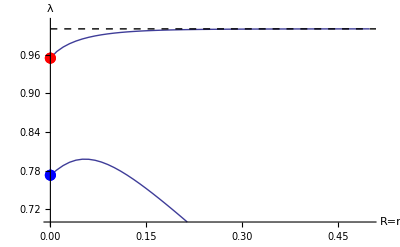

```mathematica
plot4=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.7,1.01}}],
ListPlot[eigen2,Joined->True,PlotStyle->Thick,PlotRange->All],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that invasion is not possible for all R=r<1/2.

#### Increasing recombination with r = R with meiotic drive in the heterogametic sex (causes a sex ratio distortion) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic selection (due to reducing the sex ratio skew).

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.7;
tryMAA=0.9;
tryMAa=1;
tryMaa=1.1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.48;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.52}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.765152,0.708242,0.708242,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.992424,0.799242}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.799242,0.992424},{0.800112,0.999653},{0.801934,1.0028},{0.80308,1.00458},{0.803282,1.00558},{0.802479,1.00607},{0.800687,1.00622},{0.797962,1.00616},{0.79438,1.00596},{0.790025,1.00568},{0.784983,1.00536},{0.779338,1.00502},{0.773168,1.00468},{0.766543,1.00435},{0.759527,1.00403},{0.752175,1.00374},{0.744535,1.00346},{0.736648,1.00321},{0.728551,1.00297},{0.720274,1.00275},{0.711842,1.00255},{0.703278,1.00237},{0.6946,1.00219},{0.685823,1.00203},{0.676961,1.00189},{0.668026,1.00175},{0.659026,1.00162},{0.649971,1.0015},{0.640868,1.00139},{0.631721,1.00128},{0.622538,1.00118},{0.613321,1.00109},{0.604075,1.001},{0.594803,1.00092},{0.585509,1.00084},{0.576194,1.00077},{0.56686,1.0007},{0.557511,1.00063},{0.548146,1.00057},{0.538769,1.00051},{0.52938,1.00045},{0.519979,1.0004},{0.510569,1.00035},{0.501151,1.0003},{0.491724,1.00025},{0.48229,1.0002},{0.472849,1.00016},{0.463402,1.00012},{0.453949,1.00008},{0.444491,1.00004},{0.435029,1.}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

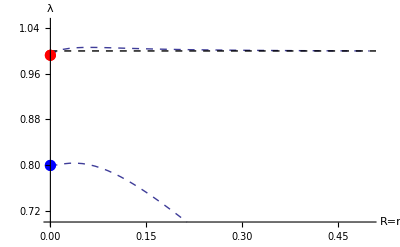

```mathematica
plot5=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Dashed,PlotRange->{Automatic,{0.7,1.05}}],
ListPlot[eigen2,Joined->True,PlotStyle->Dashed],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is now possible for an intermediate range of R=r.

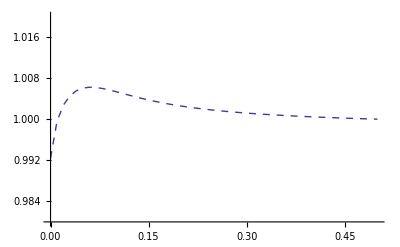

```mathematica
ListPlot[eigen2,Joined->True,PlotStyle->Dashed,PlotRange->{Automatic,{0.98,1.02}}]
```

#### Increasing recombination with r = R with meiotic drive in the homogametic sex (causes a drive) EQUIL B

The neo-W with allele A cannot invade in this example of sexually antagonistic selection:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.7;
tryMAA=0.9;
tryMAa=1;
tryMaa=1.1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.52;
tryαm=0.5;
tryr=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilA0 is stable for the entire range of r (0 to 0.5):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.25]
```

{{0.995002,0.993538,0.991715,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.972727,0.754545}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryr/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.25,0.01}]
```

{{0.754545,0.972727},{0.761738,0.97849},{0.767625,0.982844},{0.771978,0.986239},{0.774737,0.988926},{0.775941,0.991074},{0.775689,0.992806},{0.77412,0.994215},{0.771394,0.995368},{0.767672,0.996314},{0.763109,0.99709},{0.757847,0.997725},{0.752011,0.998242},{0.745707,0.998658},{0.739024,0.998991},{0.732036,0.999253},{0.724801,0.999457},{0.717368,0.999614},{0.709774,0.999733},{0.702048,0.999821},{0.694217,0.999885},{0.686297,0.99993},{0.678304,0.999961},{0.670251,0.99998},{0.662148,0.999992},{0.654001,0.999998}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.25,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.25,0.01}]},{Transpose[tab][[2]]}]];
```

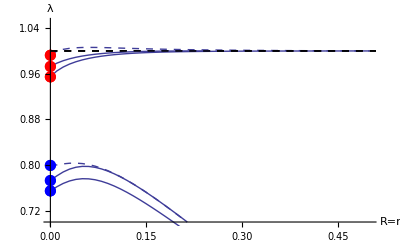

```mathematica
plot6=Show[
plot5,plot4,
ListPlot[eigen1,Joined->True],
ListPlot[eigen2,Joined->True],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"R=r","λ"}
]
```

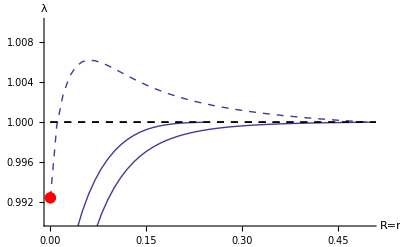

```mathematica
Show[%,PlotRange->{{0,0.5},{0.99,1.01}}]
```

The two thin curves converge with increasing recombination rate (consistent with α<1/2 in the heterogametic sex being equivalent to α>1/2 in the homogametic sex).  Setting tryαf=0.52 and reentering this section shows a much worse fit.

But for tight linkage, only the sex ratio advantage is strong enough to drive the neo-W in.

#### Increasing recombination r (R=0.1) [No haploid selection] EXAMPLE STARTING NEAR EQUIL A [Hard to interpret because changing r alters initial equilibrium]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
tryR=0.1;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilB0 is initially stable and a polymorphism is sustained for all r:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.532327,0.467673,0.467673,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.97619,0.857143}

These are the points at R=r=0.  For tryR, we assume that the association with A is still leading:

```mathematica
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{0.945275,0.79282}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.79282,0.945275},{0.799902,0.952754},{0.806588,0.960212},{0.812753,0.967272},{0.818309,0.973746},{0.823228,0.979551},{0.827531,0.984677},{0.831266,0.989162},{0.834498,0.993067},{0.837295,0.996462},{0.83972,0.999418},{0.84183,1.002},{0.843673,1.00426},{0.845292,1.00625},{0.84672,1.00801},{0.847986,1.00957},{0.849115,1.01096},{0.850125,1.01222},{0.851034,1.01334},{0.851855,1.01436},{0.852599,1.01528},{0.853277,1.01613},{0.853896,1.0169},{0.854464,1.0176},{0.854986,1.01825},{0.855467,1.01885},{0.855913,1.01941},{0.856326,1.01992},{0.85671,1.0204},{0.857068,1.02085},{0.857403,1.02127},{0.857715,1.02166},{0.858009,1.02203},{0.858285,1.02237},{0.858544,1.0227},{0.858789,1.023},{0.85902,1.02329},{0.859239,1.02357},{0.859446,1.02382},{0.859642,1.02407},{0.859828,1.0243},{0.860005,1.02453},{0.860174,1.02474},{0.860335,1.02494},{0.860488,1.02513},{0.860635,1.02531},{0.860775,1.02549},{0.860909,1.02566},{0.861037,1.02582},{0.86116,1.02597},{0.861278,1.02612}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

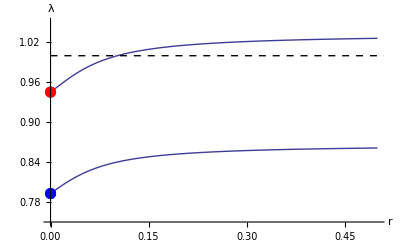

```mathematica
plot4=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.75,1.05}}],
ListPlot[eigen2,Joined->True,PlotStyle->Thick],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

#### Increasing recombination r (R=0.1) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.49;
tryr=0;
tryR=0.1;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilB0 is initially stable and a polymorphism is sustained for all r:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.51}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.480398,0.411355,0.411355,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.995627,0.872692}

These are the points at R=r=0.  For tryR, we assume that the association with A is still leading:

```mathematica
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{0.963156,0.807981}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.807981,0.963156},{0.813556,0.968251},{0.81905,0.974042},{0.824177,0.979681},{0.828842,0.984944},{0.833016,0.989736},{0.836707,0.99403},{0.83995,0.997841},{0.842791,1.00121},{0.845279,1.00417},{0.847459,1.00679},{0.849376,1.00909},{0.851067,1.01114},{0.852565,1.01296},{0.853897,1.01458},{0.855087,1.01603},{0.856155,1.01734},{0.857116,1.01851},{0.857986,1.01958},{0.858775,1.02055},{0.859495,1.02144},{0.860152,1.02225},{0.860756,1.023},{0.861311,1.02368},{0.861823,1.02432},{0.862297,1.0249},{0.862737,1.02545},{0.863145,1.02596},{0.863526,1.02643},{0.863882,1.02687},{0.864216,1.02729},{0.864528,1.02768},{0.864822,1.02804},{0.865098,1.02839},{0.865359,1.02871},{0.865605,1.02902},{0.865837,1.02931},{0.866058,1.02958},{0.866267,1.02985},{0.866465,1.03009},{0.866654,1.03033},{0.866833,1.03055},{0.867005,1.03077},{0.867168,1.03097},{0.867324,1.03117},{0.867473,1.03136},{0.867616,1.03153},{0.867752,1.03171},{0.867883,1.03187},{0.868009,1.03203},{0.86813,1.03218}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

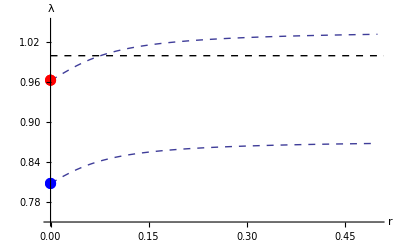

```mathematica
plot5=Show[
ListPlot[eigen1,Joined->True,PlotStyle->Dashed,PlotRange->{Automatic,{0.75,1.05}}],
ListPlot[eigen2,Joined->True,PlotStyle->Dashed],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"r","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

#### Increasing recombination r (R=0.1) with meiotic drive in homogametic sex (causes a drive) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.8;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.51;
tryαm=0.5;
tryr=0;
tryR=0.1;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, equilB0 is initially stable and a polymorphism is sustained for all r:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0]
```

{{1.,1.,0.,0.5}}

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0.5]
```

{{0.588645,0.519602,0.519602,0.5}}

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.985714,0.847619}

These are the points at R=r=0.  For tryR, we assume that the association with A is still leading:

```mathematica
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{0.952136,0.78596}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryr,0,0.5,0.01}]
```

{{0.78596,0.952136},{0.791708,0.95851},{0.797393,0.965066},{0.802771,0.971411},{0.807716,0.977339},{0.812169,0.98274},{0.816118,0.987574},{0.819584,0.991848},{0.822608,0.995599},{0.82524,0.99888},{0.827531,1.00175},{0.829527,1.00425},{0.831272,1.00645},{0.832804,1.00838},{0.834153,1.01009},{0.835348,1.0116},{0.83641,1.01294},{0.837358,1.01415},{0.838208,1.01523},{0.838974,1.0162},{0.839667,1.01708},{0.840295,1.01788},{0.840867,1.01861},{0.841391,1.01928},{0.84187,1.01989},{0.842312,1.02046},{0.842719,1.02098},{0.843095,1.02146},{0.843444,1.0219},{0.843769,1.02232},{0.844071,1.0227},{0.844353,1.02306},{0.844617,1.0234},{0.844864,1.02372},{0.845097,1.02402},{0.845315,1.0243},{0.845521,1.02456},{0.845716,1.02481},{0.845899,1.02504},{0.846073,1.02527},{0.846238,1.02548},{0.846395,1.02568},{0.846543,1.02587},{0.846685,1.02605},{0.846819,1.02622},{0.846948,1.02639},{0.84707,1.02654},{0.847188,1.02669},{0.8473,1.02684},{0.847407,1.02697},{0.84751,1.02711}}

```mathematica
eigen1=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryr,{tryr,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

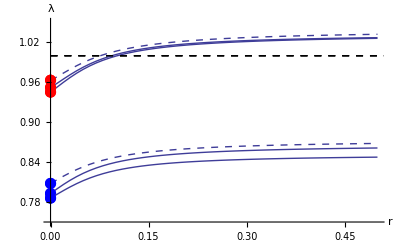

```mathematica
plot6=Show[
plot5,plot4,
ListPlot[eigen1,Joined->True],
ListPlot[eigen2,Joined->True],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Dashed,Black}],
AxesLabel->{"r","λ"},PlotRange->{{0,0.5},{0.75,1.05}}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

### Potential figure - Increasing recombination R (r=0.05 or 0.2)

#### Summary

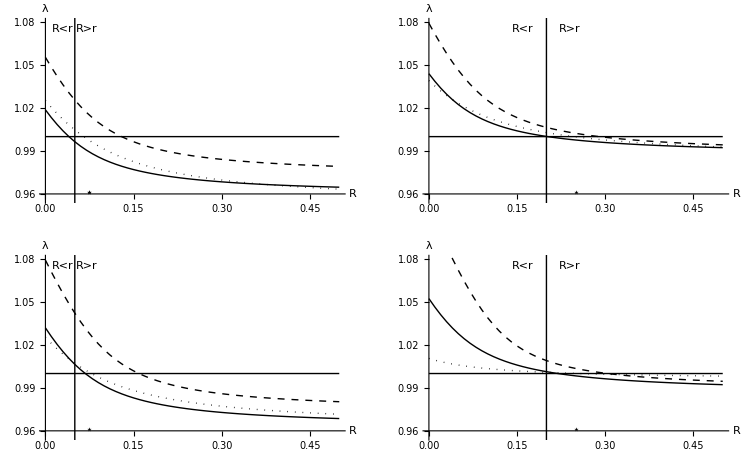

```mathematica
GraphicsGrid[{{plotA,plotB},{plotC,plotD}}]
```

```mathematica
Export["~/Desktop/Temp.pdf",%,ImageSize->Large];
```

Legend: Haploid selection and linkage both impact invasion of neo-W into XY sex dermination systems. Main panels plot the leading eigenvalue, λ, for a neo-W as a function of its distance, R, to the selected A locus: with only sexually antagonistic selection (thick curves), adding meiotic drive in males (dashed; αm=0.45); or adding meiotic drive in females (dashed; αf=0.55).  Either form of haploid selection increases the parameter space in which neo-W chromosomes invade (expanding when λ > 1).  Even in the absence of haploid selection, the condition of Van Doorn and Kirkpatrick for neo-W invasion is not satisfied if the sex determining region is initially tightly linked to the A locus (left panels: r = 0.05), but it is appoximately satisfied when linkage is loose (right panels: r=0.2), as seen by the thick curve hitting λ=1 at R = r (crossing thin lines). Inset panels show simulations for a neo-W that is more loosely linked than the original sex determining gene (R given by the asterisk), illustrating the frequency of the Y in males (upper green inset) and the frequency of males (bottom blue inset).  A neo-W that is less linked to the selected locus (R>r) can spread when it equalizes the sex ratio caused by meiotic drive in males (dashed curves) but also when it becomes associated with the driven allele in females, causing the sex ratio to become skewed (dotted curves).

TO DO:  Import into Adobe Illustrator.  Add panel labels and make dotted curves look more dotted.  Add xy-labels to the inset plots.  Top: x=1-500000 (log axis), y=0-1. Bottom: x=1-10000 (log axis), y=0.49-0.51 (left) and 0.498-0.502 (right).

POINT OUT IN TEXT:  
* In the appendix, it’s mentioned that with sexually antagonistic selection only and r tight at equil B (top plots), a neo-W cannot invade because “the X is already as possible for the female beneficial allele”.  This can be seen because the neo-W cannot invade with tight linkage near R=r in panel A (thick curve lies below λ=1). At equil A (bottom plots), a neo-W can spread because of the advantage of becoming better associated with the female beneficial allele (thick curve lies above λ=1).
* Panel D with meiotic drive in females (dashed; αf=0.55) is an example where neo-W spreads but does not fix.

Parameters: 
tryFAA=tryMaa=1.05;
tryFAa=1;
tryMAa=1 (top panels, equil near B) or 0.925 (bottom panels, equil near A)
tryFaa=tryMAA=0.85;
trywAf=trywaf=trywAm=trywam=1;
tryαf=0.5; [unless noted]
tryαm=0.5; [unless noted]

#### Increasing recombination R (r=0.05) [No haploid selection] EXAMPLE STARTING NEAR EQUIL B [In the absence of haploid selection, R<r is predictive, but haploid selection allows invasion with R>r]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.671004,0.632712,0.241726,0.5}}

If R=r=0 (emanates from equilibrium B):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,1.,0,0.5}

{0.97619,0.880952}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.00286,0.89897}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.89897,1.00286},{0.89441,0.997607},{0.889385,0.99282},{0.883898,0.988495},{0.877964,0.984616},{0.871609,0.98116},{0.864864,0.978093},{0.857766,0.975378},{0.850353,0.972979},{0.842662,0.970858},{0.834727,0.96898},{0.826581,0.967315},{0.81825,0.965833},{0.80976,0.964511},{0.801131,0.963328},{0.792382,0.962265},{0.783529,0.961306},{0.774583,0.960439},{0.765558,0.959652},{0.756463,0.958935},{0.747306,0.95828},{0.738094,0.95768},{0.728834,0.957128},{0.719531,0.956619},{0.710189,0.956149},{0.700813,0.955713},{0.691405,0.955308},{0.68197,0.954931},{0.67251,0.954579},{0.663027,0.954251},{0.653523,0.953942},{0.644,0.953653},{0.634459,0.953381},{0.624903,0.953125},{0.615333,0.952884},{0.605749,0.952655},{0.596153,0.952439},{0.586546,0.952235},{0.576928,0.95204},{0.5673,0.951856},{0.557663,0.951681},{0.548018,0.951513},{0.538365,0.951354},{0.528705,0.951202},{0.519038,0.951057},{0.509365,0.950918},{0.499686,0.950785},{0.490001,0.950658},{0.480311,0.950536},{0.470616,0.950419},{0.460916,0.950306}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

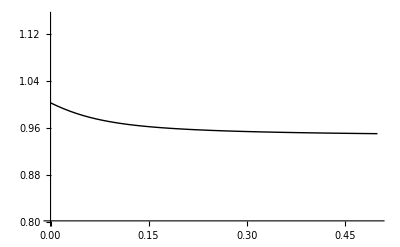

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

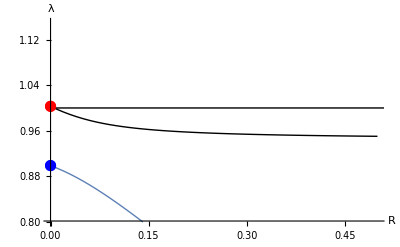

```mathematica
Show[
plot4,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.025;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504153},{6,0.504087},{6,0.504087},{7,0.504024},{7,0.504024},{8,0.503964},{9,0.503907},{10,0.503853},{11,0.503801},{12,0.503752},{14,0.503658},{15,0.503614},{17,0.503529},{18,0.503488},{20,0.503409},{22,0.503334},{25,0.503227},{27,0.503158},{30,0.503058},{33,0.502962},{37,0.50284},{41,0.502723},{45,0.502611},{50,0.502478},{55,0.502351},{61,0.502207},{67,0.502072},{74,0.501924},{82,0.501768},{91,0.501607},{100,0.501461},{111,0.5013},{123,0.501144},{136,0.500995},{150,0.500857},{166,0.500722},{183,0.500601},{202,0.50049},{224,0.500387},{247,0.500302},{273,0.500228},{302,0.500167},{333,0.500119},{368,0.500082},{407,0.500053},{450,0.500034},{497,0.50002},{550,0.500011},{608,0.500006},{671,0.500003},{742,0.500001},{820,0.500001},{906,0.5},{1002,0.5},{1107,0.5},{1223,0.5},{1352,0.5},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

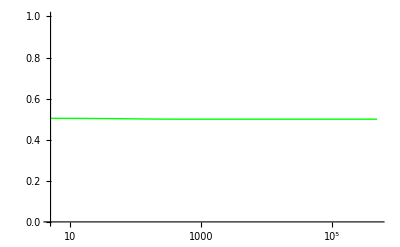

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

{{5,0.499687},{6,0.499719},{6,0.499719},{7,0.499746},{7,0.499746},{8,0.499771},{9,0.499792},{10,0.499811},{11,0.499827},{12,0.499842},{14,0.499866},{15,0.499876},{17,0.499894},{18,0.499901},{20,0.499913},{22,0.499924},{25,0.499935},{27,0.499942},{30,0.499949},{33,0.499954},{37,0.49996},{41,0.499964},{45,0.499967},{50,0.49997},{55,0.499972},{61,0.499974},{67,0.499976},{74,0.499978},{82,0.49998},{91,0.499981},{100,0.499983},{111,0.499985},{123,0.499987},{136,0.499988},{150,0.49999},{166,0.499992},{183,0.499993},{202,0.499994},{224,0.499995},{247,0.499996},{273,0.499997},{302,0.499998},{333,0.499999},{368,0.499999},{407,0.499999},{450,0.5},{497,0.5},{550,0.5},{608,0.5},{671,0.5},{742,0.5},{820,0.5},{906,0.5},{1002,0.5},{1107,0.5},{1223,0.5},{1352,0.5},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

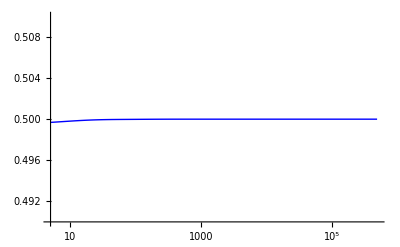

```mathematica
SRtab4=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset4=ListLogLinearPlot[SRtab4,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Blue}]
```

#### Increasing recombination R (r=0.05) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.475;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.552535,0.503247,0.147601,0.509049}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.02686,0.922851}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.05535,0.933026}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.933026,1.05535},{0.929481,1.04851},{0.925519,1.04209},{0.921112,1.03611},{0.916242,1.03059},{0.910902,1.02555},{0.905095,1.02097},{0.898836,1.01684},{0.892148,1.01314},{0.885062,1.00984},{0.877614,1.0069},{0.869839,1.00429},{0.861774,1.00197},{0.853453,0.999906},{0.844907,0.998065},{0.836165,0.996422},{0.827251,0.994949},{0.818187,0.993627},{0.808993,0.992435},{0.799684,0.991358},{0.790275,0.99038},{0.780778,0.989491},{0.771203,0.98868},{0.761559,0.987938},{0.751855,0.987256},{0.742096,0.986628},{0.732289,0.986049},{0.722439,0.985513},{0.71255,0.985015},{0.702627,0.984553},{0.692672,0.984122},{0.682688,0.983719},{0.672678,0.983343},{0.662645,0.98299},{0.65259,0.982658},{0.642516,0.982346},{0.632424,0.982052},{0.622315,0.981774},{0.612191,0.981512},{0.602053,0.981264},{0.591903,0.981028},{0.58174,0.980805},{0.571566,0.980593},{0.561382,0.980391},{0.551188,0.980198},{0.540985,0.980015},{0.530774,0.97984},{0.520555,0.979673},{0.510329,0.979513},{0.500096,0.979359},{0.489856,0.979213}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

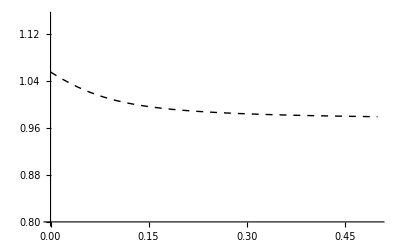

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

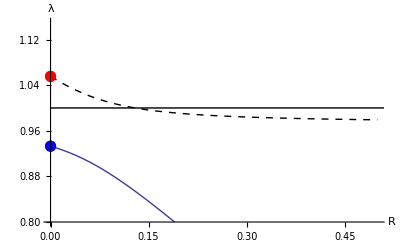

```mathematica
Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.513565},{6,0.513571},{6,0.513571},{7,0.513582},{7,0.513582},{8,0.513598},{9,0.51362},{10,0.513646},{11,0.513676},{12,0.513711},{14,0.513791},{15,0.513836},{17,0.513936},{18,0.513989},{20,0.514104},{22,0.514229},{25,0.51443},{27,0.514574},{30,0.514803},{33,0.515047},{37,0.515394},{41,0.515765},{45,0.516161},{50,0.516691},{55,0.517262},{61,0.518004},{67,0.518812},{74,0.519845},{82,0.521157},{91,0.522817},{100,0.524695},{111,0.527322},{123,0.530659},{136,0.534911},{150,0.540334},{166,0.547756},{183,0.557258},{202,0.570047},{224,0.587852},{247,0.609736},{273,0.637659},{302,0.670886},{333,0.706149},{368,0.742885},{407,0.77822},{450,0.81016},{497,0.837823},{550,0.86196},{608,0.882111},{671,0.898771},{742,0.913036},{820,0.924935},{906,0.934939},{1002,0.943479},{1107,0.950655},{1223,0.956782},{1352,0.962066},{1494,0.966596},{1651,0.970515},{1825,0.973923},{2017,0.976886},{2229,0.979471},{2464,0.981743},{2723,0.983733},{3009,0.985485},{3326,0.987036},{3675,0.988403},{4062,0.98962},{4489,0.990698},{4961,0.991657},{5483,0.992512},{6060,0.993275},{6697,0.993955},{7401,0.994564},{8180,0.995109},{9040,0.995597},{9991,0.996034},{11042,0.996427},{12203,0.99678},{13486,0.997096},{14905,0.997381},{16472,0.997637},{18205,0.997868},{20119,0.998076},{22235,0.998263},{24574,0.998431},{27158,0.998583},{30015,0.99872},{33171,0.998844},{36660,0.998955},{40515,0.999056},{44776,0.999147},{49486,0.999229},{54690,0.999303},{60442,0.99937},{66799,0.99943},{73824,0.999485},{81588,0.999534},{90169,0.999579},{99652,0.999619},{110132,0.999656},{121715,0.999689},{134516,0.999718},{148663,0.999745},{164298,0.99977},{181578,0.999792},{200674,0.999811},{221779,0.999829},{245104,0.999846},{270882,0.99986},{299371,0.999874},{330856,0.999886},{365652,0.999897},{404108,0.999906},{446609,0.999915},{493579,0.999923}}

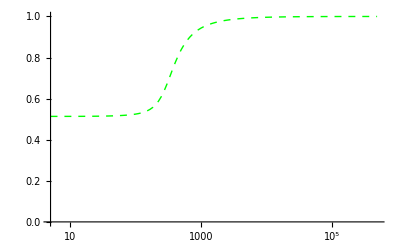

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dashed,Green}]
```

{{5,0.508365},{6,0.508383},{6,0.508383},{7,0.508398},{7,0.508398},{8,0.50841},{9,0.508419},{10,0.508426},{11,0.508431},{12,0.508434},{14,0.508436},{15,0.508436},{17,0.508433},{18,0.50843},{20,0.508423},{22,0.508413},{25,0.508396},{27,0.508383},{30,0.508361},{33,0.508336},{37,0.508301},{41,0.508261},{45,0.508219},{50,0.508161},{55,0.508098},{61,0.508017},{67,0.507929},{74,0.507816},{82,0.507675},{91,0.507499},{100,0.507303},{111,0.507034},{123,0.506703},{136,0.506297},{150,0.505803},{166,0.505168},{183,0.504422},{202,0.503527},{224,0.502468},{247,0.501431},{273,0.500463},{302,0.499732},{333,0.499332},{368,0.499202},{407,0.499248},{450,0.499368},{497,0.4995},{550,0.499617},{608,0.499711},{671,0.499782},{742,0.499836},{820,0.499877},{906,0.499906},{1002,0.499929},{1107,0.499946},{1223,0.499958},{1352,0.499968},{1494,0.499975},{1651,0.49998},{1825,0.499985},{2017,0.499988},{2229,0.49999},{2464,0.499992},{2723,0.499994},{3009,0.499995},{3326,0.499996},{3675,0.499997},{4062,0.499998},{4489,0.499998},{4961,0.499998},{5483,0.499999},{6060,0.499999},{6697,0.499999},{7401,0.499999},{8180,0.499999},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

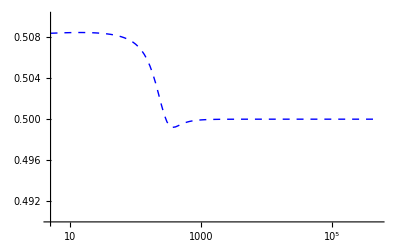

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Dashed,Blue}]
```

#### Increasing recombination R (r=0.05) with meiotic drive in homogametic sex (causes a drive) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.525;
tryαm=0.5;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.807255,0.767691,0.280079,0.5}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,0.857143}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.02512,0.881007}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.881007,1.02512},{0.875983,1.0204},{0.870633,1.01601},{0.864963,1.01195},{0.858983,1.00819},{0.852706,1.00472},{0.846149,1.00154},{0.83933,0.998619},{0.832267,0.995943},{0.824979,0.993491},{0.817485,0.991245},{0.809804,0.989187},{0.801952,0.987299},{0.793944,0.985566},{0.785797,0.983974},{0.777523,0.982508},{0.769135,0.981157},{0.760643,0.979909},{0.752058,0.978754},{0.743388,0.977685},{0.734641,0.976691},{0.725825,0.975768},{0.716946,0.974907},{0.708009,0.974104},{0.69902,0.973354},{0.689983,0.972651},{0.680903,0.971992},{0.671782,0.971372},{0.662625,0.97079},{0.653434,0.970241},{0.644213,0.969723},{0.634962,0.969233},{0.625686,0.96877},{0.616384,0.968332},{0.607061,0.967916},{0.597716,0.967521},{0.588352,0.967145},{0.578969,0.966788},{0.56957,0.966447},{0.560155,0.966123},{0.550725,0.965813},{0.541282,0.965517},{0.531825,0.965233},{0.522357,0.964962},{0.512877,0.964702},{0.503386,0.964453},{0.493885,0.964214},{0.484375,0.963985},{0.474856,0.963764},{0.465329,0.963552},{0.455793,0.963347}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

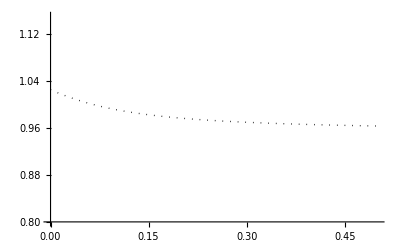

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

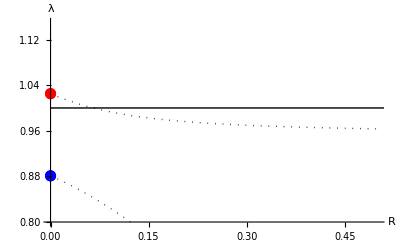

```mathematica
Show[
plot6,
ListPlot[eigen1,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion occurs over a broader parameter space if it evens the sex ratio (dashed) but also when it causes the sex ratio to depart from 1/2 (thin).

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504185},{6,0.504148},{6,0.504148},{7,0.504117},{7,0.504117},{8,0.50409},{9,0.504065},{10,0.504044},{11,0.504025},{12,0.504007},{14,0.503976},{15,0.503962},{17,0.503937},{18,0.503925},{20,0.503902},{22,0.503881},{25,0.50385},{27,0.50383},{30,0.5038},{33,0.50377},{37,0.503731},{41,0.503692},{45,0.503653},{50,0.503604},{55,0.503556},{61,0.503499},{67,0.503443},{74,0.503378},{82,0.503305},{91,0.503226},{100,0.503148},{111,0.503055},{123,0.502957},{136,0.502854},{150,0.502748},{166,0.50263},{183,0.502511},{202,0.502385},{224,0.502246},{247,0.502109},{273,0.501965},{302,0.501815},{333,0.501667},{368,0.501515},{407,0.501362},{450,0.50121},{497,0.501064},{550,0.50092},{608,0.500785},{671,0.50066},{742,0.500543},{820,0.500438},{906,0.500346},{1002,0.500266},{1107,0.500199},{1223,0.500145},{1352,0.500102},{1494,0.500069},{1651,0.500045},{1825,0.500028},{2017,0.500016},{2229,0.500009},{2464,0.500005},{2723,0.500002},{3009,0.500001},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

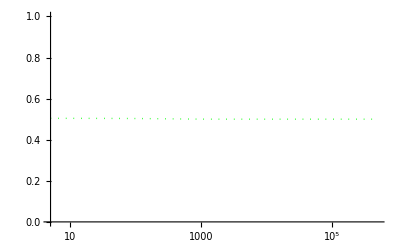

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.499374},{6,0.499397},{6,0.499397},{7,0.499418},{7,0.499418},{8,0.499437},{9,0.499455},{10,0.499471},{11,0.499486},{12,0.4995},{14,0.499525},{15,0.499536},{17,0.499555},{18,0.499564},{20,0.499579},{22,0.499592},{25,0.499608},{27,0.499617},{30,0.499628},{33,0.499637},{37,0.499647},{41,0.499655},{45,0.499661},{50,0.499667},{55,0.499673},{61,0.499679},{67,0.499685},{74,0.499691},{82,0.499697},{91,0.499704},{100,0.499711},{111,0.49972},{123,0.499728},{136,0.499738},{150,0.499747},{166,0.499758},{183,0.499768},{202,0.49978},{224,0.499792},{247,0.499805},{273,0.499818},{302,0.499832},{333,0.499845},{368,0.499859},{407,0.499873},{450,0.499887},{497,0.499901},{550,0.499914},{608,0.499926},{671,0.499938},{742,0.499949},{820,0.499959},{906,0.499967},{1002,0.499975},{1107,0.499981},{1223,0.499986},{1352,0.49999},{1494,0.499994},{1651,0.499996},{1825,0.499997},{2017,0.499998},{2229,0.499999},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

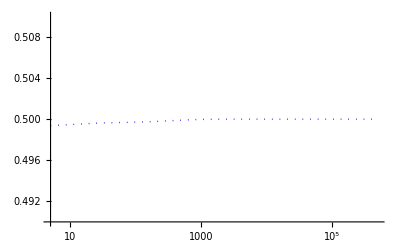

```mathematica
SRtab6=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset6=ListLogLinearPlot[SRtab6,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Dotted,Blue}]
```

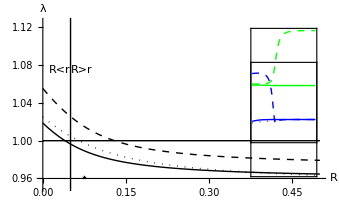

```mathematica
plotA=Show[
plot4,plot5,plot6,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
Graphics[Inset[Show[SRinset4,SRinset5,SRinset6,FrameTicks->False,Frame->True],{0.43,1.02},Center,{0.14,0.14}]],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
ListPlot[{{0.05,0},{0.05,2}},Joined->True,PlotStyle->{Thin,Black}],
Graphics[Text[Style["⋆",Large],{0.075,0.96}]],
Graphics[Text[Style["⋆",Large],{0.075,0.96}]],
Graphics[Text[Style["R<r",Medium],{0.03,1.075}]],
Graphics[Text[Style["R>r",Medium],{0.07,1.075}]],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.08}},AxesOrigin->{0,0.96}
]
```

#### Increasing recombination R (r=0.2) [No haploid selection] EXAMPLE STARTING NEAR EQUIL B [In the absence of haploid selection, R<r is predictive, but haploid selection allows invasion with R>r]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.2;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.549741,0.500248,0.421738,0.5}}

If R=r=0 (emanates from equilibrium B):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,1.,0.,0.5}

{0.97619,0.880952}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.04393,0.937909}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.937909,1.04393},{0.93296,1.03868},{0.92752,1.03391},{0.921597,1.02963},{0.915214,1.02581},{0.908402,1.02242},{0.901197,1.01942},{0.893641,1.01677},{0.885772,1.01443},{0.877631,1.01237},{0.869251,1.01055},{0.860665,1.00893},{0.8519,1.00749},{0.84298,1.00621},{0.833926,1.00506},{0.824756,1.00402},{0.815485,1.00309},{0.806126,1.00224},{0.796689,1.00148},{0.787184,1.00078},{0.77762,1.00014},{0.768003,0.999551},{0.758339,0.999011},{0.748633,0.998512},{0.73889,0.998051},{0.729113,0.997624},{0.719307,0.997227},{0.709473,0.996856},{0.699615,0.996511},{0.689734,0.996187},{0.679833,0.995884},{0.669914,0.995599},{0.659978,0.995331},{0.650026,0.995078},{0.64006,0.99484},{0.630082,0.994615},{0.620091,0.994401},{0.610089,0.994199},{0.600077,0.994007},{0.590055,0.993825},{0.580025,0.993651},{0.569986,0.993486},{0.55994,0.993328},{0.549886,0.993177},{0.539826,0.993033},{0.529759,0.992896},{0.519687,0.992764},{0.509609,0.992638},{0.499526,0.992517},{0.489439,0.9924},{0.479346,0.992289}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

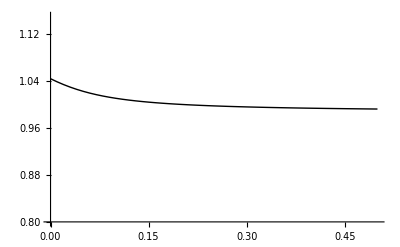

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

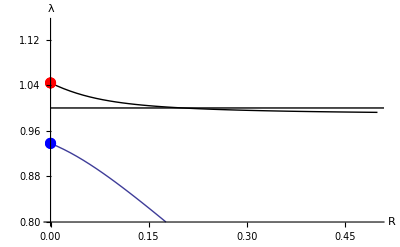

```mathematica
Show[
plot4,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.25;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504592},{6,0.504628},{6,0.504628},{7,0.504647},{7,0.504647},{8,0.504656},{9,0.504658},{10,0.504656},{11,0.504651},{12,0.504644},{14,0.504627},{15,0.504617},{17,0.504598},{18,0.504588},{20,0.504568},{22,0.504548},{25,0.504518},{27,0.504498},{30,0.504469},{33,0.504439},{37,0.5044},{41,0.504361},{45,0.504323},{50,0.504275},{55,0.504228},{61,0.504172},{67,0.504117},{74,0.504053},{82,0.503982},{91,0.503903},{100,0.503825},{111,0.503732},{123,0.503634},{136,0.503529},{150,0.50342},{166,0.503299},{183,0.503175},{202,0.503042},{224,0.502894},{247,0.502746},{273,0.502589},{302,0.502423},{333,0.502257},{368,0.502083},{407,0.501904},{450,0.501724},{497,0.501546},{550,0.501367},{608,0.501194},{671,0.501031},{742,0.500873},{820,0.500727},{906,0.500594},{1002,0.500473},{1107,0.500369},{1223,0.500281},{1352,0.500207},{1494,0.500148},{1651,0.500102},{1825,0.500067},{2017,0.500043},{2229,0.500026},{2464,0.500015},{2723,0.500008},{3009,0.500004},{3326,0.500002},{3675,0.500001},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

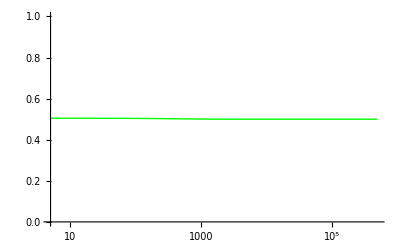

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

{{5,0.499612},{6,0.499742},{6,0.499742},{7,0.499827},{7,0.499827},{8,0.499882},{9,0.499918},{10,0.499942},{11,0.499958},{12,0.499968},{14,0.499979},{15,0.499982},{17,0.499985},{18,0.499986},{20,0.499987},{22,0.499987},{25,0.499988},{27,0.499988},{30,0.499988},{33,0.499988},{37,0.499988},{41,0.499988},{45,0.499988},{50,0.499988},{55,0.499988},{61,0.499989},{67,0.499989},{74,0.499989},{82,0.499989},{91,0.499989},{100,0.499989},{111,0.49999},{123,0.49999},{136,0.49999},{150,0.499991},{166,0.499991},{183,0.499991},{202,0.499992},{224,0.499992},{247,0.499992},{273,0.499993},{302,0.499993},{333,0.499994},{368,0.499994},{407,0.499995},{450,0.499995},{497,0.499996},{550,0.499996},{608,0.499997},{671,0.499997},{742,0.499997},{820,0.499998},{906,0.499998},{1002,0.499999},{1107,0.499999},{1223,0.499999},{1352,0.499999},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

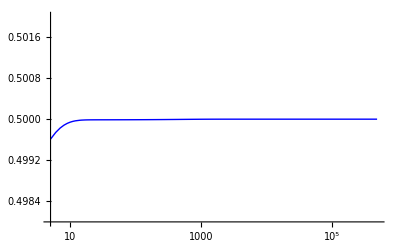

```mathematica
SRtab4=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset4=ListLogLinearPlot[SRtab4,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Blue}]
```

#### Increasing recombination R (r=0.2) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.475;
tryr=0.2;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.381667,0.326267,0.249116,0.501971}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.02686,0.922851}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.0791,0.950121}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.950121,1.0791},{0.946876,1.07171},{0.943235,1.06471},{0.939164,1.05815},{0.934636,1.05204},{0.929632,1.0464},{0.924145,1.04125},{0.918178,1.03658},{0.911747,1.03237},{0.904877,1.0286},{0.897601,1.02524},{0.889954,1.02225},{0.881973,1.01959},{0.873696,1.01723},{0.865158,1.01513},{0.856392,1.01326},{0.847425,1.01159},{0.838283,1.01009},{0.82899,1.00875},{0.819563,1.00754},{0.81002,1.00644},{0.800374,1.00545},{0.79064,1.00455},{0.780826,1.00372},{0.770943,1.00297},{0.760997,1.00227},{0.750997,1.00164},{0.740948,1.00105},{0.730855,1.0005},{0.720722,0.999998},{0.710554,0.999528},{0.700354,0.99909},{0.690125,0.998681},{0.67987,0.998298},{0.669591,0.997939},{0.65929,0.997602},{0.648969,0.997285},{0.638629,0.996986},{0.628273,0.996704},{0.617902,0.996437},{0.607516,0.996185},{0.597117,0.995946},{0.586706,0.995718},{0.576284,0.995503},{0.565851,0.995297},{0.555409,0.995102},{0.544957,0.994915},{0.534497,0.994737},{0.524029,0.994567},{0.513554,0.994404},{0.503072,0.994248}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

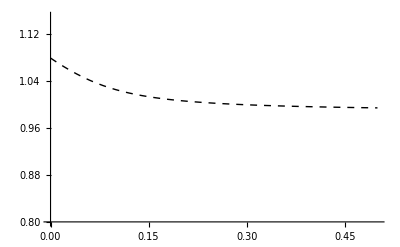

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

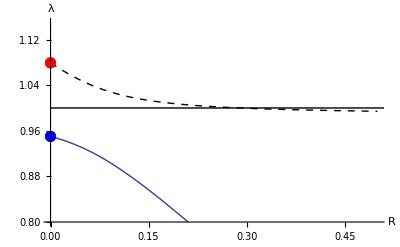

```mathematica
Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.25;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.506603},{6,0.506654},{6,0.506654},{7,0.50669},{7,0.50669},{8,0.506716},{9,0.506737},{10,0.506753},{11,0.506767},{12,0.50678},{14,0.506804},{15,0.506815},{17,0.506837},{18,0.506848},{20,0.506871},{22,0.506893},{25,0.506927},{27,0.506949},{30,0.506984},{33,0.507018},{37,0.507065},{41,0.507111},{45,0.507159},{50,0.507219},{55,0.507279},{61,0.507353},{67,0.507427},{74,0.507516},{82,0.507618},{91,0.507736},{100,0.507857},{111,0.508007},{123,0.508176},{136,0.508364},{150,0.508573},{166,0.50882},{183,0.509094},{202,0.509412},{224,0.509798},{247,0.510224},{273,0.510734},{302,0.51134},{333,0.512035},{368,0.512882},{407,0.513912},{450,0.515161},{497,0.516679},{550,0.518602},{608,0.521},{671,0.523999},{742,0.52795},{820,0.533103},{906,0.539947},{1002,0.549279},{1107,0.561853},{1223,0.578938},{1352,0.601913},{1494,0.631249},{1651,0.66639},{1825,0.705129},{2017,0.744128},{2229,0.78068},{2464,0.813314},{2723,0.841329},{3009,0.864979},{3326,0.88483},{3675,0.901332},{4062,0.915163},{4489,0.926731},{4961,0.936467},{5483,0.944704},{6060,0.951703},{6697,0.957673},{7401,0.962796},{8180,0.967216},{9040,0.971036},{9991,0.974356},{11042,0.97725},{12203,0.97978},{13486,0.981999},{14905,0.983953},{16472,0.985673},{18205,0.987195},{20119,0.988542},{22235,0.989737},{24574,0.9908},{27158,0.991745},{30015,0.992588},{33171,0.99334},{36660,0.994012},{40515,0.994613},{44776,0.995152},{49486,0.995635},{54690,0.996067},{60442,0.996456},{66799,0.996805},{73824,0.997119},{81588,0.997401},{90169,0.997655},{99652,0.997884},{110132,0.998089},{121715,0.998275},{134516,0.998442},{148663,0.998593},{164298,0.998729},{181578,0.998852},{200674,0.998962},{221779,0.999062},{245104,0.999152},{270882,0.999234},{299371,0.999307},{330856,0.999374},{365652,0.999434},{404108,0.999488},{446609,0.999537},{493579,0.999581}}

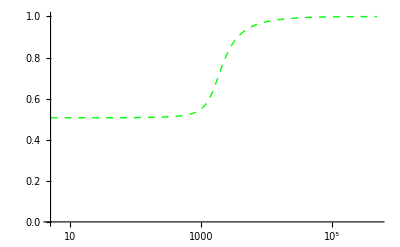

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dashed,Green}]
```

{{5,0.501471},{6,0.501597},{6,0.501597},{7,0.501679},{7,0.501679},{8,0.501732},{9,0.501766},{10,0.501788},{11,0.501802},{12,0.501811},{14,0.50182},{15,0.501822},{17,0.501824},{18,0.501825},{20,0.501825},{22,0.501824},{25,0.501823},{27,0.501823},{30,0.501822},{33,0.501821},{37,0.501819},{41,0.501818},{45,0.501816},{50,0.501815},{55,0.501813},{61,0.501811},{67,0.501809},{74,0.501806},{82,0.501803},{91,0.5018},{100,0.501796},{111,0.501792},{123,0.501787},{136,0.501782},{150,0.501776},{166,0.501769},{183,0.501761},{202,0.501752},{224,0.501742},{247,0.50173},{273,0.501716},{302,0.501699},{333,0.50168},{368,0.501658},{407,0.50163},{450,0.501598},{497,0.501559},{550,0.501511},{608,0.501452},{671,0.501382},{742,0.501293},{820,0.501184},{906,0.50105},{1002,0.500885},{1107,0.500691},{1223,0.500476},{1352,0.500255},{1494,0.500062},{1651,0.499929},{1825,0.499863},{2017,0.49985},{2229,0.499866},{2464,0.49989},{2723,0.499915},{3009,0.499935},{3326,0.499951},{3675,0.499964},{4062,0.499973},{4489,0.499979},{4961,0.499984},{5483,0.499988},{6060,0.499991},{6697,0.499993},{7401,0.499995},{8180,0.499996},{9040,0.499997},{9991,0.499997},{11042,0.499998},{12203,0.499998},{13486,0.499999},{14905,0.499999},{16472,0.499999},{18205,0.499999},{20119,0.499999},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

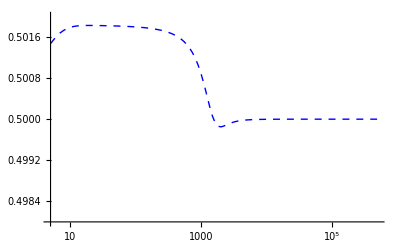

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Dashed,Blue}]
```

#### Increasing recombination R (r=0.2) with meiotic drive in homogametic sex (causes a drive) EQUIL B

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.525;
tryαm=0.5;
tryr=0.2;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.723464,0.668989,0.573869,0.5}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,0.857143}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.03912,0.902693}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.902693,1.03912},{0.896684,1.03535},{0.890355,1.03191},{0.883725,1.02876},{0.876814,1.0259},{0.869645,1.02329},{0.86224,1.02092},{0.854621,1.01876},{0.846808,1.0168},{0.838821,1.01501},{0.830678,1.01337},{0.822394,1.01188},{0.813984,1.01052},{0.805461,1.00926},{0.796837,1.00811},{0.788122,1.00705},{0.779326,1.00607},{0.770456,1.00516},{0.76152,1.00432},{0.752524,1.00354},{0.743474,1.00282},{0.734375,1.00214},{0.725231,1.00151},{0.716047,1.00091},{0.706825,1.00036},{0.69757,0.999839},{0.688284,0.999349},{0.678969,0.998887},{0.669628,0.998452},{0.660263,0.99804},{0.650876,0.997651},{0.641468,0.997283},{0.632042,0.996933},{0.622597,0.996601},{0.613137,0.996286},{0.603661,0.995986},{0.594171,0.995699},{0.584667,0.995426},{0.575152,0.995166},{0.565624,0.994917},{0.556086,0.994679},{0.546538,0.994451},{0.536981,0.994232},{0.527414,0.994022},{0.517839,0.993821},{0.508256,0.993628},{0.498665,0.993442},{0.489068,0.993264},{0.479464,0.993092},{0.469853,0.992926},{0.460237,0.992766}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

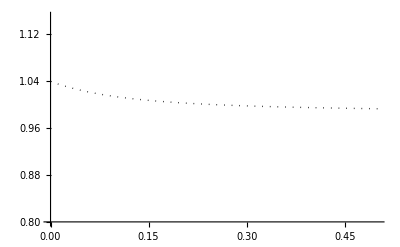

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

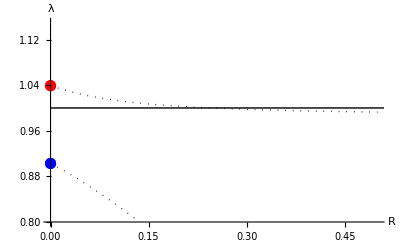

```mathematica
Show[
plot6,
ListPlot[eigen1,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion occurs over a broader parameter space if it evens the sex ratio (dashed) but also when it causes the sex ratio to depart from 1/2 (thin).

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.25;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504623},{6,0.50467},{6,0.50467},{7,0.5047},{7,0.5047},{8,0.50472},{9,0.504732},{10,0.50474},{11,0.504746},{12,0.504749},{14,0.504752},{15,0.504753},{17,0.504754},{18,0.504754},{20,0.504753},{22,0.504753},{25,0.504752},{27,0.504751},{30,0.50475},{33,0.50475},{37,0.504748},{41,0.504747},{45,0.504746},{50,0.504744},{55,0.504743},{61,0.504741},{67,0.504739},{74,0.504737},{82,0.504734},{91,0.504731},{100,0.504729},{111,0.504725},{123,0.504721},{136,0.504717},{150,0.504713},{166,0.504708},{183,0.504702},{202,0.504696},{224,0.504689},{247,0.504682},{273,0.504674},{302,0.504665},{333,0.504655},{368,0.504644},{407,0.504631},{450,0.504617},{497,0.504602},{550,0.504585},{608,0.504567},{671,0.504547},{742,0.504524},{820,0.504499},{906,0.504471},{1002,0.50444},{1107,0.504407},{1223,0.504369},{1352,0.504328},{1494,0.504282},{1651,0.504231},{1825,0.504174},{2017,0.504112},{2229,0.504043},{2464,0.503967},{2723,0.503883},{3009,0.503791},{3326,0.503688},{3675,0.503576},{4062,0.503453},{4489,0.503318},{4961,0.503171},{5483,0.503012},{6060,0.502839},{6697,0.502654},{7401,0.502456},{8180,0.502248},{9040,0.502031},{9991,0.501808},{11042,0.501582},{12203,0.501358},{13486,0.50114},{14905,0.500935},{16472,0.500745},{18205,0.500577},{20119,0.500432},{22235,0.500312},{24574,0.500216},{27158,0.500144},{30015,0.500091},{33171,0.500055},{36660,0.500031},{40515,0.500017},{44776,0.500009},{49486,0.500004},{54690,0.500002},{60442,0.500001},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

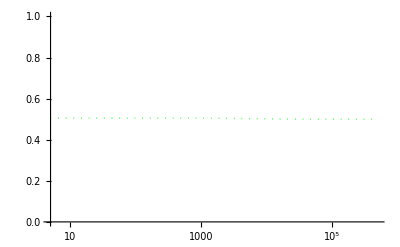

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.499542},{6,0.499672},{6,0.499672},{7,0.499757},{7,0.499757},{8,0.499813},{9,0.49985},{10,0.499874},{11,0.49989},{12,0.499901},{14,0.499912},{15,0.499916},{17,0.499919},{18,0.49992},{20,0.499921},{22,0.499921},{25,0.499922},{27,0.499922},{30,0.499922},{33,0.499922},{37,0.499922},{41,0.499922},{45,0.499922},{50,0.499922},{55,0.499922},{61,0.499922},{67,0.499922},{74,0.499922},{82,0.499922},{91,0.499922},{100,0.499922},{111,0.499922},{123,0.499922},{136,0.499922},{150,0.499922},{166,0.499923},{183,0.499923},{202,0.499923},{224,0.499923},{247,0.499923},{273,0.499923},{302,0.499923},{333,0.499923},{368,0.499924},{407,0.499924},{450,0.499924},{497,0.499924},{550,0.499924},{608,0.499925},{671,0.499925},{742,0.499925},{820,0.499926},{906,0.499926},{1002,0.499927},{1107,0.499927},{1223,0.499928},{1352,0.499929},{1494,0.499929},{1651,0.49993},{1825,0.499931},{2017,0.499932},{2229,0.499933},{2464,0.499934},{2723,0.499936},{3009,0.499937},{3326,0.499939},{3675,0.499941},{4062,0.499943},{4489,0.499945},{4961,0.499947},{5483,0.49995},{6060,0.499953},{6697,0.499956},{7401,0.499959},{8180,0.499962},{9040,0.499966},{9991,0.49997},{11042,0.499973},{12203,0.499977},{13486,0.499981},{14905,0.499984},{16472,0.499987},{18205,0.49999},{20119,0.499993},{22235,0.499995},{24574,0.499996},{27158,0.499998},{30015,0.499998},{33171,0.499999},{36660,0.499999},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

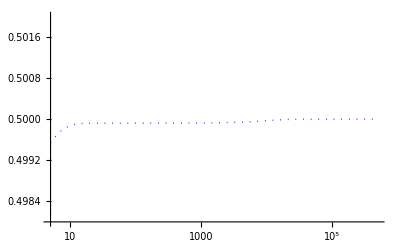

```mathematica
SRtab6=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset6=ListLogLinearPlot[SRtab6,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Dotted,Blue}]
```

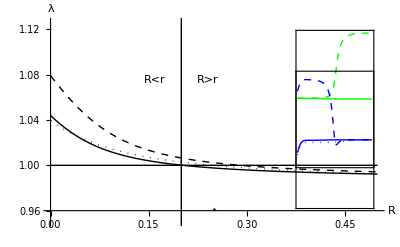

```mathematica
plotB=Show[
plot4,plot5,plot6,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
Graphics[Inset[Show[SRinset4,SRinset5,SRinset6,FrameTicks->False,Frame->True],{0.43,1.02},Center,{0.14,0.14}]],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
ListPlot[{{0.2,0},{0.2,2}},Joined->True,PlotStyle->{Thin,Black}],
Graphics[Text[Style["⋆",Large],{0.25,0.96}]],
Graphics[Text[Style["R<r",Medium],{0.16,1.075}]],
Graphics[Text[Style["R>r",Medium],{0.24,1.075}]],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.08}},AxesOrigin->{0,0.96}
]
```

#### Increasing recombination R (r=0.05) [No haploid selection] EXAMPLE STARTING NEAR EQUIL A [In the absence of haploid selection, R<r is predictive, but haploid selection allows invasion with R>r]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=0.925;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.588794,0.542426,0.226644,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.853933,0.837403,0,0.5}

{0.989094,0.884337}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.03187,0.918942}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.918942,1.03187},{0.91483,1.02586},{0.910266,1.0203},{0.90524,1.0152},{0.899749,1.01057},{0.893804,1.00639},{0.887426,1.00264},{0.880645,0.999301},{0.873493,0.996328},{0.866007,0.99369},{0.858224,0.991349},{0.850178,0.989271},{0.841902,0.987423},{0.833425,0.985775},{0.824773,0.984303},{0.815968,0.982984},{0.807031,0.981798},{0.797977,0.980728},{0.788821,0.979759},{0.779577,0.97888},{0.770254,0.978078},{0.760862,0.977346},{0.751409,0.976675},{0.741902,0.976058},{0.732347,0.975489},{0.722748,0.974963},{0.713111,0.974476},{0.70344,0.974024},{0.693737,0.973603},{0.684005,0.97321},{0.674248,0.972843},{0.664468,0.972499},{0.654667,0.972176},{0.644846,0.971873},{0.635008,0.971587},{0.625153,0.971318},{0.615284,0.971063},{0.6054,0.970823},{0.595504,0.970595},{0.585597,0.970378},{0.575678,0.970173},{0.56575,0.969977},{0.555811,0.969791},{0.545865,0.969614},{0.53591,0.969445},{0.525947,0.969283},{0.515978,0.969129},{0.506001,0.968981},{0.496019,0.968839},{0.486031,0.968704},{0.476037,0.968574}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

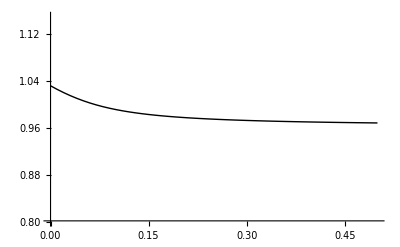

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

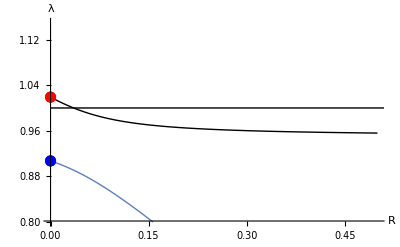

```mathematica
Show[
plot4,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.025;
tryR=0.05;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504188},{6,0.5041},{6,0.5041},{7,0.50402},{7,0.50402},{8,0.503946},{9,0.503879},{10,0.503818},{11,0.503761},{12,0.503709},{14,0.503616},{15,0.503574},{17,0.503498},{18,0.503464},{20,0.5034},{22,0.503343},{25,0.503265},{27,0.503217},{30,0.503151},{33,0.50309},{37,0.503012},{41,0.502939},{45,0.50287},{50,0.502786},{55,0.502705},{61,0.502611},{67,0.502521},{74,0.502419},{82,0.502307},{91,0.502188},{100,0.502074},{111,0.501943},{123,0.501809},{136,0.501673},{150,0.501538},{166,0.501396},{183,0.501259},{202,0.501122},{224,0.500981},{247,0.500851},{273,0.500725},{302,0.500606},{333,0.5005},{368,0.500402},{407,0.500315},{450,0.50024},{497,0.500179},{550,0.500128},{608,0.500089},{671,0.50006},{742,0.500038},{820,0.500023},{906,0.500014},{1002,0.500007},{1107,0.500004},{1223,0.500002},{1352,0.500001},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

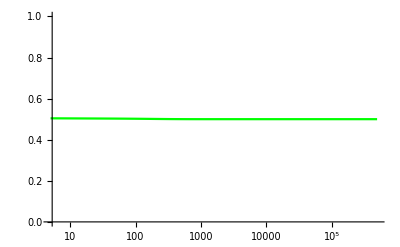

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

{{5,0.499887},{6,0.499894},{6,0.499894},{7,0.499899},{7,0.499899},{8,0.499904},{9,0.499909},{10,0.499914},{11,0.499918},{12,0.499922},{14,0.49993},{15,0.499933},{17,0.49994},{18,0.499943},{20,0.499949},{22,0.499955},{25,0.499963},{27,0.499967},{30,0.499973},{33,0.499979},{37,0.499985},{41,0.499989},{45,0.499993},{50,0.499997},{55,0.5},{61,0.500003},{67,0.500005},{74,0.500006},{82,0.500007},{91,0.500007},{100,0.500007},{111,0.500007},{123,0.500007},{136,0.500006},{150,0.500006},{166,0.500006},{183,0.500005},{202,0.500004},{224,0.500004},{247,0.500003},{273,0.500003},{302,0.500002},{333,0.500002},{368,0.500002},{407,0.500001},{450,0.500001},{497,0.500001},{550,0.500001},{608,0.5},{671,0.5},{742,0.5},{820,0.5},{906,0.5},{1002,0.5},{1107,0.5},{1223,0.5},{1352,0.5},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

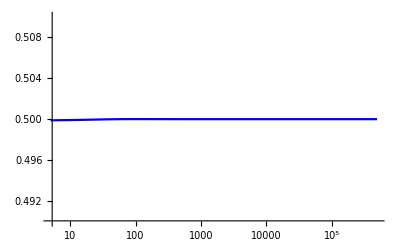

```mathematica
SRtab4=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset4=ListLogLinearPlot[SRtab4,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Blue}]
```

#### Increasing recombination R (r=0.05) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=0.925;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.475;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.405998,0.350557,0.100005,0.506441}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.04989,0.92428}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.07914,0.942933}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.942933,1.07914},{0.940395,1.07101},{0.937527,1.06321},{0.934289,1.05577},{0.930642,1.04875},{0.926551,1.04217},{0.921985,1.03606},{0.916926,1.03045},{0.911367,1.02533},{0.905313,1.02072},{0.898782,1.01657},{0.891803,1.01288},{0.884411,1.0096},{0.876644,1.0067},{0.868544,1.00412},{0.86015,1.00185},{0.851497,0.999827},{0.842619,0.998033},{0.833545,0.996435},{0.824301,0.995007},{0.81491,0.993726},{0.805389,0.992575},{0.795757,0.991535},{0.786027,0.990593},{0.77621,0.989737},{0.766319,0.988957},{0.75636,0.988243},{0.746343,0.987588},{0.736274,0.986986},{0.726157,0.98643},{0.716,0.985915},{0.705804,0.985439},{0.695576,0.984995},{0.685316,0.984582},{0.67503,0.984197},{0.664718,0.983836},{0.654384,0.983498},{0.64403,0.983181},{0.633656,0.982882},{0.623266,0.9826},{0.612859,0.982335},{0.602438,0.982084},{0.592004,0.981846},{0.581557,0.981621},{0.571098,0.981407},{0.560629,0.981204},{0.55015,0.981011},{0.539662,0.980827},{0.529166,0.980651},{0.518661,0.980484},{0.508149,0.980324}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

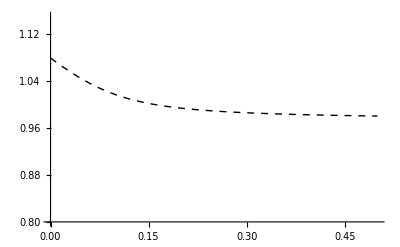

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

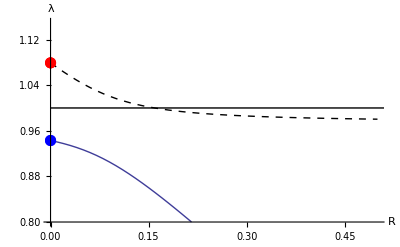

```mathematica
Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.511042},{6,0.511061},{6,0.511061},{7,0.511089},{7,0.511089},{8,0.511126},{9,0.511171},{10,0.511224},{11,0.511284},{12,0.511352},{14,0.511509},{15,0.511597},{17,0.511794},{18,0.511902},{20,0.512136},{22,0.512394},{25,0.512825},{27,0.513141},{30,0.513659},{33,0.514229},{37,0.515075},{41,0.516023},{45,0.517082},{50,0.518573},{55,0.52027},{61,0.52261},{67,0.525323},{74,0.529024},{82,0.534057},{91,0.540891},{100,0.54912},{111,0.561249},{123,0.577157},{136,0.5973},{150,0.621543},{166,0.650782},{183,0.681466},{202,0.713286},{224,0.745656},{247,0.774323},{273,0.801167},{302,0.825464},{333,0.846339},{368,0.865147},{407,0.881724},{450,0.896127},{497,0.908533},{550,0.919543},{608,0.92902},{671,0.937152},{742,0.944401},{820,0.950699},{906,0.956208},{1002,0.961092},{1107,0.965342},{1223,0.969089},{1352,0.972419},{1494,0.975352},{1651,0.977953},{1825,0.980266},{2017,0.982319},{2229,0.984144},{2464,0.985775},{2723,0.987225},{3009,0.988519},{3326,0.98968},{3675,0.990715},{4062,0.991645},{4489,0.992477},{4961,0.993223},{5483,0.993894},{6060,0.994497},{6697,0.995038},{7401,0.995524},{8180,0.995962},{9040,0.996356},{9991,0.996711},{11042,0.997031},{12203,0.997319},{13486,0.997579},{14905,0.997813},{16472,0.998024},{18205,0.998215},{20119,0.998387},{22235,0.998542},{24574,0.998683},{27158,0.998809},{30015,0.998924},{33171,0.999027},{36660,0.99912},{40515,0.999204},{44776,0.999281},{49486,0.999349},{54690,0.999412},{60442,0.999468},{66799,0.999519},{73824,0.999565},{81588,0.999606},{90169,0.999644},{99652,0.999678},{110132,0.999709},{121715,0.999736},{134516,0.999762},{148663,0.999784},{164298,0.999805},{181578,0.999824},{200674,0.99984},{221779,0.999856},{245104,0.999869},{270882,0.999882},{299371,0.999893},{330856,0.999903},{365652,0.999912},{404108,0.999921},{446609,0.999928},{493579,0.999935}}

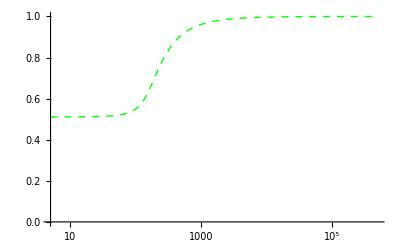

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dashed,Green}]
```

{{5,0.505885},{6,0.5059},{6,0.5059},{7,0.505911},{7,0.505911},{8,0.505919},{9,0.505924},{10,0.505926},{11,0.505927},{12,0.505925},{14,0.505918},{15,0.505913},{17,0.505899},{18,0.505892},{20,0.505874},{22,0.505853},{25,0.505818},{27,0.505793},{30,0.505751},{33,0.505704},{37,0.505634},{41,0.505556},{45,0.505468},{50,0.505344},{55,0.505204},{61,0.505011},{67,0.50479},{74,0.504494},{82,0.504102},{91,0.503592},{100,0.503013},{111,0.502229},{123,0.501328},{136,0.500389},{150,0.49954},{166,0.49888},{183,0.49854},{202,0.498471},{224,0.498593},{247,0.498791},{273,0.499009},{302,0.499209},{333,0.499374},{368,0.499511},{407,0.49962},{450,0.499705},{497,0.49977},{550,0.499822},{608,0.499861},{671,0.499891},{742,0.499915},{820,0.499933},{906,0.499947},{1002,0.499958},{1107,0.499967},{1223,0.499974},{1352,0.499979},{1494,0.499983},{1651,0.499987},{1825,0.499989},{2017,0.499991},{2229,0.499993},{2464,0.499994},{2723,0.499996},{3009,0.499996},{3326,0.499997},{3675,0.499998},{4062,0.499998},{4489,0.499998},{4961,0.499999},{5483,0.499999},{6060,0.499999},{6697,0.499999},{7401,0.499999},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

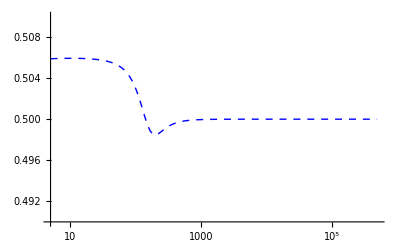

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Dashed,Blue}]
```

#### Increasing recombination R (r=0.05) with meiotic drive in homogametic sex (causes a drive) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=0.925;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.525;
tryαm=0.5;
tryr=0.05;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.806281,0.766533,0.376464,0.5}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,0.857143}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.02527,0.885786}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.885786,1.02527},{0.880319,1.02104},{0.874527,1.01714},{0.868423,1.01355},{0.862023,1.01026},{0.855344,1.00724},{0.848407,1.00448},{0.841232,1.00196},{0.833838,0.999663},{0.826245,0.997561},{0.818472,0.99564},{0.810536,0.993881},{0.802453,0.99227},{0.794237,0.990791},{0.785902,0.989431},{0.777459,0.98818},{0.768919,0.987025},{0.760292,0.985958},{0.751585,0.984969},{0.742808,0.984052},{0.733966,0.9832},{0.725065,0.982406},{0.716111,0.981665},{0.707108,0.980973},{0.698062,0.980325},{0.688975,0.979717},{0.679851,0.979146},{0.670693,0.978609},{0.661504,0.978104},{0.652287,0.977626},{0.643043,0.977175},{0.633775,0.976749},{0.624485,0.976344},{0.615173,0.975961},{0.605843,0.975597},{0.596494,0.975251},{0.587129,0.974921},{0.577748,0.974608},{0.568353,0.974308},{0.558944,0.974022},{0.549522,0.973749},{0.540089,0.973488},{0.530644,0.973238},{0.521189,0.972998},{0.511725,0.972768},{0.50225,0.972548},{0.492768,0.972336},{0.483277,0.972132},{0.473778,0.971936},{0.464272,0.971748},{0.454759,0.971566}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

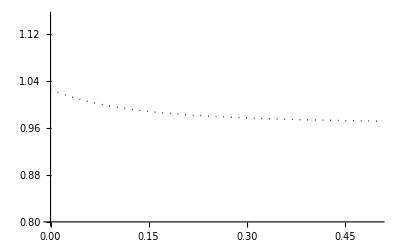

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

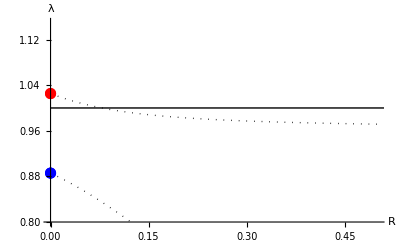

```mathematica
Show[
plot6,
ListPlot[eigen1,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion occurs over a broader parameter space if it evens the sex ratio (dashed) but also when it causes the sex ratio to depart from 1/2 (thin).

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.05;
tryR=0.075;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.50437},{6,0.504352},{6,0.504352},{7,0.504338},{7,0.504338},{8,0.504328},{9,0.50432},{10,0.504314},{11,0.504311},{12,0.504309},{14,0.504308},{15,0.50431},{17,0.504314},{18,0.504317},{20,0.504323},{22,0.504331},{25,0.504343},{27,0.504352},{30,0.504365},{33,0.504378},{37,0.504394},{41,0.504411},{45,0.504428},{50,0.504448},{55,0.504468},{61,0.504492},{67,0.504516},{74,0.504545},{82,0.504577},{91,0.504613},{100,0.50465},{111,0.504695},{123,0.504745},{136,0.504799},{150,0.504859},{166,0.504928},{183,0.505002},{202,0.505086},{224,0.505186},{247,0.505293},{273,0.505416},{302,0.505557},{333,0.505713},{368,0.505895},{407,0.506105},{450,0.506346},{497,0.506623},{550,0.506951},{608,0.507332},{671,0.507773},{742,0.508307},{820,0.508944},{906,0.509714},{1002,0.510668},{1107,0.511844},{1223,0.513332},{1352,0.51527},{1494,0.517835},{1651,0.52136},{1825,0.526438},{2017,0.534174},{2229,0.547},{2464,0.571062},{2723,0.622397},{3009,0.726259},{3326,0.843562},{3675,0.910732},{4062,0.943365},{4489,0.960648},{4961,0.970911},{5483,0.977561},{6060,0.982151},{6697,0.985472},{7401,0.987969},{8180,0.989902},{9040,0.99143},{9991,0.992664},{11042,0.993673},{12203,0.99451},{13486,0.995212},{14905,0.995806},{16472,0.996312},{18205,0.996746},{20119,0.997122},{22235,0.997447},{24574,0.997731},{27158,0.99798},{30015,0.998198},{33171,0.998391},{36660,0.998561},{40515,0.998711},{44776,0.998845},{49486,0.998963},{54690,0.999069},{60442,0.999164},{66799,0.999248},{73824,0.999323},{81588,0.999391},{90169,0.999451},{99652,0.999505},{110132,0.999554},{121715,0.999598},{134516,0.999637},{148663,0.999673},{164298,0.999705},{181578,0.999733},{200674,0.999759},{221779,0.999783},{245104,0.999804},{270882,0.999823},{299371,0.99984},{330856,0.999855},{365652,0.999869},{404108,0.999882},{446609,0.999893},{493579,0.999903}}

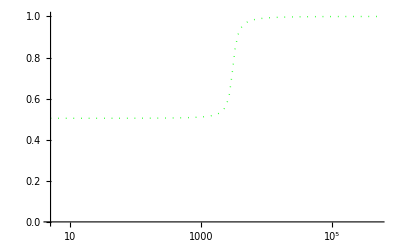

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.499459},{6,0.499482},{6,0.499482},{7,0.499503},{7,0.499503},{8,0.499522},{9,0.499539},{10,0.499554},{11,0.499569},{12,0.499582},{14,0.499604},{15,0.499614},{17,0.499632},{18,0.499639},{20,0.499652},{22,0.499663},{25,0.499676},{27,0.499682},{30,0.49969},{33,0.499695},{37,0.499701},{41,0.499704},{45,0.499706},{50,0.499707},{55,0.499707},{61,0.499706},{67,0.499705},{74,0.499704},{82,0.499702},{91,0.4997},{100,0.499698},{111,0.499695},{123,0.499692},{136,0.499689},{150,0.499685},{166,0.499681},{183,0.499676},{202,0.499671},{224,0.499664},{247,0.499658},{273,0.49965},{302,0.499641},{333,0.499632},{368,0.49962},{407,0.499607},{450,0.499593},{497,0.499576},{550,0.499556},{608,0.499532},{671,0.499506},{742,0.499474},{820,0.499436},{906,0.49939},{1002,0.499335},{1107,0.499267},{1223,0.499183},{1352,0.499077},{1494,0.498939},{1651,0.498758},{1825,0.498511},{2017,0.498164},{2229,0.497655},{2464,0.496878},{2723,0.495722},{3009,0.494458},{3326,0.493856},{3675,0.493735},{4062,0.49372},{4489,0.493719},{4961,0.493719},{5483,0.49372},{6060,0.49372},{6697,0.49372},{7401,0.493721},{8180,0.493721},{9040,0.493721},{9991,0.493721},{11042,0.493721},{12203,0.493721},{13486,0.493721},{14905,0.493721},{16472,0.493721},{18205,0.493721},{20119,0.493721},{22235,0.493721},{24574,0.493721},{27158,0.493721},{30015,0.493721},{33171,0.493721},{36660,0.493721},{40515,0.493721},{44776,0.493721},{49486,0.493721},{54690,0.493721},{60442,0.493721},{66799,0.493721},{73824,0.493721},{81588,0.493721},{90169,0.493721},{99652,0.493721},{110132,0.493721},{121715,0.493721},{134516,0.493721},{148663,0.493721},{164298,0.493721},{181578,0.493721},{200674,0.493721},{221779,0.493721},{245104,0.493721},{270882,0.493721},{299371,0.493721},{330856,0.493721},{365652,0.493721},{404108,0.493721},{446609,0.493721},{493579,0.493721}}

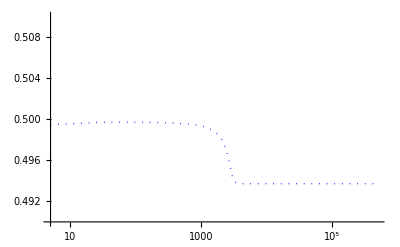

```mathematica
SRtab6=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset6=ListLogLinearPlot[SRtab6,Joined->True,PlotRange->{{startplot,endtime},{0.49,0.51}},PlotStyle->{Dotted,Blue}]
```

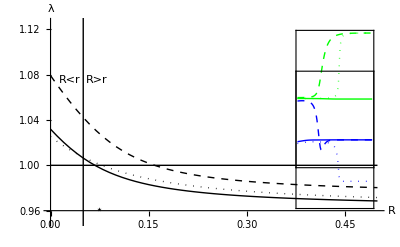

```mathematica
plotC=Show[
plot4,plot5,plot6,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
Graphics[Inset[Show[SRinset4,SRinset5,SRinset6,FrameTicks->False,Frame->True],{0.43,1.02},Center,{0.14,0.14}]],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
ListPlot[{{0.05,0},{0.05,2}},Joined->True,PlotStyle->{Thin,Black}],
Graphics[Text[Style["⋆",Large],{0.075,0.96}]],
Graphics[Text[Style["R<r",Medium],{0.03,1.075}]],
Graphics[Text[Style["R>r",Medium],{0.07,1.075}]],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.08}},AxesOrigin->{0,0.96}
]
```

#### Increasing recombination R (r=0.2) [No haploid selection] EXAMPLE STARTING NEAR EQUIL A [In the absence of haploid selection, R<r is predictive, but haploid selection allows invasion with R>r]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=0.925;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.2;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.500438,0.44783,0.373923,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.853933,0.837403,0.,0.5}

{0.989094,0.884337}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.05229,0.939992}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.939992,1.05229},{0.935523,1.04645},{0.930579,1.04108},{0.925156,1.0362},{0.919259,1.03178},{0.912907,1.02782},{0.906128,1.02429},{0.898956,1.02115},{0.891428,1.01837},{0.883583,1.0159},{0.875458,1.01372},{0.867086,1.01178},{0.8585,1.01005},{0.849727,1.00851},{0.840792,1.00714},{0.831715,1.0059},{0.822516,1.00479},{0.813209,1.00379},{0.803808,1.00288},{0.794325,1.00205},{0.784769,1.00129},{0.775149,1.0006},{0.765472,0.999968},{0.755745,0.999384},{0.745973,0.998845},{0.736161,0.998346},{0.726313,0.997883},{0.716432,0.997452},{0.706523,0.997051},{0.696586,0.996676},{0.686626,0.996326},{0.676643,0.995997},{0.666641,0.995688},{0.65662,0.995398},{0.646583,0.995124},{0.636531,0.994865},{0.626464,0.994621},{0.616384,0.99439},{0.606292,0.99417},{0.59619,0.993962},{0.586076,0.993764},{0.575954,0.993576},{0.565822,0.993396},{0.555682,0.993225},{0.545534,0.993062},{0.535379,0.992906},{0.525217,0.992757},{0.515049,0.992614},{0.504875,0.992477},{0.494695,0.992345},{0.48451,0.992219}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

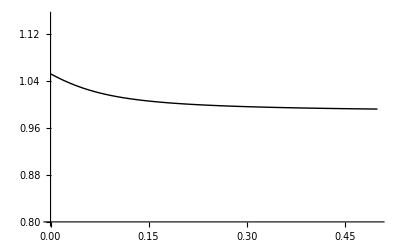

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

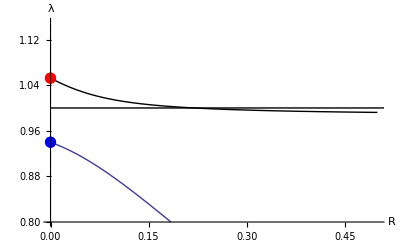

```mathematica
Show[
plot4,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.25;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504602},{6,0.50464},{6,0.50464},{7,0.504662},{7,0.504662},{8,0.504673},{9,0.504678},{10,0.504679},{11,0.504677},{12,0.504673},{14,0.504662},{15,0.504656},{17,0.504643},{18,0.504636},{20,0.504622},{22,0.504609},{25,0.504588},{27,0.504574},{30,0.504553},{33,0.504533},{37,0.504506},{41,0.504479},{45,0.504452},{50,0.504418},{55,0.504385},{61,0.504346},{67,0.504306},{74,0.504261},{82,0.50421},{91,0.504153},{100,0.504096},{111,0.504029},{123,0.503956},{136,0.503878},{150,0.503796},{166,0.503704},{183,0.503609},{202,0.503505},{224,0.503388},{247,0.50327},{273,0.503141},{302,0.503003},{333,0.502861},{368,0.502709},{407,0.502549},{450,0.502382},{497,0.502212},{550,0.502034},{608,0.501854},{671,0.501677},{742,0.501497},{820,0.50132},{906,0.501149},{1002,0.500984},{1107,0.500829},{1223,0.500687},{1352,0.500556},{1494,0.500441},{1651,0.50034},{1825,0.500256},{2017,0.500186},{2229,0.500131},{2464,0.500089},{2723,0.500058},{3009,0.500036},{3326,0.500021},{3675,0.500012},{4062,0.500006},{4489,0.500003},{4961,0.500001},{5483,0.500001},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

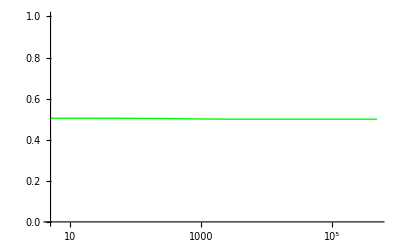

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

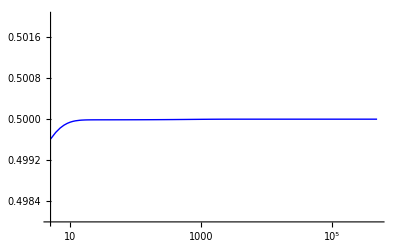

```mathematica
SRinset4=ListLogLinearPlot[Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}],Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Blue}]
```

#### Increasing recombination R (r=0.2) with meiotic drive in heterogametic sex (causes a sex ratio distortion) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=0.925;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.475;
tryr=0.2;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.219358,0.173943,0.122544,0.501332}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.04989,0.92428}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.11591,0.966168}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.966168,1.11591},{0.964418,1.10658},{0.962425,1.0975},{0.960151,1.0887},{0.957548,1.08022},{0.95457,1.07212},{0.951164,1.06445},{0.947281,1.05726},{0.942877,1.05059},{0.937918,1.04447},{0.932386,1.03892},{0.926282,1.03395},{0.919622,1.02953},{0.91244,1.02564},{0.90478,1.02222},{0.896691,1.01923},{0.888225,1.01662},{0.87943,1.01434},{0.870352,1.01234},{0.861031,1.01058},{0.851501,1.00904},{0.841794,1.00767},{0.831934,1.00645},{0.821944,1.00536},{0.81184,1.00439},{0.801639,1.00351},{0.791353,1.00272},{0.780994,1.002},{0.77057,1.00135},{0.76009,1.00075},{0.749559,1.00021},{0.738985,0.999706},{0.728371,0.999242},{0.717723,0.998814},{0.707042,0.998417},{0.696334,0.998048},{0.685601,0.997704},{0.674845,0.997384},{0.664068,0.997084},{0.653272,0.996802},{0.642459,0.996538},{0.63163,0.99629},{0.620787,0.996056},{0.609931,0.995835},{0.599063,0.995626},{0.588183,0.995429},{0.577294,0.995241},{0.566394,0.995063},{0.555486,0.994894},{0.54457,0.994734},{0.533646,0.99458}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

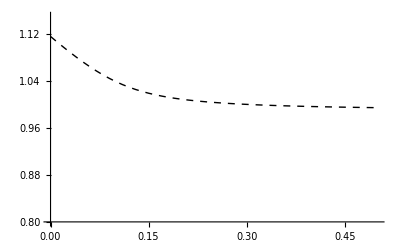

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

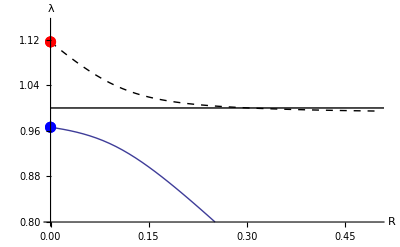

```mathematica
Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.25;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.505989},{6,0.506043},{6,0.506043},{7,0.506082},{7,0.506082},{8,0.506112},{9,0.506136},{10,0.506157},{11,0.506175},{12,0.506193},{14,0.506226},{15,0.506243},{17,0.506276},{18,0.506292},{20,0.506326},{22,0.50636},{25,0.506412},{27,0.506448},{30,0.506501},{33,0.506555},{37,0.506628},{41,0.506702},{45,0.506778},{50,0.506873},{55,0.50697},{61,0.507089},{67,0.507211},{74,0.507356},{82,0.507525},{91,0.507722},{100,0.507926},{111,0.508183},{123,0.508474},{136,0.508804},{150,0.509176},{166,0.509624},{183,0.510128},{202,0.510726},{224,0.511469},{247,0.512307},{273,0.513337},{302,0.514598},{333,0.516087},{368,0.517964},{407,0.520326},{450,0.5233},{497,0.527052},{550,0.531992},{608,0.538371},{671,0.546586},{742,0.557597},{820,0.571921},{906,0.590301},{1002,0.613451},{1107,0.640724},{1223,0.67137},{1352,0.704009},{1494,0.736538},{1651,0.767616},{1825,0.796321},{2017,0.822043},{2229,0.844715},{2464,0.864552},{2723,0.881698},{3009,0.896507},{3326,0.90933},{3675,0.920364},{4062,0.929942},{4489,0.938229},{4961,0.945429},{5483,0.951704},{6060,0.957182},{6697,0.961972},{7401,0.966174},{8180,0.969873},{9040,0.97313},{9991,0.976007},{11042,0.978552},{12203,0.980806},{13486,0.982808},{14905,0.984589},{16472,0.986173},{18205,0.987587},{20119,0.988847},{22235,0.989975},{24574,0.990983},{27158,0.991886},{30015,0.992695},{33171,0.99342},{36660,0.994071},{40515,0.994656},{44776,0.995182},{49486,0.995654},{54690,0.996079},{60442,0.996462},{66799,0.996807},{73824,0.997117},{81588,0.997397},{90169,0.997649},{99652,0.997876},{110132,0.998082},{121715,0.998267},{134516,0.998434},{148663,0.998584},{164298,0.998721},{181578,0.998844},{200674,0.998955},{221779,0.999055},{245104,0.999145},{270882,0.999227},{299371,0.999301},{330856,0.999368},{365652,0.999429},{404108,0.999483},{446609,0.999533},{493579,0.999577}}

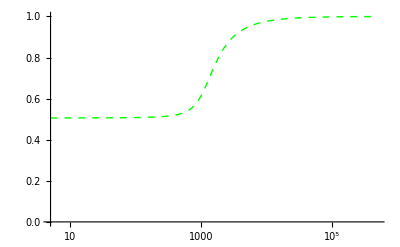

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dashed,Green}]
```

{{5,0.500868},{6,0.500994},{6,0.500994},{7,0.501076},{7,0.501076},{8,0.501129},{9,0.501163},{10,0.501185},{11,0.501199},{12,0.501208},{14,0.501217},{15,0.501219},{17,0.501221},{18,0.501221},{20,0.501221},{22,0.50122},{25,0.501219},{27,0.501218},{30,0.501217},{33,0.501215},{37,0.501214},{41,0.501212},{45,0.50121},{50,0.501208},{55,0.501206},{61,0.501203},{67,0.5012},{74,0.501197},{82,0.501193},{91,0.501189},{100,0.501184},{111,0.501178},{123,0.501172},{136,0.501165},{150,0.501157},{166,0.501147},{183,0.501137},{202,0.501124},{224,0.501109},{247,0.501091},{273,0.50107},{302,0.501045},{333,0.501016},{368,0.500979},{407,0.500935},{450,0.500881},{497,0.500816},{550,0.500734},{608,0.500636},{671,0.500522},{742,0.500387},{820,0.500239},{906,0.500089},{1002,0.499954},{1107,0.499855},{1223,0.499798},{1352,0.499782},{1494,0.499795},{1651,0.499822},{1825,0.499853},{2017,0.499882},{2229,0.499907},{2464,0.499928},{2723,0.499944},{3009,0.499957},{3326,0.499967},{3675,0.499974},{4062,0.49998},{4489,0.499984},{4961,0.499988},{5483,0.49999},{6060,0.499992},{6697,0.499994},{7401,0.499995},{8180,0.499996},{9040,0.499997},{9991,0.499998},{11042,0.499998},{12203,0.499998},{13486,0.499999},{14905,0.499999},{16472,0.499999},{18205,0.499999},{20119,0.499999},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

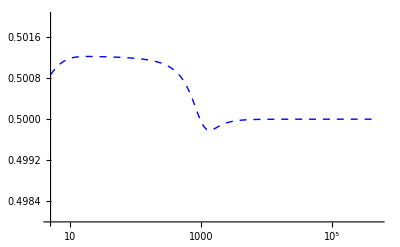

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Dashed,Blue}]
```

#### Increasing recombination R (r=0.2) with meiotic drive in homogametic sex (causes a drive) EQUIL A

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=0.925;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.525;
tryαm=0.5;
tryr=0.2;
tryR=0;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.910049,0.891118,0.857558,0.5}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,0.857143}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.01051,0.902178}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.902178,1.01051},{0.894096,1.00933},{0.885858,1.0083},{0.877489,1.00741},{0.869012,1.00662},{0.860443,1.00593},{0.851796,1.00531},{0.843084,1.00476},{0.834314,1.00426},{0.825497,1.00382},{0.816637,1.00341},{0.80774,1.00305},{0.798812,1.00271},{0.789855,1.00241},{0.780873,1.00212},{0.77187,1.00186},{0.762846,1.00162},{0.753806,1.0014},{0.744749,1.00119},{0.735679,1.001},{0.726595,1.00082},{0.7175,1.00065},{0.708395,1.00049},{0.69928,1.00034},{0.690156,1.0002},{0.681024,1.00007},{0.671885,0.999948},{0.662739,0.99983},{0.653587,0.999719},{0.644429,0.999613},{0.635266,0.999512},{0.626098,0.999417},{0.616925,0.999326},{0.607748,0.999239},{0.598568,0.999156},{0.589383,0.999077},{0.580195,0.999002},{0.571004,0.998929},{0.561809,0.99886},{0.552612,0.998794},{0.543412,0.99873},{0.53421,0.998669},{0.525005,0.99861},{0.515798,0.998553},{0.506589,0.998499},{0.497377,0.998446},{0.488164,0.998396},{0.478949,0.998347},{0.469733,0.9983},{0.460515,0.998255},{0.451295,0.998211}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

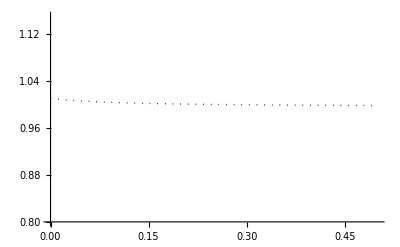

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}]
]
```

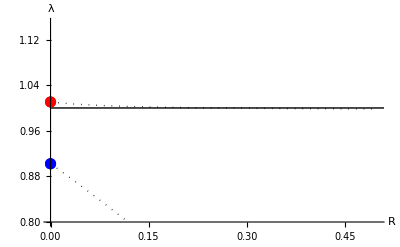

```mathematica
Show[
plot6,
ListPlot[eigen1,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion occurs over a broader parameter space if it evens the sex ratio (dashed) but also when it causes the sex ratio to depart from 1/2 (thin).

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
tryr=0.2;
tryR=0.25;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504687},{6,0.504738},{6,0.504738},{7,0.504771},{7,0.504771},{8,0.504793},{9,0.504808},{10,0.504817},{11,0.504824},{12,0.504828},{14,0.504833},{15,0.504835},{17,0.504837},{18,0.504838},{20,0.504839},{22,0.50484},{25,0.504841},{27,0.504842},{30,0.504843},{33,0.504845},{37,0.504847},{41,0.504848},{45,0.50485},{50,0.504852},{55,0.504855},{61,0.504857},{67,0.50486},{74,0.504863},{82,0.504867},{91,0.504871},{100,0.504875},{111,0.50488},{123,0.504885},{136,0.504891},{150,0.504897},{166,0.504904},{183,0.504912},{202,0.50492},{224,0.50493},{247,0.50494},{273,0.504951},{302,0.504964},{333,0.504978},{368,0.504994},{407,0.505011},{450,0.50503},{497,0.505051},{550,0.505075},{608,0.505101},{671,0.50513},{742,0.505162},{820,0.505198},{906,0.505237},{1002,0.505282},{1107,0.505331},{1223,0.505386},{1352,0.505449},{1494,0.505518},{1651,0.505596},{1825,0.505683},{2017,0.505782},{2229,0.505893},{2464,0.506019},{2723,0.506162},{3009,0.506324},{3326,0.50651},{3675,0.506721},{4062,0.506966},{4489,0.507248},{4961,0.507575},{5483,0.507957},{6060,0.508407},{6697,0.508939},{7401,0.509575},{8180,0.510342},{9040,0.511275},{9991,0.512428},{11042,0.513869},{12203,0.515699},{13486,0.518063},{14905,0.521173},{16472,0.525328},{18205,0.53096},{20119,0.5386},{22235,0.548788},{24574,0.561726},{27158,0.576854},{30015,0.592855},{33171,0.608214},{36660,0.62192},{40515,0.63356},{44776,0.643149},{49486,0.650888},{54690,0.657032},{60442,0.661836},{66799,0.665524},{73824,0.668298},{81588,0.670331},{90169,0.671775},{99652,0.672766},{110132,0.673416},{121715,0.673823},{134516,0.674063},{148663,0.674197},{164298,0.674266},{181578,0.674299},{200674,0.674314},{221779,0.67432},{245104,0.674322},{270882,0.674322},{299371,0.674323},{330856,0.674323},{365652,0.674323},{404108,0.674323},{446609,0.674323},{493579,0.674323}}

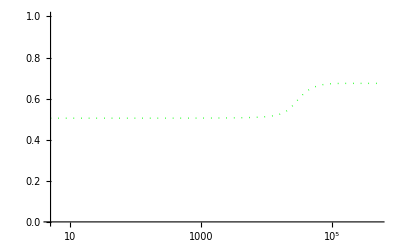

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.49959},{6,0.499723},{6,0.499723},{7,0.49981},{7,0.49981},{8,0.499867},{9,0.499905},{10,0.499929},{11,0.499945},{12,0.499955},{14,0.499967},{15,0.49997},{17,0.499973},{18,0.499974},{20,0.499974},{22,0.499975},{25,0.499975},{27,0.499975},{30,0.499975},{33,0.499975},{37,0.499975},{41,0.499975},{45,0.499975},{50,0.499975},{55,0.499975},{61,0.499975},{67,0.499975},{74,0.499975},{82,0.499975},{91,0.499975},{100,0.499975},{111,0.499975},{123,0.499975},{136,0.499975},{150,0.499975},{166,0.499976},{183,0.499976},{202,0.499976},{224,0.499976},{247,0.499976},{273,0.499976},{302,0.499976},{333,0.499976},{368,0.499976},{407,0.499976},{450,0.499976},{497,0.499975},{550,0.499975},{608,0.499975},{671,0.499975},{742,0.499975},{820,0.499975},{906,0.499975},{1002,0.499975},{1107,0.499975},{1223,0.499974},{1352,0.499974},{1494,0.499974},{1651,0.499973},{1825,0.499973},{2017,0.499973},{2229,0.499972},{2464,0.499972},{2723,0.499971},{3009,0.49997},{3326,0.49997},{3675,0.499969},{4062,0.499968},{4489,0.499967},{4961,0.499965},{5483,0.499964},{6060,0.499962},{6697,0.49996},{7401,0.499958},{8180,0.499955},{9040,0.499952},{9991,0.499949},{11042,0.499944},{12203,0.499939},{13486,0.499934},{14905,0.499927},{16472,0.49992},{18205,0.499913},{20119,0.499907},{22235,0.499905},{24574,0.499909},{27158,0.499919},{30015,0.499933},{33171,0.499948},{36660,0.499961},{40515,0.499971},{44776,0.499979},{49486,0.499985},{54690,0.499989},{60442,0.499992},{66799,0.499995},{73824,0.499996},{81588,0.499998},{90169,0.499999},{99652,0.499999},{110132,0.499999},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

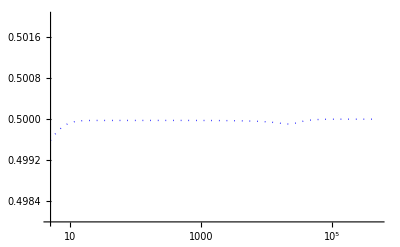

```mathematica
SRtab6=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset6=ListLogLinearPlot[SRtab6,Joined->True,PlotRange->{{startplot,endtime},{0.498,0.502}},PlotStyle->{Dotted,Blue}]
```

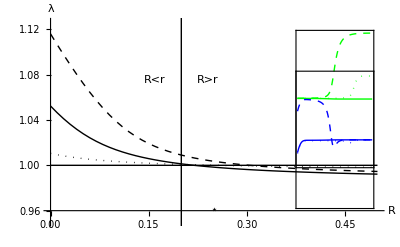

```mathematica
plotD=Show[
plot4,plot5,plot6,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,FrameTicks->False,Frame->True],{0.43,1.056},Center,{0.14,0.14}]],
Graphics[Inset[Show[SRinset4,SRinset5,SRinset6,FrameTicks->False,Frame->True],{0.43,1.02},Center,{0.14,0.14}]],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
ListPlot[{{0.2,0},{0.2,2}},Joined->True,PlotStyle->{Thin,Black}],
Graphics[Text[Style["⋆",Large],{0.25,0.96}]],
Graphics[Text[Style["R<r",Medium],{0.16,1.075}]],
Graphics[Text[Style["R>r",Medium],{0.24,1.075}]],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.956,1.08}},AxesOrigin->{0,0.96}
]
```

### Potential figure - Examples where neo-W can invade despite being unlinked (r~0) [NEW]

#### Increasing recombination R (r=0) Ploidally antagonistic selection [EQUIL B]

The neo-W with allele A can invade in this example of ploidally antagonistic selection even when unlinked:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.9;
tryMAA=1.1;
tryMAa=1;
tryMaa=0.9;
trywAf=1;
trywaf=1;
trywAm=0.76;(* Neo-W can invade if 0.7499999999999999 < wAm < 0.826483809980763 *)
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
tryR=0.5;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{1.,1.,0.,0.5}}

If r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.09809,0.992823}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.992823,1.09809},{0.988016,1.09237},{0.982681,1.08718},{0.976819,1.08251},{0.970447,1.07836},{0.963597,1.07468},{0.956308,1.07144},{0.948624,1.0686},{0.940591,1.06611},{0.932254,1.06392},{0.923652,1.06199},{0.914822,1.0603},{0.905795,1.0588},{0.896601,1.05747},{0.887261,1.05628},{0.877797,1.05522},{0.868224,1.05426},{0.858557,1.0534},{0.848809,1.05263},{0.83899,1.05192},{0.829108,1.05127},{0.819171,1.05069},{0.809186,1.05014},{0.799157,1.04965},{0.78909,1.04919},{0.778989,1.04876},{0.768857,1.04837},{0.758697,1.048},{0.748513,1.04766},{0.738306,1.04734},{0.728078,1.04704},{0.717832,1.04676},{0.707569,1.0465},{0.69729,1.04625},{0.686998,1.04602},{0.676692,1.0458},{0.666374,1.04559},{0.656046,1.04539},{0.645707,1.0452},{0.635358,1.04502},{0.625001,1.04486},{0.614635,1.04469},{0.604263,1.04454},{0.593883,1.04439},{0.583496,1.04426},{0.573103,1.04412},{0.562705,1.04399},{0.552301,1.04387},{0.541892,1.04375},{0.531478,1.04364},{0.52106,1.04353}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

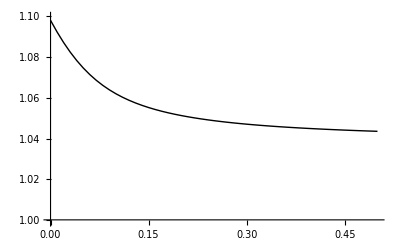

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.999,1.1}}]
]
```

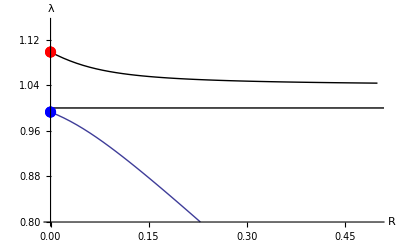

```mathematica
Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
plot5,
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.50629},{6,0.506605},{6,0.506605},{7,0.506909},{7,0.506909},{8,0.507213},{9,0.507521},{10,0.507838},{11,0.508166},{12,0.508506},{14,0.509224},{15,0.509604},{17,0.510409},{18,0.510835},{20,0.511736},{22,0.512706},{25,0.514301},{27,0.515464},{30,0.517371},{33,0.519486},{37,0.522658},{41,0.526268},{45,0.530352},{50,0.536171},{55,0.542829},{61,0.551965},{67,0.562355},{74,0.575997},{82,0.593388},{91,0.614842},{100,0.637777},{111,0.667088},{123,0.699839},{136,0.735376},{150,0.772828},{166,0.813474},{183,0.852821},{202,0.89071},{224,0.925544},{247,0.95195},{273,0.97166},{302,0.984688},{333,0.992214},{368,0.996414},{407,0.998499},{450,0.999427},{497,0.999801},{550,0.999939},{608,0.999984},{671,0.999996},{742,0.999999},{820,1.},{906,1.},{1002,1.},{1107,1.},{1223,1.},{1352,1.},{1494,1.},{1651,1.},{1825,1.},{2017,1.},{2229,1.},{2464,1.},{2723,1.},{3009,1.},{3326,1.},{3675,1.},{4062,1.},{4489,1.},{4961,1.},{5483,1.},{6060,1.},{6697,1.},{7401,1.},{8180,1.},{9040,1.},{9991,1.},{11042,1.},{12203,1.},{13486,1.},{14905,1.},{16472,1.},{18205,1.},{20119,1.},{22235,1.},{24574,1.},{27158,1.},{30015,1.},{33171,1.},{36660,1.},{40515,1.},{44776,1.},{49486,1.},{54690,1.},{60442,1.},{66799,1.},{73824,1.},{81588,1.},{90169,1.},{99652,1.},{110132,1.},{121715,1.},{134516,1.},{148663,1.},{164298,1.},{181578,1.},{200674,1.},{221779,1.},{245104,1.},{270882,1.},{299371,1.},{330856,1.},{365652,1.},{404108,1.},{446609,1.},{493579,1.}}

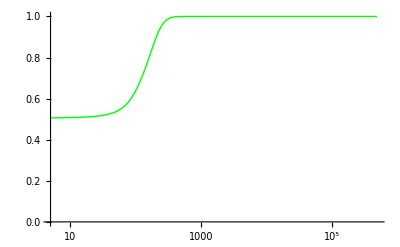

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

{{5,0.564568},{6,0.564559},{6,0.564559},{7,0.564485},{7,0.564485},{8,0.564374},{9,0.56424},{10,0.564092},{11,0.563934},{12,0.563767},{14,0.56341},{15,0.563222},{17,0.562823},{18,0.562614},{20,0.562172},{22,0.5617},{25,0.560931},{27,0.560377},{30,0.559479},{33,0.5585},{37,0.557061},{41,0.555467},{45,0.553718},{50,0.551324},{55,0.548718},{61,0.545359},{67,0.541825},{74,0.537606},{82,0.532841},{91,0.527778},{100,0.523194},{111,0.518343},{123,0.513978},{136,0.510221},{150,0.507123},{166,0.504556},{183,0.502713},{202,0.501441},{224,0.500648},{247,0.500264},{273,0.500091},{302,0.500026},{333,0.500007},{368,0.500001},{407,0.5},{450,0.5},{497,0.5},{550,0.5},{608,0.5},{671,0.5},{742,0.5},{820,0.5},{906,0.5},{1002,0.5},{1107,0.5},{1223,0.5},{1352,0.5},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

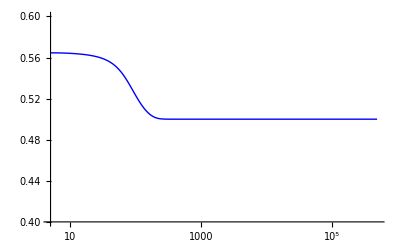

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.6}},PlotStyle->{Blue}]
```

#### Increasing recombination R (r=0) Overdominance in males and no haploid selection [EQUIL B]

The neo-W with allele A can invade in this example of overdominance even when unlinked:

```mathematica
tryFAA=0.99;
tryFAa=1;
tryFaa=1.1;
tryMAA=0.8;
tryMAa=1;
tryMaa=0.8;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
tryR=0.5;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium can be one of two possibilities (we focus below on the second, with the Y fixed on “a”):

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.,0.,1.,0.5},{1.,1.,0.,0.5}}

If R=r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[2]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.00505,1.06061}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.06061,1.00505}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{1.00505,1.06061},{0.999545,1.05601},{0.99317,1.05228},{0.986035,1.04932},{0.978279,1.04697},{0.970035,1.04512},{0.961417,1.04363},{0.952514,1.04244},{0.943393,1.04146},{0.934103,1.04064},{0.924683,1.03996},{0.91516,1.03939},{0.905554,1.03889},{0.895881,1.03846},{0.886153,1.03809},{0.876381,1.03776},{0.866571,1.03747},{0.856729,1.03721},{0.846861,1.03698},{0.836969,1.03677},{0.827058,1.03658},{0.81713,1.03641},{0.807186,1.03625},{0.79723,1.0361},{0.787262,1.03597},{0.777284,1.03585},{0.767296,1.03573},{0.757301,1.03563},{0.747298,1.03553},{0.737288,1.03544},{0.727273,1.03535},{0.717252,1.03527},{0.707226,1.0352},{0.697196,1.03513},{0.687162,1.03506},{0.677124,1.035},{0.667082,1.03494},{0.657038,1.03488},{0.64699,1.03483},{0.63694,1.03478},{0.626887,1.03473},{0.616832,1.03468},{0.606775,1.03464},{0.596716,1.0346},{0.586654,1.03456},{0.576592,1.03452},{0.566527,1.03448},{0.556461,1.03445},{0.546394,1.03441},{0.536325,1.03438},{0.526255,1.03435}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

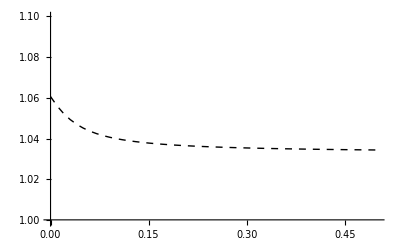

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dashed,Black},PlotRange->{Automatic,{0.999,1.1}}]
]
```

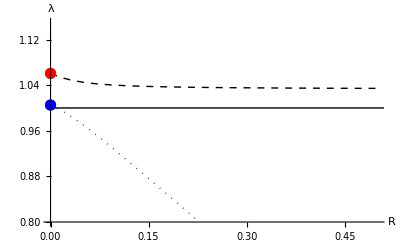

```mathematica
Show[
ListPlot[eigen1,Joined->True,PlotStyle->{Dotted,Thick,Black},PlotRange->{Automatic,{0.8,1.15}}],
plot6,
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion occurs over a broader parameter space if it evens the sex ratio (dashed) but also when it causes the sex ratio to depart from 1/2 (thin).

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.504605},{6,0.504796},{6,0.504796},{7,0.504973},{7,0.504973},{8,0.505146},{9,0.505318},{10,0.505493},{11,0.505672},{12,0.505856},{14,0.506238},{15,0.506438},{17,0.506854},{18,0.507072},{20,0.507526},{22,0.508006},{25,0.508779},{27,0.50933},{30,0.510216},{33,0.511173},{37,0.512571},{41,0.514112},{45,0.515806},{50,0.518146},{55,0.520741},{61,0.524194},{67,0.528004},{74,0.532864},{82,0.538872},{91,0.546024},{100,0.553334},{111,0.562089},{123,0.570951},{136,0.579345},{150,0.58679},{166,0.593354},{183,0.598403},{202,0.602257},{224,0.605081},{247,0.606835},{273,0.607948},{302,0.608592},{333,0.608926},{368,0.609097},{407,0.609174},{450,0.609206},{497,0.609218},{550,0.609222},{608,0.609223},{671,0.609224},{742,0.609224},{820,0.609224},{906,0.609224},{1002,0.609224},{1107,0.609224},{1223,0.609224},{1352,0.609224},{1494,0.609224},{1651,0.609224},{1825,0.609224},{2017,0.609224},{2229,0.609224},{2464,0.609224},{2723,0.609224},{3009,0.609224},{3326,0.609224},{3675,0.609224},{4062,0.609224},{4489,0.609224},{4961,0.609224},{5483,0.609224},{6060,0.609224},{6697,0.609224},{7401,0.609224},{8180,0.609224},{9040,0.609224},{9991,0.609224},{11042,0.609224},{12203,0.609224},{13486,0.609224},{14905,0.609224},{16472,0.609224},{18205,0.609224},{20119,0.609224},{22235,0.609224},{24574,0.609224},{27158,0.609224},{30015,0.609224},{33171,0.609224},{36660,0.609224},{40515,0.609224},{44776,0.609224},{49486,0.609224},{54690,0.609224},{60442,0.609224},{66799,0.609224},{73824,0.609224},{81588,0.609224},{90169,0.609224},{99652,0.609224},{110132,0.609224},{121715,0.609224},{134516,0.609224},{148663,0.609224},{164298,0.609224},{181578,0.609224},{200674,0.609224},{221779,0.609224},{245104,0.609224},{270882,0.609224},{299371,0.609224},{330856,0.609224},{365652,0.609224},{404108,0.609224},{446609,0.609224},{493579,0.609224}}

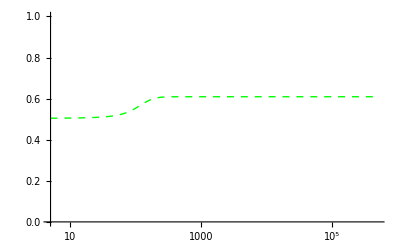

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dashed,Green}]
```

{{5,0.499023},{6,0.499128},{6,0.499128},{7,0.499173},{7,0.499173},{8,0.499186},{9,0.499181},{10,0.499166},{11,0.499145},{12,0.499121},{14,0.499068},{15,0.49904},{17,0.49898},{18,0.498949},{20,0.498884},{22,0.498815},{25,0.498705},{27,0.498627},{30,0.498503},{33,0.49837},{37,0.498179},{41,0.49797},{45,0.497745},{50,0.497441},{55,0.497114},{61,0.496694},{67,0.496251},{74,0.495718},{82,0.495108},{91,0.494454},{100,0.493865},{111,0.493262},{123,0.492761},{136,0.492382},{150,0.492119},{166,0.49194},{183,0.491834},{202,0.491771},{224,0.491734},{247,0.491714},{273,0.491704},{302,0.491698},{333,0.491695},{368,0.491694},{407,0.491693},{450,0.491693},{497,0.491693},{550,0.491693},{608,0.491693},{671,0.491693},{742,0.491693},{820,0.491693},{906,0.491693},{1002,0.491693},{1107,0.491693},{1223,0.491693},{1352,0.491693},{1494,0.491693},{1651,0.491693},{1825,0.491693},{2017,0.491693},{2229,0.491693},{2464,0.491693},{2723,0.491693},{3009,0.491693},{3326,0.491693},{3675,0.491693},{4062,0.491693},{4489,0.491693},{4961,0.491693},{5483,0.491693},{6060,0.491693},{6697,0.491693},{7401,0.491693},{8180,0.491693},{9040,0.491693},{9991,0.491693},{11042,0.491693},{12203,0.491693},{13486,0.491693},{14905,0.491693},{16472,0.491693},{18205,0.491693},{20119,0.491693},{22235,0.491693},{24574,0.491693},{27158,0.491693},{30015,0.491693},{33171,0.491693},{36660,0.491693},{40515,0.491693},{44776,0.491693},{49486,0.491693},{54690,0.491693},{60442,0.491693},{66799,0.491693},{73824,0.491693},{81588,0.491693},{90169,0.491693},{99652,0.491693},{110132,0.491693},{121715,0.491693},{134516,0.491693},{148663,0.491693},{164298,0.491693},{181578,0.491693},{200674,0.491693},{221779,0.491693},{245104,0.491693},{270882,0.491693},{299371,0.491693},{330856,0.491693},{365652,0.491693},{404108,0.491693},{446609,0.491693},{493579,0.491693}}

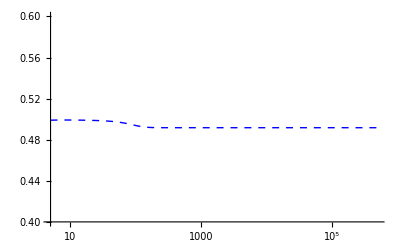

```mathematica
SRtab6=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset6=ListLogLinearPlot[SRtab6,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.6}},PlotStyle->{Dashed,Blue}]
```

#### Increasing recombination R (r=0) Sexually antagonistic selection with haploid selection [EQUIL B]

The neo-W with allele A can invade in this example of sexually antagonistic selection with haploid selection even when unlinked:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.98;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.01;
trywAf=1;
trywaf=1;
trywAm=0.85;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
tryR=0.5;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{1.,1.,0.,0.5}}

If R=r=0 (emanates from equilibrium B):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.,1.,0.,0.5}

{1.03476,0.97861}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.97861,1.03476},{0.973628,1.02985},{0.967791,1.02579},{0.961172,1.02252},{0.953889,1.01991},{0.946073,1.01783},{0.93784,1.01617},{0.929286,1.01483},{0.920486,1.01374},{0.911496,1.01284},{0.902358,1.01208},{0.893102,1.01144},{0.883754,1.0109},{0.874332,1.01043},{0.864848,1.01002},{0.855313,1.00966},{0.845737,1.00934},{0.836126,1.00906},{0.826485,1.00881},{0.816819,1.00858},{0.807131,1.00838},{0.797424,1.00819},{0.787701,1.00802},{0.777963,1.00787},{0.768213,1.00772},{0.758451,1.00759},{0.74868,1.00747},{0.738899,1.00736},{0.729111,1.00725},{0.719316,1.00715},{0.709514,1.00706},{0.699707,1.00698},{0.689894,1.0069},{0.680076,1.00682},{0.670254,1.00675},{0.660428,1.00668},{0.650598,1.00662},{0.640765,1.00656},{0.630928,1.0065},{0.621089,1.00645},{0.611247,1.0064},{0.601403,1.00635},{0.591556,1.0063},{0.581707,1.00626},{0.571856,1.00622},{0.562004,1.00618},{0.552149,1.00614},{0.542293,1.0061},{0.532435,1.00607},{0.522576,1.00603},{0.512716,1.006}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

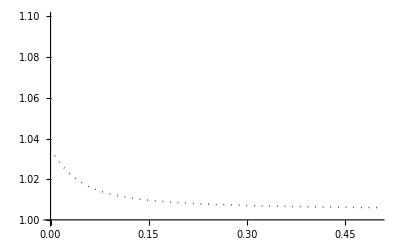

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dotted,Black},PlotRange->{Automatic,{0.999,1.1}}]
]
```

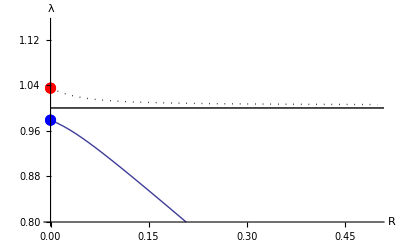

```mathematica
Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
plot4,
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.505415},{6,0.5055},{6,0.5055},{7,0.505562},{7,0.505562},{8,0.505613},{9,0.505657},{10,0.505699},{11,0.505739},{12,0.505779},{14,0.505858},{15,0.505898},{17,0.505978},{18,0.506019},{20,0.506101},{22,0.506184},{25,0.506311},{27,0.506397},{30,0.50653},{33,0.506665},{37,0.50685},{41,0.507041},{45,0.507238},{50,0.507493},{55,0.507759},{61,0.508092},{67,0.508441},{74,0.508872},{82,0.509395},{91,0.510027},{100,0.51071},{111,0.511622},{123,0.512725},{136,0.514068},{150,0.515716},{166,0.51791},{183,0.520692},{202,0.524515},{224,0.530242},{247,0.53845},{273,0.552276},{302,0.57879},{333,0.638349},{368,0.80033},{407,0.972314},{450,0.998603},{497,0.999951},{550,0.999999},{608,1.},{671,1.},{742,1.},{820,1.},{906,1.},{1002,1.},{1107,1.},{1223,1.},{1352,1.},{1494,1.},{1651,1.},{1825,1.},{2017,1.},{2229,1.},{2464,1.},{2723,1.},{3009,1.},{3326,1.},{3675,1.},{4062,1.},{4489,1.},{4961,1.},{5483,1.},{6060,1.},{6697,1.},{7401,1.},{8180,1.},{9040,1.},{9991,1.},{11042,1.},{12203,1.},{13486,1.},{14905,1.},{16472,1.},{18205,1.},{20119,1.},{22235,1.},{24574,1.},{27158,1.},{30015,1.},{33171,1.},{36660,1.},{40515,1.},{44776,1.},{49486,1.},{54690,1.},{60442,1.},{66799,1.},{73824,1.},{81588,1.},{90169,1.},{99652,1.},{110132,1.},{121715,1.},{134516,1.},{148663,1.},{164298,1.},{181578,1.},{200674,1.},{221779,1.},{245104,1.},{270882,1.},{299371,1.},{330856,1.},{365652,1.},{404108,1.},{446609,1.},{493579,1.}}

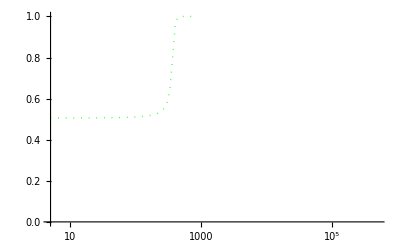

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.539221},{6,0.539346},{6,0.539346},{7,0.539408},{7,0.539408},{8,0.539437},{9,0.539449},{10,0.539452},{11,0.53945},{12,0.539446},{14,0.539433},{15,0.539426},{17,0.539412},{18,0.539404},{20,0.539389},{22,0.539374},{25,0.53935},{27,0.539334},{30,0.53931},{33,0.539285},{37,0.539251},{41,0.539216},{45,0.539179},{50,0.539132},{55,0.539084},{61,0.539023},{67,0.538959},{74,0.538881},{82,0.538786},{91,0.538671},{100,0.538548},{111,0.538384},{123,0.538187},{136,0.537949},{150,0.537659},{166,0.537278},{183,0.536801},{202,0.536155},{224,0.535211},{247,0.5339},{273,0.531788},{302,0.528011},{333,0.520524},{368,0.506113},{407,0.500115},{450,0.5},{497,0.5},{550,0.5},{608,0.5},{671,0.5},{742,0.5},{820,0.5},{906,0.5},{1002,0.5},{1107,0.5},{1223,0.5},{1352,0.5},{1494,0.5},{1651,0.5},{1825,0.5},{2017,0.5},{2229,0.5},{2464,0.5},{2723,0.5},{3009,0.5},{3326,0.5},{3675,0.5},{4062,0.5},{4489,0.5},{4961,0.5},{5483,0.5},{6060,0.5},{6697,0.5},{7401,0.5},{8180,0.5},{9040,0.5},{9991,0.5},{11042,0.5},{12203,0.5},{13486,0.5},{14905,0.5},{16472,0.5},{18205,0.5},{20119,0.5},{22235,0.5},{24574,0.5},{27158,0.5},{30015,0.5},{33171,0.5},{36660,0.5},{40515,0.5},{44776,0.5},{49486,0.5},{54690,0.5},{60442,0.5},{66799,0.5},{73824,0.5},{81588,0.5},{90169,0.5},{99652,0.5},{110132,0.5},{121715,0.5},{134516,0.5},{148663,0.5},{164298,0.5},{181578,0.5},{200674,0.5},{221779,0.5},{245104,0.5},{270882,0.5},{299371,0.5},{330856,0.5},{365652,0.5},{404108,0.5},{446609,0.5},{493579,0.5}}

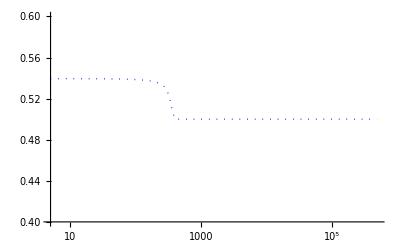

```mathematica
SRtab4=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset4=ListLogLinearPlot[SRtab4,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.6}},PlotStyle->{Dotted,Blue}]
```

#### Summary plot

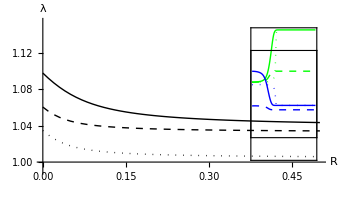

```mathematica
plotA=Show[
plot4,plot5,plot6,
Graphics[Inset[Show[MODinset4,MODinset5,MODinset6,FrameTicks->False,Frame->True],{0.43,1.085},Center,{0.14,0.14}]],
Graphics[Inset[Show[SRinset4,SRinset5,SRinset6,FrameTicks->False,Frame->True],{0.43,1.06},Center,{0.14,0.14}]],
Graphics[Text[Style["⋆",Large],{0.075,0.96}]],
Graphics[Text[Style["⋆",Large],{0.075,0.96}]],
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.999,1.1}},AxesOrigin->{0,1}
]
```

Three examples where even an unlinked neo-W can invade an initially completely linked XY system:

Solid = Ploidally antagonistic selection
Dashed = Overdominance in males (note that this example leads to a polymorphic sex determination system)
Dotted = Sexually antagonistic selection with haploid selection

Insets show simulations of the frequency of Y in males (upper green) and the frequency of males (bottom blue) with R = 0.5.  
Note that an unlinked neo-W can never invade with only pure sexually antagonistic selection.

Common parameters:
tryFAa=1;
tryMAa=1;
trywAf=1;
trywaf=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;

Ploidally antagonistic selection:
tryFAA=1.1;
tryFaa=0.9;
tryMAA=1.1;
tryMaa=0.9;
trywAm=0.76;

Overdominance:
tryFAA=0.99;
tryFaa=1.1;
tryMAA=0.8;
tryMaa=0.8;
trywAm=1;

Sexually antagonistic selection with haploid selection:
tryFAA=1.1;
tryFaa=0.98;
tryMAA=0.8;
tryMaa=1.01;
trywAm=0.85;

#### Increasing recombination R (r=0) Ploidally antagonistic selection [EQUIL B] - can also lead to an polymorphic sex determination system Note that polymorphic sex determination systems are possible even without overdominance, as shown in this section

The neo-W with allele A can invade in this example of ploidally antagonistic selection even when unlinked:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.9;
tryMAA=1.1;
tryMAa=1;
tryMaa=0.9;
trywAf=1;
trywaf=1;
trywAm=0.80; (* Neo-W can invade if 0.7499999999999999 < wAm < 0.826483809980763 *)
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
tryR=0.5;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{1.,1.,0.,0.5}}

If r=0:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,0][[1]];
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{1.06818,0.965909}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.965909,1.06818},{0.961109,1.06275},{0.955796,1.05784},{0.949975,1.05343},{0.943668,1.04951},{0.936905,1.04605},{0.929728,1.043},{0.922178,1.04032},{0.914301,1.03797},{0.906138,1.03591},{0.897727,1.03409},{0.889103,1.03249},{0.880295,1.03107},{0.87133,1.02981},{0.862228,1.02868},{0.853009,1.02767},{0.843688,1.02677},{0.834279,1.02595},{0.824794,1.02521},{0.815241,1.02453},{0.805629,1.02392},{0.795965,1.02335},{0.786254,1.02284},{0.776503,1.02236},{0.766716,1.02192},{0.756896,1.02151},{0.747047,1.02113},{0.737172,1.02078},{0.727273,1.02045},{0.717352,1.02015},{0.707412,1.01986},{0.697454,1.01959},{0.687481,1.01934},{0.677492,1.0191},{0.66749,1.01887},{0.657475,1.01866},{0.647449,1.01846},{0.637412,1.01827},{0.627365,1.01809},{0.61731,1.01792},{0.607246,1.01775},{0.597174,1.0176},{0.587095,1.01745},{0.577009,1.01731},{0.566916,1.01717},{0.556818,1.01705},{0.546714,1.01692},{0.536606,1.0168},{0.526492,1.01669},{0.516373,1.01658},{0.506251,1.01648}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

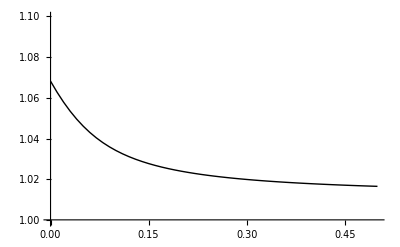

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{0.999,1.1}}]
]
```

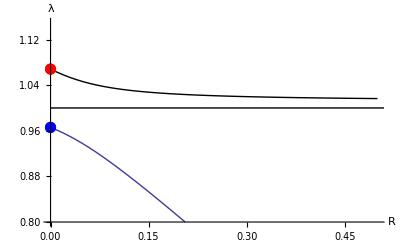

```mathematica
Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
plot5,
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all  initial r EXCEPT very tight linkage, where presumably the association between the a (A) allele and the Y (X) is too strong to allow invasion of the neo-W.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.505249},{6,0.505371},{6,0.505371},{7,0.505474},{7,0.505474},{8,0.505569},{9,0.505658},{10,0.505747},{11,0.505835},{12,0.505923},{14,0.506103},{15,0.506195},{17,0.506381},{18,0.506477},{20,0.506671},{22,0.50687},{25,0.507179},{27,0.507392},{30,0.507722},{33,0.508064},{37,0.508541},{41,0.509042},{45,0.509568},{50,0.510262},{55,0.510997},{61,0.511936},{67,0.512938},{74,0.514188},{82,0.515728},{91,0.517602},{100,0.519626},{111,0.522297},{123,0.525446},{136,0.529103},{150,0.53328},{166,0.538273},{183,0.543717},{202,0.549812},{224,0.556679},{247,0.563441},{273,0.570398},{302,0.577198},{333,0.583353},{368,0.589036},{407,0.594019},{450,0.598188},{497,0.60153},{550,0.604187},{608,0.606155},{671,0.607548},{742,0.608526},{820,0.609159},{906,0.609549},{1002,0.609778},{1107,0.609901},{1223,0.609963},{1352,0.609992},{1494,0.610004},{1651,0.610008},{1825,0.61001},{2017,0.610011},{2229,0.610011},{2464,0.610011},{2723,0.610011},{3009,0.610011},{3326,0.610011},{3675,0.610011},{4062,0.610011},{4489,0.610011},{4961,0.610011},{5483,0.610011},{6060,0.610011},{6697,0.610011},{7401,0.610011},{8180,0.610011},{9040,0.610011},{9991,0.610011},{11042,0.610011},{12203,0.610011},{13486,0.610011},{14905,0.610011},{16472,0.610011},{18205,0.610011},{20119,0.610011},{22235,0.610011},{24574,0.610011},{27158,0.610011},{30015,0.610011},{33171,0.610011},{36660,0.610011},{40515,0.610011},{44776,0.610011},{49486,0.610011},{54690,0.610011},{60442,0.610011},{66799,0.610011},{73824,0.610011},{81588,0.610011},{90169,0.610011},{99652,0.610011},{110132,0.610011},{121715,0.610011},{134516,0.610011},{148663,0.610011},{164298,0.610011},{181578,0.610011},{200674,0.610011},{221779,0.610011},{245104,0.610011},{270882,0.610011},{299371,0.610011},{330856,0.610011},{365652,0.610011},{404108,0.610011},{446609,0.610011},{493579,0.610011}}

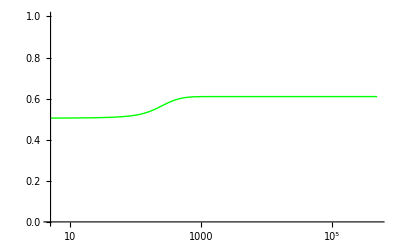

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

{{5,0.552812},{6,0.552888},{6,0.552888},{7,0.552908},{7,0.552908},{8,0.5529},{9,0.552877},{10,0.552846},{11,0.55281},{12,0.552772},{14,0.552692},{15,0.552651},{17,0.552566},{18,0.552523},{20,0.552435},{22,0.552345},{25,0.552205},{27,0.552109},{30,0.551961},{33,0.551808},{37,0.551595},{41,0.551373},{45,0.55114},{50,0.550835},{55,0.550514},{61,0.550108},{67,0.549678},{74,0.549147},{82,0.548502},{91,0.54773},{100,0.546911},{111,0.545855},{123,0.544643},{136,0.54328},{150,0.541781},{166,0.540065},{183,0.538284},{202,0.536395},{224,0.534392},{247,0.53254},{273,0.530751},{302,0.529107},{333,0.527702},{368,0.526471},{407,0.525441},{450,0.524611},{497,0.523968},{550,0.523468},{608,0.523106},{671,0.522852},{742,0.522676},{820,0.522563},{906,0.522494},{1002,0.522453},{1107,0.522431},{1223,0.52242},{1352,0.522415},{1494,0.522413},{1651,0.522412},{1825,0.522412},{2017,0.522412},{2229,0.522412},{2464,0.522412},{2723,0.522412},{3009,0.522412},{3326,0.522412},{3675,0.522412},{4062,0.522412},{4489,0.522412},{4961,0.522412},{5483,0.522412},{6060,0.522412},{6697,0.522412},{7401,0.522412},{8180,0.522412},{9040,0.522412},{9991,0.522412},{11042,0.522412},{12203,0.522412},{13486,0.522412},{14905,0.522412},{16472,0.522412},{18205,0.522412},{20119,0.522412},{22235,0.522412},{24574,0.522412},{27158,0.522412},{30015,0.522412},{33171,0.522412},{36660,0.522412},{40515,0.522412},{44776,0.522412},{49486,0.522412},{54690,0.522412},{60442,0.522412},{66799,0.522412},{73824,0.522412},{81588,0.522412},{90169,0.522412},{99652,0.522412},{110132,0.522412},{121715,0.522412},{134516,0.522412},{148663,0.522412},{164298,0.522412},{181578,0.522412},{200674,0.522412},{221779,0.522412},{245104,0.522412},{270882,0.522412},{299371,0.522412},{330856,0.522412},{365652,0.522412},{404108,0.522412},{446609,0.522412},{493579,0.522412}}

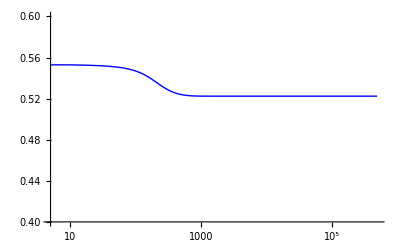

```mathematica
SRtab5=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset5=ListLogLinearPlot[SRtab5,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.6}},PlotStyle->{Blue}]
```

### Example where only pure sexually antagonist selection is present in diploids and yet a polymorphic sex determination system arises.

#### Increasing recombination R (r=0) Sexually antagonistic selection [EQUIL A] [MATT AND I WONDERED WHETHER POLYMORPHIC SEX SYSTEMS MIGHT ARISE EVEN WITH JUST PURELY SEXUALLY ANTAGONISTIC SELECTION. THIS IS AN EXAMPLE. This exampe contradicts the argument by Van Doorn and Kirkpatrick after their equation (10): “Thus if W invades, it will fully replace the ancestral sex-determination system. A protected polymorphism is not possible with loose linkage. We can also exclude the possibility of a protected polymorphism when linkage is tight, and the argument is similar...”]

The neo-W with allele A can invade in this example of sexually antagonistic selection with haploid selection even when unlinked:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.3;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.0;
tryR=0.01;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0.473684,0.409091,0.,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.473684,0.409091,0.,0.5}

{1.04907,0.905374}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}]
```

{{0.905374,1.04907},{0.903146,1.04101},{0.900647,1.03323},{0.897844,1.02575},{0.894701,1.01862},{0.891185,1.01185},{0.887266,1.00549},{0.882917,0.999559},{0.878122,0.994074},{0.872872,0.989044},{0.86717,0.984465},{0.861029,0.980326},{0.854471,0.976604},{0.847522,0.973272},{0.840217,0.970297},{0.832589,0.967644},{0.824673,0.96528},{0.816501,0.963172},{0.808104,0.961288},{0.799509,0.959603},{0.790741,0.958091},{0.781821,0.95673},{0.772768,0.955503},{0.763599,0.954392},{0.754327,0.953384},{0.744965,0.952465},{0.735523,0.951626},{0.726011,0.950858},{0.716436,0.950152},{0.706806,0.949502},{0.697126,0.948902},{0.687401,0.948346},{0.677637,0.947831},{0.667836,0.947351},{0.658003,0.946904},{0.64814,0.946486},{0.638251,0.946095},{0.628337,0.945729},{0.618401,0.945384},{0.608444,0.94506},{0.598469,0.944755},{0.588477,0.944467},{0.578469,0.944194},{0.568447,0.943936},{0.558411,0.943692},{0.548363,0.943459},{0.538303,0.943239},{0.528233,0.943029},{0.518152,0.942829},{0.508063,0.942638},{0.497964,0.942456}}

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

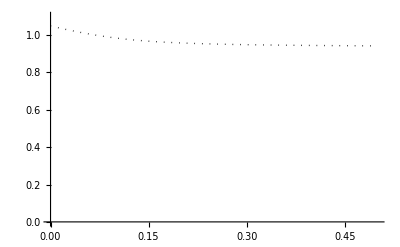

```mathematica
plot4=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Dotted,Black},PlotRange->{Automatic,{0,1.1}}]
]
```

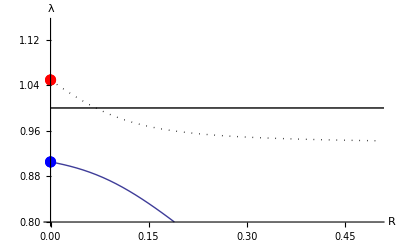

```mathematica
Show[
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0.8,1.15}}],
plot4,
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

{{5,0.50443},{6,0.504357},{6,0.504357},{7,0.504306},{7,0.504306},{8,0.504275},{9,0.504263},{10,0.504268},{11,0.50429},{12,0.504328},{14,0.504449},{15,0.50453},{17,0.504732},{18,0.504853},{20,0.50513},{22,0.505456},{25,0.506035},{27,0.506482},{30,0.507248},{33,0.508136},{37,0.509529},{41,0.511195},{45,0.513177},{50,0.516186},{55,0.519912},{61,0.525573},{67,0.532884},{74,0.544116},{82,0.561569},{91,0.588552},{100,0.623852},{111,0.674662},{123,0.728827},{136,0.775299},{150,0.810313},{166,0.837342},{183,0.85706},{202,0.872645},{224,0.885535},{247,0.895318},{273,0.903482},{302,0.910228},{333,0.915623},{368,0.920204},{407,0.924034},{450,0.927198},{497,0.929787},{550,0.931959},{608,0.93371},{671,0.935101},{742,0.936232},{820,0.937109},{906,0.937777},{1002,0.938279},{1107,0.938637},{1223,0.938885},{1352,0.939052},{1494,0.939157},{1651,0.93922},{1825,0.939256},{2017,0.939274},{2229,0.939284},{2464,0.939288},{2723,0.939289},{3009,0.93929},{3326,0.93929},{3675,0.93929},{4062,0.93929},{4489,0.93929},{4961,0.93929},{5483,0.93929},{6060,0.93929},{6697,0.93929},{7401,0.93929},{8180,0.93929},{9040,0.93929},{9991,0.93929},{11042,0.93929},{12203,0.93929},{13486,0.93929},{14905,0.93929},{16472,0.93929},{18205,0.93929},{20119,0.93929},{22235,0.93929},{24574,0.93929},{27158,0.93929},{30015,0.93929},{33171,0.93929},{36660,0.93929},{40515,0.93929},{44776,0.93929},{49486,0.93929},{54690,0.93929},{60442,0.93929},{66799,0.93929},{73824,0.93929},{81588,0.93929},{90169,0.93929},{99652,0.93929},{110132,0.93929},{121715,0.93929},{134516,0.93929},{148663,0.93929},{164298,0.93929},{181578,0.93929},{200674,0.93929},{221779,0.93929},{245104,0.93929},{270882,0.93929},{299371,0.93929},{330856,0.93929},{365652,0.93929},{404108,0.93929},{446609,0.93929},{493579,0.93929}}

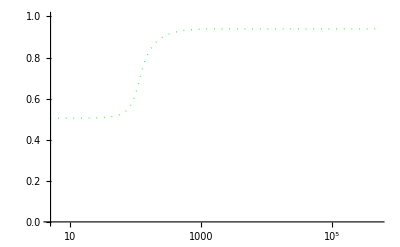

```mathematica
MODtab4=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}]
MODinset4=ListLogLinearPlot[MODtab4,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Dotted,Green}]
```

{{5,0.500309},{6,0.500284},{6,0.500284},{7,0.500262},{7,0.500262},{8,0.500242},{9,0.500224},{10,0.500208},{11,0.500193},{12,0.50018},{14,0.500159},{15,0.50015},{17,0.500135},{18,0.500129},{20,0.500119},{22,0.500112},{25,0.500105},{27,0.500103},{30,0.500102},{33,0.500103},{37,0.500106},{41,0.500111},{45,0.500114},{50,0.500115},{55,0.500106},{61,0.500074},{67,0.500002},{74,0.499831},{82,0.499461},{91,0.498747},{100,0.497785},{111,0.496777},{123,0.49655},{136,0.497086},{150,0.497803},{166,0.498414},{183,0.498832},{202,0.499126},{224,0.499338},{247,0.499479},{273,0.499585},{302,0.499664},{333,0.499721},{368,0.499766},{407,0.4998},{450,0.499827},{497,0.499848},{550,0.499864},{608,0.499877},{671,0.499887},{742,0.499894},{820,0.4999},{906,0.499905},{1002,0.499908},{1107,0.49991},{1223,0.499912},{1352,0.499913},{1494,0.499913},{1651,0.499914},{1825,0.499914},{2017,0.499914},{2229,0.499914},{2464,0.499914},{2723,0.499914},{3009,0.499914},{3326,0.499914},{3675,0.499914},{4062,0.499914},{4489,0.499914},{4961,0.499914},{5483,0.499914},{6060,0.499914},{6697,0.499914},{7401,0.499914},{8180,0.499914},{9040,0.499914},{9991,0.499914},{11042,0.499914},{12203,0.499914},{13486,0.499914},{14905,0.499914},{16472,0.499914},{18205,0.499914},{20119,0.499914},{22235,0.499914},{24574,0.499914},{27158,0.499914},{30015,0.499914},{33171,0.499914},{36660,0.499914},{40515,0.499914},{44776,0.499914},{49486,0.499914},{54690,0.499914},{60442,0.499914},{66799,0.499914},{73824,0.499914},{81588,0.499914},{90169,0.499914},{99652,0.499914},{110132,0.499914},{121715,0.499914},{134516,0.499914},{148663,0.499914},{164298,0.499914},{181578,0.499914},{200674,0.499914},{221779,0.499914},{245104,0.499914},{270882,0.499914},{299371,0.499914},{330856,0.499914},{365652,0.499914},{404108,0.499914},{446609,0.499914},{493579,0.499914}}

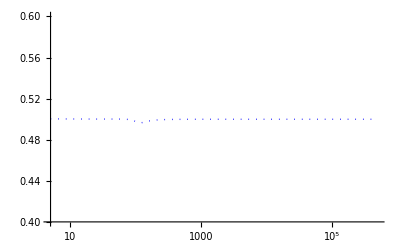

```mathematica
SRtab4=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}]
SRinset4=ListLogLinearPlot[SRtab4,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.6}},PlotStyle->{Dotted,Blue}]
```

## Overdominance in males, invasion with R=1/2

#### Overdominance in males, r=0, both eigenvalues >1. [Invasion (but not fixation) occurs with R=1/2 and no haploid selection. Sex ratio becomes distorted even without haploid selection]

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.5;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2;
tryr=0;
tryR=0.5;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0,0,1.,0.5},{0.6,0.75,0,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.6,0.75,0,0.5}

{1.0303,1.25}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.25,1.0303}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}];
```

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

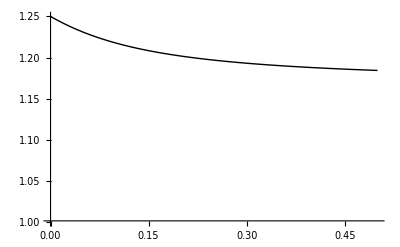

```mathematica
plot5=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{Automatic,{1,1.25}}]
]
```

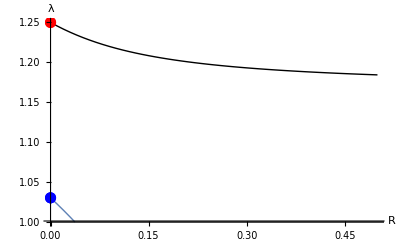

```mathematica
Show[
plot5,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{1,1.25}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

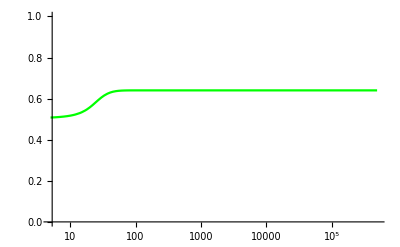

```mathematica
MODtab5=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset5=ListLogLinearPlot[MODtab5,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

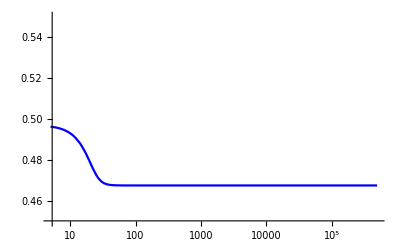

```mathematica
SRinset5=ListLogLinearPlot[Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}],Joined->True,PlotRange->{{startplot,endtime},{0.45,0.55}},PlotStyle->{Blue}]
```

Surprisingly, even without haploid selection, a zygotic sex ratio bias develops. 

By the end of the Run, all the Xa haplotypes have been removed from the popuation.

```mathematica
tryvec={0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0};
generation[param,run[0]].tryvec
generation[param,run[endtime]].tryvec
```

0.39144

0.

The Y carries only the a allele and is sometimes found in females.

```mathematica
tryvec={0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0};
generation[param,run[endtime]].tryvec;
tryvec2={0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0};
generation[param,run[endtime]].tryvec2;
%-%%%
```

0.

The a allele has the highest fitness in females. The X is fixed for the A, which is the allele that has the highest fitness when Xs are in males (there is strong overdominance in males). neo-WYa alleles create the higher fitness females, pairing with either an XA

If the YA were to fix (as occurs during a complete transition from male to female heterogametey) the fitness of males would decrease.

#### Note: if r>0, then neo-W invades and then an alternative equilibrium is reached and neo-W is lost

For these parameters, a small amount of recombination between the ancestral SDR and the A locus means that the neo-W is lost eventually lost. Invasion occurs and allows the system to move towards another stable equilibrium at which YA and Xa are fixed. This alternative equilibrium is very stable because all males and all females have the highest possible fitness.

```mathematica
tryr=0.001;
tryR=0.25;
startplot=5;
endtime=500000;
trypm=0.001;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

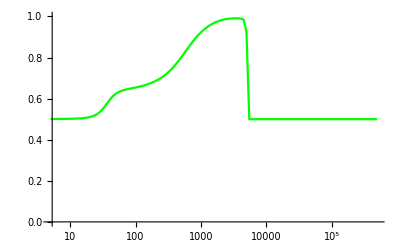

```mathematica
MODtab=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
ListLogLinearPlot[MODtab,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green}]
```

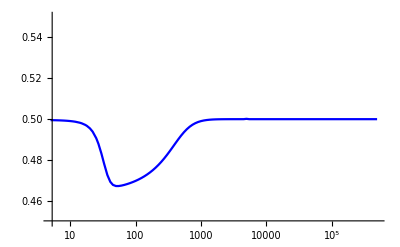

```mathematica
ListLogLinearPlot[Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}],Joined->True,PlotRange->{{startplot,endtime},{0.45,0.55}},PlotStyle->{Blue}]
```

The Y switches from being almost exclusively Ya, to YA

```mathematica
generation[param,run[startplot]][[{13,14}]]
generation[param,run[endtime]][[{13,14}]]
```

{0.00326717,0.497539}

{0.498998,0.00100167}

```mathematica
generation[param,run[endtime]]
```

{0.00166583,0.998334,0.,0.,0.,0.,0.,0.,0.000917138,0.499083,0.,0.,0.498998,0.00100167,0.,0.}

#### Overdominance in males, r=0, both eigenvalues >1. Meiotic drive in heterogametic sex

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.5;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=0.475;
tryr=0;
tryR=0.5;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0,0,1.,0.475},{0.56338,0.71028,0,0.518018}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.56338,0.71028,0,0.518018}

{1.05798,1.26615}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.26615,1.05798}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}];
```

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

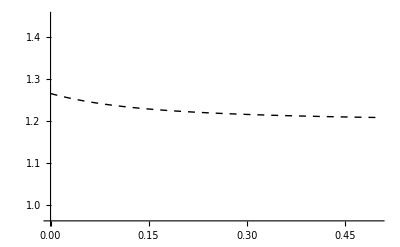

```mathematica
plot6=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black,Dashed},PlotRange->{Automatic,{0.96,1.45}}]
]
```

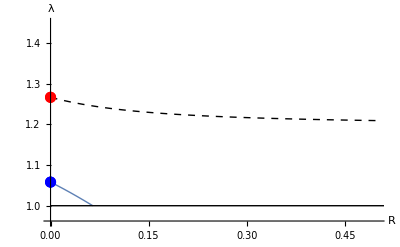

```mathematica
Show[
plot6,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{1,1.25}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

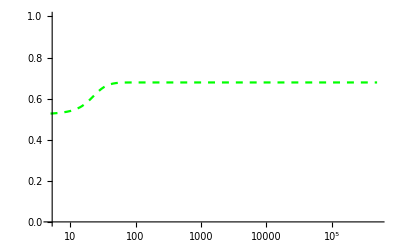

```mathematica
MODtab6=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset6=ListLogLinearPlot[MODtab6,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green,Dashed}]
```

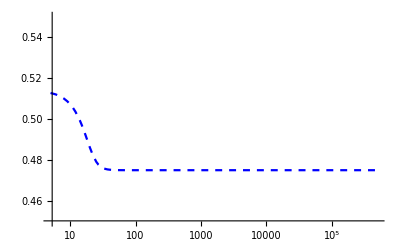

```mathematica
SRinset6=ListLogLinearPlot[Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}],Joined->True,PlotRange->{{startplot,endtime},{0.45,0.55}},PlotStyle->{Blue,Dashed}]
```

#### Overdominance in males, r=0, both eigenvalues >1. Meiotic drive in homogametic sex

The neo-W with allele A can invade in this example of sexually antagonistic  (advantage due to further specializing on the female-beneficial allele):

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.5;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.525;
tryαm=0.5;
tryr=0;
tryR=0.5;
```

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

In this case, the initial equilibrium is:

```mathematica
sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

{{0,0,1.,0.5},{0.7,0.823529,0,0.5}}

If R=r=0 (emanates from equilibrium A):

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]]
norpoints={λmA/.R->0,λma/.R->0}/.SUBS/.subequil/.subpar/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]}
```

{0.7,0.823529,0,0.5}

{1.12,1.30667}

These are the points at R=r=0.  For tryr, we assume that the association with A is still leading:

```mathematica
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
norpoints=Sort[λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->0/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],Greater]
```

{1.30667,1.12}

```mathematica
tab=Table[
equil=sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]];
λ/.Solve[(λ^2-(λmA +λma)λ +(λmA λma-ρmA ρma)/.SUBS/.subequil/.subpar/.R->tryR/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],freqYm->equil[[4]]})==0,λ],{tryR,0,0.5,0.01}];
```

```mathematica
eigen1=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[1]]}]];
eigen2=Transpose[Join[{Table[tryR,{tryR,0,0.5,0.01}]},{Transpose[tab][[2]]}]];
```

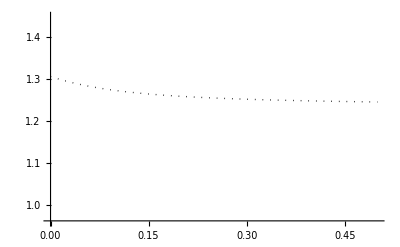

```mathematica
plot7=Show[
ListPlot[eigen2,Joined->True,PlotStyle->{Thick,Black,Dotted},PlotRange->{Automatic,{0.96,1.45}}]
]
```

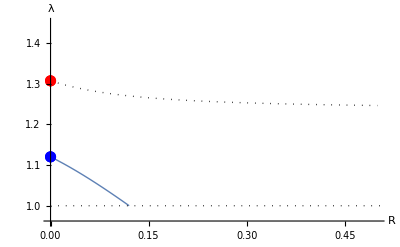

```mathematica
Show[
plot7,
ListPlot[eigen1,Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{1,1.25}}],
ListPlot[{{0,norpoints[[1]]}},PlotStyle->{PointSize[0.02],Red}],
ListPlot[{{0,norpoints[[2]]}},PlotStyle->{PointSize[0.02],Blue}],
ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Thin,Black,Dotted}],
AxesLabel->{"R","λ"}
]
```

This shows that the eigenvalue associated with the neo-W and allele A (red) drives invasion and that invasion is possible for all R<r in the absence of haploid selection.

The following runs simulations to plot neo-W and sex ratio dynamics:

```mathematica
startplot=5;
endtime=500000;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

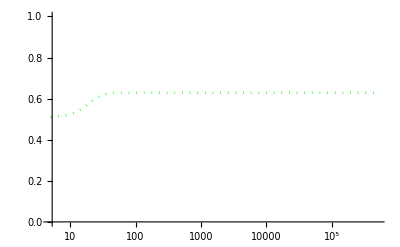

```mathematica
MODtab7=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODinset7=ListLogLinearPlot[MODtab7,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green,Dotted}]
```

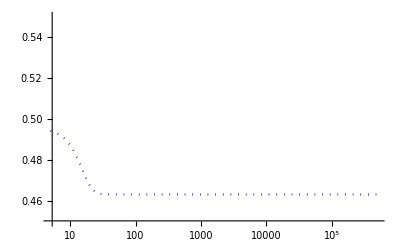

```mathematica
SRinset7=ListLogLinearPlot[Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}],Joined->True,PlotRange->{{startplot,endtime},{0.45,0.55}},PlotStyle->{Blue,Dotted}]
```

#### Overdominance in males, joined

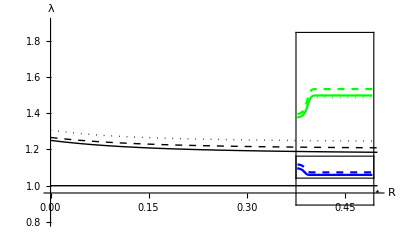

```mathematica
plotD=Show[
plot5,plot6,plot7,
Graphics[Inset[Show[MODinset5,MODinset6,MODinset7,FrameTicks->False,Frame->True],{0.43,1.35},Center,{0.14,1.1}]],
Graphics[Inset[Show[SRinset5,SRinset6,SRinset7,FrameTicks->False,Frame->True],{0.43,1.1},Center,{0.14,0.14}]],
ListPlot[{{0,1},{0.5,1}},Joined->True,PlotStyle->{Thin,Black}],
(*ListPlot[{{0.2,0},{0.2,2}},Joined->True,PlotStyle->{Thin,Black}],*)
Graphics[Text[Style["⋆",Large],{0.5,0.96}]],
(*Graphics[Text[Style["R<r",Medium],{0.16,1.075}]],
Graphics[Text[Style["R>r",Medium],{0.24,1.075}]],*)
AxesLabel->{"R","λ"},PlotRange->{{0,0.5},{0.96,1.45}},AxesOrigin->{0,0.96}
]
```